```mathematica
(* R1 and R2 effect plots 
Figure #3 ==============================>
*)

data0 = {{0.68029455,0.68029455,0.68029455,0.68029415,0.65856753,0.62512199,0.59059013,0.55488802,0.51791107,0.47952957,0.43958263,0.39786990,0.35413987,0.30807293,0.25925627,0.20714522,0.15100118,0.08979909,0.02576981,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000},{0.67871213,0.67871213,0.67871213,0.67871172,0.65709933,0.62383482,0.58949453,0.55399304,0.51722380,0.47905461,0.43932132,0.39781916,0.35429050,0.30840707,0.25974332,0.20773528,0.15161377,0.09043987,0.02380176,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000},{0.67706810,0.67706810,0.67706810,0.67706769,0.65557396,0.62249754,0.58835637,0.55306345,0.51651031,0.47856222,0.43905167,0.39776939,0.35445147,0.30876066,0.26025819,0.20835970,0.15226361,0.09093262,0.07712494,0.00000001,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000},{0.67535870,0.67535870,0.67535870,0.67535830,0.65398791,0.62110704,0.58717292,0.55209701,0.51576884,0.47805112,0.43877297,0.39772047,0.35462329,0.30913490,0.26080274,0.20902112,0.15295364,0.09141854,0.00765268,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000},{0.67357986,0.67357986,0.67357986,0.67357945,0.65233736,0.61965992,0.58594125,0.55109125,0.51499744,0.47751995,0.43848442,0.39767227,0.35480652,0.30953110,0.26137904,0.20972224,0.15368750,0.09209975,0.00609104,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000},{0.67172714,0.67172714,0.67172714,0.67172675,0.65061818,0.61815249,0.58465815,0.55004347,0.51419398,0.47696714,0.43818514,0.39762458,0.35500173,0.30995060,0.26198932,0.21046614,0.15446858,0.09267609,0.03939104,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000},{0.66979574,0.66979574,0.66979574,0.66979536,0.64882585,0.61658072,0.58332011,0.54895073,0.51335608,0.47639100,0.43787411,0.39757716,0.35520947,0.31039489,0.26263595,0.21125616,0.15530159,0.09348161,0.02116139,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000},{0.66778042,0.66778042,0.66778042,0.66778003,0.64695546,0.61494021,0.58192328,0.54780978,0.51248116,0.47578960,0.43755018,0.39752966,0.35543032,0.31086548,0.26332156,0.21209594,0.15619025,0.09416791,0.00549818,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000},{0.66567544,0.66567544,0.66567544,0.66567506,0.64500163,0.61322614,0.58046345,0.54661703,0.51156632,0.47516082,0.43721201,0.39748167,0.35566483,0.31136404,0.26404891,0.21298952,0.15714011,0.09497110,0.03065954,0.00000001,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000},{0.66347454,0.66347454,0.66347454,0.66347417,0.64295848,0.61143323,0.57893596,0.54536854,0.51060835,0.47450226,0.43685812,0.39743265,0.35591355,0.31189228,0.26482107,0.21394118,0.15815655,0.09578028,0.02848895,0.00000001,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000},{0.66117086,0.66117086,0.66117086,0.66117048,0.64081954,0.60955566,0.57733569,0.54405992,0.50960369,0.47381122,0.43648675,0.39738192,0.35617697,0.31245202,0.26564127,0.21495582,0.15924597,0.09681356,0.02430816,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000},{0.65875684,0.65875684,0.65875684,0.65875647,0.63857770,0.60758702,0.57565699,0.54268632,0.50854835,0.47308466,0.43609592,0.39732865,0.35645555,0.31304517,0.26651305,0.21603876,0.16041528,0.09785713,0.02261558,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000},{0.65622418,0.65622418,0.65622418,0.65622379,0.63622513,0.60552023,0.57389359,0.54124233,0.50743786,0.47231915,0.43568331,0.39727178,0.35674967,0.31367371,0.26744023,0.21719577,0.16167238,0.09889813,0.00138908,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000},{0.65356370,0.65356370,0.65356370,0.65356335,0.63375317,0.60334744,0.57203849,0.53972193,0.50626721,0.47151078,0.43524627,0.39721004,0.35705959,0.31433968,0.26842690,0.21843331,0.16302582,0.10006684,0.01520588,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000},{0.65076526,0.65076526,0.65076526,0.65076489,0.63115223,0.60105994,0.57008394,0.53811834,0.50503074,0.47065512,0.43478167,0.39714180,0.35738541,0.31504519,0.26947746,0.21975831,0.16448580,0.10147426,0.02729232,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000},{0.64781758,0.64781758,0.64781758,0.64781723,0.62841164,0.59864803,0.56802126,0.53642400,0.50372206,0.46974707,0.43428590,0.39706510,0.35772706,0.31579233,0.27059659,0.22117859,0.16606368,0.10285880,0.02100082,0.00000001,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000},{0.64470815,0.64470815,0.64470815,0.64470782,0.62551954,0.59610086,0.56584069,0.53463035,0.50233393,0.46878082,0.43375473,0.39697750,0.35808418,0.31658318,0.27178928,0.22270263,0.16777107,0.10457907,0.01189532,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000},{0.64142298,0.64142298,0.64142298,0.64142261,0.62246264,0.59340628,0.56353131,0.53272773,0.50085809,0.46774965,0.43318318,0.39687601,0.35845603,0.31741976,0.27306082,0.22433968,0.16962262,0.10608133,0.01435546,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000},{0.63794641,0.63794641,0.63794641,0.63794605,0.61922607,0.59055064,0.56108074,0.53070520,0.49928510,0.46664583,0.43256538,0.39675690,0.35884145,0.31830386,0.27441673,0.22609996,0.17163389,0.10800471,0.03204535,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000},{0.63426088,0.63426088,0.63426088,0.63426055,0.61579311,0.58751853,0.55847500,0.52855028,0.49760417,0.46546036,0.43189441,0.39661561,0.35923863,0.31923706,0.27586274,0.22799448,0.17382363,0.11026867,0.04729574,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000},{0.63034659,0.63034659,0.63034659,0.63034626,0.61214487,0.58429251,0.55569819,0.52624872,0.49580282,0.46418278,0.43116203,0.39644649,0.35964496,0.32022045,0.27740466,0.23003519,0.17621086,0.11245244,0.03831819,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000},{0.62618115,0.62618115,0.62618115,0.62618081,0.60825996,0.58085277,0.55273216,0.52378417,0.49386667,0.46280084,0.43035844,0.39624253,0.36005679,0.32125453,0.27904819,0.23223490,0.17881842,0.11509495,0.03491809,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000},{0.62173914,0.62173914,0.62173914,0.62173881,0.60411407,0.57717671,0.54955613,0.52113778,0.49177898,0.46130015,0.42947189,0.39599507,0.36046914,0.32233886,0.28079891,0.23460716,0.18167233,0.11805119,0.04179954,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000},{0.61699162,0.61699162,0.61699162,0.61699130,0.59967943,0.57323842,0.54614617,0.51828775,0.48952022,0.45966372,0.42848826,0.39569333,0.36087523,0.32347169,0.28266163,0.23716607,0.18479951,0.12138031,0.02593121,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000},{0.61190542,0.61190542,0.61190542,0.61190514,0.59492420,0.56900811,0.54247462,0.51520871,0.48706753,0.45787143,0.42739052,0.39532389,0.36126602,0.32464950,0.28464016,0.23992595,0.18823064,0.12503262,0.01779464,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000},{0.60644243,0.60644243,0.60644243,0.60644211,0.58981170,0.56445131,0.53850935,0.51187100,0.48439392,0.45589925,0.42615800,0.39486998,0.36162947,0.32586625,0.28673659,0.24290062,0.19199901,0.12930106,0.01229132,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000},{0.60055860,0.60055860,0.60055860,0.60055829,0.58429944,0.55952796,0.53421285,0.50823979,0.48146745,0.45371841,0.42476552,0.39431061,0.36194965,0.32711250,0.28895034,0.24610266,0.19613860,0.13404587,0.02022940,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000},{0.59420277,0.59420277,0.59420277,0.59420248,0.57833800,0.55419128,0.52954106,0.50427393,0.47825006,0.45129424,0.42318222,0.39361936,0.36220558,0.32837419,0.29127679,0.24954185,0.20068449,0.13935629,0.06048243,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000},{0.58731520,0.58731520,0.58731520,0.58731491,0.57186949,0.54838626,0.52444196,0.49992448,0.47469614,0.44858474,0.42137013,0.39276293,0.36236958,0.32963094,0.29370567,0.25322324,0.20566908,0.14537579,0.03827451,0.00000006,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000},{0.57982565,0.57982565,0.57982565,0.57982536,0.56482575,0.54204788,0.51885372,0.49513296,0.47075069,0.44553869,0.41928223,0.39169915,0.36240533,0.33085379,0.29621827,0.25714405,0.21111858,0.15236300,0.03371915,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000},{0.57165108,0.57165108,0.57165108,0.57165081,0.55712601,0.53509873,0.51270239,0.48982892,0.46634695,0.44209325,0.41685999,0.39037437,0.36226498,0.33200231,0.29878429,0.26128964,0.21704758,0.16033731,0.03582484,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000},{0.56269259,0.56269259,0.56269259,0.56269231,0.54867381,0.52744606,0.50589885,0.48392697,0.46140334,0.43817085,0.41403013,0.38872009,0.36188562,0.33302046,0.30135699,0.26562745,0.22345006,0.16919432,0.06023386,0.01240428,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00369142,0.00000000,0.00000001,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000001,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000},{0.55283150,0.55283150,0.55283150,0.55283124,0.53935315,0.51897778,0.49833491,0.47732278,0.45581940,0.43367499,0.41070031,0.38664842,0.36118433,0.33383128,0.30386699,0.27009918,0.23028700,0.17921955,0.03835402,0.00941650,0.12594701,0.08339506,0.00553653,0.00538481,0.00000000,0.00000000,0.00000000,0.06666488,0.05391717,0.03134360,0.01612806,0.01073893,0.01076109,0.02692883,0.01627862,0.00000000,0.03769650,0.02148405,0.07320552,0.05037873,0.00539090,0.06268721,0.00537957,0.01640787,0.00000000,0.01259386,0.01372995,0.02745180,0.00000000,0.00000000,0.12594500},{0.54192423,0.54192423,0.54192423,0.54192399,0.52902335,0.50955742,0.48987816,0.46988783,0.44947047,0.42848478,0.40675339,0.38404607,0.36005184,0.33432968,0.30621397,0.27461025,0.23747217,0.19009342,0.06519739,0.08822399,0.12594701,0.09266118,0.05056653,0.08397468,0.06163716,0.09150637,0.05336721,0.12594692,0.05767591,0.15671799,0.06130981,0.08982085,0.06509036,0.06515022,0.06892102,0.09150622,0.07644458,0.08394252,0.09150690,0.12594684,0.06142548,0.15671803,0.08020837,0.05390236,0.12594700,0.12593865,0.05373339,0.09150599,0.12594700,0.08980031,0.12594500},{0.52979553,0.52979553,0.52979553,0.52979530,0.51751226,0.49901727,0.48036503,0.46146248,0.44220054,0.42244758,0.40203985,0.38076628,0.35834363,0.33437281,0.30825549,0.27901591,0.24485159,0.20172496,0.12761690,0.10276382,0.12594701,0.11263282,0.15671794,0.10872679,0.09495043,0.09839466,0.09495176,0.12594692,0.09150427,0.15671799,0.10184350,0.12594707,0.09150726,0.10183360,0.10872743,0.09839440,0.09839617,0.09150084,0.09839365,0.12594684,0.14367112,0.15671803,0.15019896,0.12594697,0.12594700,0.12593865,0.12594698,0.09495052,0.12594700,0.12596071,0.12594500},{0.51622935,0.51622935,0.51622935,0.51622912,0.50460717,0.48714922,0.46959158,0.45184650,0.43381258,0.41536908,0.39636738,0.37661787,0.35586846,0.33376732,0.30979255,0.28310436,0.25218118,0.21372642,0.14145517,0.14791164,0.12560145,0.12594725,0.15671794,0.13825189,0.14440868,0.13517875,0.12595728,0.12594246,0.13210117,0.15671799,0.13517856,0.13210199,0.13207788,0.13517821,0.14133225,0.12902496,0.12595136,0.15364082,0.13517826,0.15364084,0.15671786,0.15671803,0.15671795,0.13517826,0.13825539,0.14132830,0.13744201,0.14440955,0.12902404,0.12903643,0.14748606},{0.50095653,0.50095653,0.50095653,0.50095634,0.49004240,0.47369227,0.45730083,0.44078618,0.42405541,0.40699962,0.38948673,0.37135043,0.35237246,0.33225228,0.31055083,0.28657512,0.25910433,0.22566042,0.16446327,0.16222337,0.15789841,0.16461345,0.16205879,0.15671546,0.15671825,0.15671785,0.17273851,0.15938799,0.15938821,0.15938851,0.15938816,0.15939169,0.15669465,0.17006911,0.15938823,0.17808123,0.15938816,0.16739878,0.16205837,0.15671795,0.15671794,0.16472862,0.16739880,0.17807964,0.16739881,0.16739881,0.18342007,0.15938804,0.15938816,0.15938807,0.17273922},{0.48363775,0.48363775,0.48363775,0.48363754,0.47348219,0.45831525,0.44316519,0.42795649,0.41260533,0.39701545,0.38107225,0.36463396,0.34751776,0.32947645,0.31015635,0.28901357,0.26512468,0.23669279,0.18828221,0.18563317,0.18341904,0.18563242,0.18342005,0.18342025,0.18342007,0.18563313,0.18341946,0.18563325,0.18341997,0.19005926,0.18563313,0.18341998,0.18342007,0.18563313,0.18342007,0.19227233,0.19227233,0.19669846,0.18342007,0.18342132,0.18563313,0.19005927,0.18342007,0.18563313,0.19227233,0.19227233,0.18342007,0.18784620,0.18563341,0.19448540,0.18563313},{0.46383950,0.46383950,0.46383950,0.46383931,0.45449661,0.44059244,0.42676180,0.41293591,0.39904046,0.38499226,0.37069460,0.35603063,0.34085311,0.32496773,0.30810394,0.28985953,0.26958222,0.24609984,0.20845434,0.21231726,0.20566522,0.20555072,0.20555072,0.20555075,0.20555073,0.20555073,0.20555072,0.20555072,0.20724236,0.20555072,0.20724236,0.20555072,0.20555072,0.21231726,0.21400889,0.20555072,0.20555072,0.20555072,0.21231726,0.20555073,0.20893399,0.20724236,0.20555072,0.21231726,0.20893399,0.20555072,0.20555072,0.20555072,0.20555072,0.20724236,0.20555072},{0.44099984,0.44099984,0.44099984,0.44099967,0.43252705,0.41996872,0.40753711,0.39517039,0.38280391,0.37036750,0.35778211,0.34495508,0.33177314,0.31809154,0.30371572,0.28836830,0.27162348,0.25281256,0.22755232,0.22464031,0.22246705,0.22246951,0.22246706,0.22246705,0.22246705,0.22246705,0.22246705,0.22246705,0.22246705,0.22572694,0.22246705,0.22246705,0.22246705,0.22246705,0.22246705,0.22246705,0.22246705,0.22246705,0.22246705,0.22246705,0.22246705,0.22246705,0.22572694,0.22246705,0.22246705,0.22464031,0.22355368,0.22464031,0.22464031,0.22355368,0.22246705},{0.41437817,0.41437817,0.41437817,0.41437802,0.40683571,0.39570843,0.38475503,0.37392068,0.36315013,0.35238574,0.34156503,0.33061759,0.31946078,0.30799324,0.29608479,0.28355916,0.27016250,0.25555309,0.23469973,0.23333333,0.23333333,0.23370428,0.23333333,0.23333333,0.23370428,0.23333333,0.23333333,0.23370428,0.23333333,0.23333333,0.23333333,0.23370428,0.23333333,0.23333333,0.23333333,0.23333333,0.23333333,0.23333333,0.23333333,0.23333333,0.23333333,0.23333333,0.23333333,0.23333333,0.23333333,0.23407523,0.23333333,0.23370428,0.23333333,0.23333333,0.23333333},{0.38297998,0.38297998,0.38297998,0.38297985,0.37642986,0.36681878,0.35741935,0.34818355,0.33906501,0.33001750,0.32099327,0.31194113,0.30280403,0.29351571,0.28399586,0.27414241,0.26381898,0.25283645,0.23744604,0.23704279,0.23704279,0.23704279,0.23704279,0.23704279,0.23704279,0.23704279,0.23704279,0.23704279,0.23704279,0.23704279,0.23704279,0.23704279,0.23654832,0.23704279,0.23654832,0.23704279,0.23704279,0.23704279,0.23704279,0.23704279,0.23704279,0.23704279,0.23654832,0.23704279,0.23704279,0.23704279,0.23704279,0.23704279,0.23704279,0.23704279,0.23704279},{0.34544080,0.34544080,0.34544080,0.34544068,0.33994507,0.33193180,0.32415428,0.31657100,0.30914362,0.30183581,0.29461204,0.28743648,0.28027171,0.27307718,0.26580725,0.25840833,0.25081489,0.24296344,0.23374741,0.23209804,0.23209804,0.23209804,0.23209804,0.23209804,0.23209804,0.23209804,0.23209804,0.23209804,0.23209804,0.23209804,0.23209804,0.23209804,0.23209804,0.23209804,0.23209804,0.23209804,0.23209804,0.23209804,0.23209804,0.23209804,0.23209804,0.23209804,0.23209804,0.23209804,0.23209804,0.23209804,0.23209804,0.23209804,0.23209804,0.23209804,0.23209804},{0.29984148,0.29984148,0.29984148,0.29984139,0.29545937,0.28911673,0.28301501,0.27711896,0.27139738,0.26582212,0.26036720,0.25500806,0.24972086,0.24448184,0.23926652,0.23404890,0.22880039,0.22349343,0.21414573,0.21642204,0.21642204,0.21642204,0.21642204,0.21642204,0.21642204,0.21642204,0.21642204,0.21642204,0.21642204,0.21642204,0.21642204,0.21642204,0.21642204,0.21642204,0.21642204,0.21642204,0.21642204,0.21642204,0.21642204,0.21642204,0.21642204,0.21642204,0.21642204,0.21642204,0.21642204,0.21642204,0.21642204,0.21642204,0.21642204,0.21642204,0.21642204},{0.24340275,0.24340275,0.24340275,0.24340268,0.24018610,0.23557034,0.23117564,0.22697319,0.22293838,0.21904989,0.21528897,0.21163887,0.20808438,0.20461147,0.20120697,0.19785824,0.19455297,0.19128792,0.18780917,0.18704763,0.18704762,0.18230119,0.18704762,0.18704762,0.18704762,0.18704762,0.18704762,0.18704762,0.18704762,0.18704762,0.18704762,0.18704762,0.18704762,0.18704762,0.18704762,0.18704762,0.18704762,0.18704762,0.18704762,0.18704762,0.18704762,0.18704762,0.18704762,0.18704762,0.18704762,0.18704762,0.18704762,0.18704762,0.18704762,0.18704762,0.18704762},{0.17195698,0.17195698,0.17195698,0.17195693,0.16994327,0.16708281,0.16439206,0.16184990,0.15943873,0.15714371,0.15495217,0.15285319,0.15083724,0.14889596,0.14702195,0.14520856,0.14344983,0.14174295,0.14018981,0.13958333,0.13234924,0.13958333,0.13234924,0.13958333,0.13958333,0.13958333,0.13958333,0.13958333,0.13958333,0.13958333,0.13958333,0.13958333,0.13958333,0.13958333,0.13958333,0.13958333,0.13958333,0.13958333,0.13958333,0.13234924,0.13958333,0.13958333,0.13958333,0.13958333,0.13958333,0.13958333,0.13234924,0.13958333,0.13958333,0.13958333,0.13958333},{0.07898353,0.07898353,0.07898353,0.07898350,0.07818534,0.07706495,0.07602575,0.07505745,0.07415163,0.07330128,0.07250048,0.07174423,0.07102824,0.07034879,0.06970266,0.06908701,0.06849936,0.06793804,0.06741846,0.06051833,0.06724242,0.05379421,0.06724242,0.06724242,0.06724242,0.06051830,0.06724242,0.06724242,0.06724242,0.06724242,0.06724242,0.06724242,0.06051834,0.06724243,0.05379415,0.06724242,0.06724242,0.06051834,0.04707003,0.06051830,0.06724242,0.06051829,0.06724242,0.06724242,0.06051833,0.06724243,0.06724242,0.05379421,0.06724242,0.04034609,0.05379420},{0.00000167,0.00000164,0.00000173,0.00000167,0.00000158,0.00000168,0.00000159,0.00000163,0.00000159,0.00000160,0.00000150,0.00000146,0.00000149,0.00000154,0.00000154,0.00000146,0.00000151,0.00000144,0.00000134,0.00000144,0.00000132,0.00000150,0.00000110,0.00000152,0.00000123,0.00000141,0.00000132,0.00000112,0.00000121,0.00000144,0.00000137,0.00000113,0.00000152,0.00000121,0.00000089,0.00000126,0.00000143,0.00000140,0.00000113,0.00000144,0.00000129,0.00000102,0.00000109,0.00000128,0.00000151,0.00000118,0.00000060,0.00000121,0.00000135,0.00000142,0.00000104},{0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000},{0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000},{0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00123844,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000}};

R01R02effect1=MatrixPlot[data0, 
ColorFunction->ColorData["TemperatureMap"],
ColorFunctionScaling->True,
PlotLegends->None, 
LabelStyle->Directive[Bold, FontSize->10],
FrameLabel->{Style["", Black, 8 ], Style["", Black,8]},
Frame->True,
FrameTicks->{None,None},
ImageSize-> {200},
Epilog->{Directive[{Thickness[0.025],Dashed,Black}],Line[{{2,0.6},{2,51}}]}
(*Epilog->{Text[Style["Extinction Equilibrium",Medium,Bold,Black],{35,27}], 
Text[Style["Disease Free Equilibrium",Medium,Bold,Black],{25,49}], 
Text[Style["Endemic Equilibria",Medium,Bold,Black],{10,20}]}*)
];

R01R02effect2=MatrixPlot[data0, 
ColorFunction->ColorData["TemperatureMap"],
ColorFunctionScaling->True,
PlotLegends->None, 
LabelStyle->Directive[Bold, FontSize->10],
FrameLabel->{Style["", Black, 8 ], Style["", Black, 8]},
Frame->True,
FrameTicks->{None,None},
ImageSize-> {200},
Epilog->{Directive[{Thickness[0.025],Dashed,Black}],Line[{{15,0.6},{15,51}}]}
(*Epilog->{Text[Style["Extinction Equilibrium",Medium,Bold,Black],{35,27}], 
Text[Style["Disease Free Equilibrium",Medium,Bold,Black],{25,49}], 
Text[Style["Endemic Equilibria",Medium,Bold,Black],{10,20}]}*)
];

R01R02effect3=MatrixPlot[data0, 
ColorFunction->ColorData["TemperatureMap"],
ColorFunctionScaling->True,
PlotLegends->None, 
LabelStyle->Directive[Bold, FontSize->10],
FrameLabel->{Style["", Black, 8 ], Style["", Black, 8]},
Frame->True,
FrameTicks->{None,None},
ImageSize-> {200},
Epilog->{Directive[{Thickness[0.025],Dashed,Black}],Line[{{30,0.6},{30,51}}]}
(*Epilog->{Text[Style["Extinction Equilibrium",Medium,Bold,Black],{35,27}], 
Text[Style["Disease Free Equilibrium",Medium,Bold,Black],{25,49}], 
Text[Style["Endemic Equilibria",Medium,Bold,Black],{10,20}]}*)
];

R01R02effectAll=MatrixPlot[data0, 
ColorFunction->ColorData["TemperatureMap"],
ColorFunctionScaling->True,
PlotLegends->Automatic, 
LabelStyle->Directive[Bold, FontSize->10],
FrameLabel->{Style["", Black, 20 ], Style["", Black,20]},
Frame->True,
ImageSize-> {550},
FrameTicks->{{{{1,8.0},{3,7.7},{5,7.4},{7,7.1},{9,6.8},{11,6.5},{13,6.2},{15,5.9},{17,5.6},{19,5.3},{21,5.0},{23,4.7},{25,4.4},{27,4.1},{29,3.8},{31,3.5},{33,3.2},{35,2.9},{37,2.6},{39,2.3},{41,2.0},{43,1.7},{45,1.4},{47,1.1},{49,0.8},{51,0.5}},None},
{{{1,Rotate[0.5,π/2]},{3,Rotate[0.8,π/2]},{5,Rotate[1.1,π/2]},{7,Rotate[1.4,π/2]},{9,Rotate[1.7,π/2]},{11,Rotate[2.0,π/2]},{13,Rotate[2.3,π/2]},{15,Rotate[2.6,π/2]},{17,Rotate[2.9,π/2]},{19,Rotate[3.2,π/2]},{21,Rotate[3.5,π/2]},{23,Rotate[3.8,π/2]},{25,Rotate[4.1,π/2]},{27,Rotate[4.4,π/2]},{29,Rotate[4.7,π/2]},{31,Rotate[5.0,π/2]},{33,Rotate[5.3,π/2]},{35,Rotate[5.6,π/2]},{37,Rotate[5.9,π/2]},{39,Rotate[6.2,π/2]},{41,Rotate[6.5,π/2]},{43,Rotate[6.8,π/2]},{45,Rotate[7.1,π/2]},{47,Rotate[7.4,π/2]},{49,Rotate[7.7,π/2]},{51,Rotate[8.0,π/2]}},{{1,None}}}},
Epilog->{
Text[Style["",16,Bold,Black],{2,2}],
Text[Style["",16,Bold,Black],{2,29}],
Text[Style["",16,Bold,Black],{11,29}],
Text[Style["",16,Bold,Black],{11,2}],
Text[Style["",16,Bold,Black],{35,2}], 
Text[Style["",16,Bold,Black],{35,12}], 
Text[Style["",16,Bold,Black],{35,35}],
Rotate[Text[Style["",16,Bold,Black],{5,15}], 3π/2],
Text[Style["",16,Bold,Black],{45,5}],
Directive[{Thickness[0.002],Dashed,Black}],Line[{{18,0.6},{18,51}}],
Directive[{Thickness[0.002],Dashed,Black}],Line[{{4,0.6},{4,51}}],
Directive[{Thickness[0.002],Dashed,Black}],Line[{{1,4},{51,4}}],
Directive[{Thickness[0.002],Dashed,Black}],Line[{{18,19},{51,19}}]}
];

Export["C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/picno/Plots/R01R02effect_V2.pdf",R01R02effectAll,"PDF","AllowRasterization"->False];

R01R02effectAll
(*R01R02effect1*)
```

-Graphics-

```mathematica
(* Alpha and P effect plot *)
(*
dataAlphaP ={{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.4337,0.4252,0.4166,0.4082,0.4000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.5118,0.4989,0.4867,0.4751,0.4646,0.4540,0.4440,0.4343,0.4251,0.4167,0.4082,0.4000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.6036,0.5854,0.5690,0.5533,0.5384,0.5249,0.5115,0.4988,0.4866,0.4751,0.4646,0.4540,0.4440,0.4343,0.4251,0.4167,0.4082,0.4000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.7094,0.6849,0.6623,0.6410,0.6211,0.6033,0.5857,0.5690,0.5533,0.5384,0.5249,0.5115,0.4988,0.4866,0.4751,0.4646,0.4540,0.4440,0.4343,0.4251,0.4167,0.4082,0.4000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.7626,0.7339,0.7092,0.6849,0.6623,0.6410,0.6211,0.6033,0.5857,0.5690,0.5533,0.5384,0.5249,0.5115,0.4988,0.4866,0.4751,0.4646,0.4540,0.4440,0.4343,0.4251,0.4167,0.4082,0.4000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.8619,0.8248,0.7921,0.7619,0.7339,0.7092,0.6849,0.6623,0.6410,0.6211,0.6033,0.5857,0.5690,0.5533,0.5384,0.5249,0.5115,0.4988,0.4866,0.4751,0.4646,0.4540,0.4440,0.4343,0.4251,0.4167,0.4082,0.4000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.9391,0.8969,0.8602,0.8247,0.7921,0.7619,0.7339,0.7092,0.6849,0.6623,0.6410,0.6211,0.6033,0.5857,0.5690,0.5533,0.5384,0.5249,0.5115,0.4988,0.4866,0.4751,0.4646,0.4540,0.4440,0.4343,0.4251,0.4167,0.4082,0.4000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.9852,0.9390,0.8969,0.8602,0.8247,0.7921,0.7619,0.7339,0.7092,0.6849,0.6623,0.6410,0.6211,0.6033,0.5857,0.5690,0.5533,0.5384,0.5249,0.5115,0.4988,0.4866,0.4751,0.4646,0.4540,0.4440,0.4343,0.4251,0.4167,0.4082,0.4000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,1.0930,1.0363,0.9852,0.9390,0.8969,0.8602,0.8247,0.7921,0.7619,0.7339,0.7092,0.6849,0.6623,0.6410,0.6211,0.6033,0.5857,0.5690,0.5533,0.5384,0.5249,0.5115,0.4988,0.4866,0.4751,0.4646,0.4540,0.4440,0.4343,0.4251,0.4167,0.4082,0.4000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,1.1526,1.0929,1.0363,0.9852,0.9390,0.8969,0.8602,0.8247,0.7921,0.7619,0.7339,0.7092,0.6849,0.6623,0.6410,0.6211,0.6033,0.5857,0.5690,0.5533,0.5384,0.5249,0.5115,0.4988,0.4866,0.4751,0.4646,0.4540,0.4440,0.4343,0.4251,0.4167,0.4082,0.4000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,1.3020,1.2233,1.1527,1.0929,1.0363,0.9852,0.9390,0.8969,0.8602,0.8247,0.7921,0.7619,0.7339,0.7092,0.6849,0.6623,0.6410,0.6211,0.6033,0.5857,0.5690,0.5533,0.5384,0.5249,0.5115,0.4988,0.4866,0.4751,0.4646,0.4540,0.4440,0.4343,0.4251,0.4167,0.4082,0.4000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,1.3029,1.2232,1.1527,1.0929,1.0363,0.9852,0.9390,0.8969,0.8602,0.8247,0.7921,0.7619,0.7339,0.7092,0.6849,0.6623,0.6410,0.6211,0.6033,0.5857,0.5690,0.5533,0.5384,0.5249,0.5115,0.4988,0.4866,0.4751,0.4646,0.4540,0.4440,0.4343,0.4251,0.4167,0.4082,0.4000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,1.5014,1.3938,1.3029,1.2232,1.1527,1.0929,1.0363,0.9852,0.9390,0.8969,0.8602,0.8247,0.7921,0.7619,0.7339,0.7092,0.6849,0.6623,0.6410,0.6211,0.6033,0.5857,0.5690,0.5533,0.5384,0.5249,0.5115,0.4988,0.4866,0.4751,0.4646,0.4540,0.4440,0.4343,0.4251,0.4167,0.4082,0.4000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,1.4985,1.3937,1.3029,1.2232,1.1527,1.0929,1.0363,0.9852,0.9390,0.8969,0.8602,0.8247,0.7921,0.7619,0.7339,0.7092,0.6849,0.6623,0.6410,0.6211,0.6033,0.5857,0.5690,0.5533,0.5384,0.5249,0.5115,0.4988,0.4866,0.4751,0.4646,0.4540,0.4440,0.4343,0.4251,0.4167,0.4082,0.4000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,1.6139,1.4981,1.3937,1.3029,1.2232,1.1527,1.0929,1.0363,0.9852,0.9390,0.8969,0.8602,0.8247,0.7921,0.7619,0.7339,0.7092,0.6849,0.6623,0.6410,0.6211,0.6033,0.5857,0.5690,0.5533,0.5384,0.5249,0.5115,0.4988,0.4866,0.4751,0.4646,0.4540,0.4440,0.4343,0.4251,0.4167,0.4082,0.4000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,1.7474,1.6129,1.4981,1.3937,1.3029,1.2232,1.1527,1.0929,1.0363,0.9852,0.9390,0.8969,0.8602,0.8247,0.7921,0.7619,0.7339,0.7092,0.6849,0.6623,0.6410,0.6211,0.6033,0.5857,0.5690,0.5533,0.5384,0.5249,0.5115,0.4988,0.4866,0.4751,0.4646,0.4540,0.4440,0.4343,0.4251,0.4167,0.4082,0.4000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,1.7548,1.6129,1.4981,1.3937,1.3029,1.2232,1.1527,1.0929,1.0363,0.9852,0.9390,0.8969,0.8602,0.8247,0.7921,0.7619,0.7339,0.7092,0.6849,0.6623,0.6410,0.6211,0.6033,0.5857,0.5690,0.5533,0.5384,0.5249,0.5115,0.4988,0.4866,0.4751,0.4646,0.4540,0.4440,0.4343,0.4251,0.4167,0.4082,0.4000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,1.9310,1.7544,1.6129,1.4981,1.3937,1.3029,1.2232,1.1527,1.0929,1.0363,0.9852,0.9390,0.8969,0.8602,0.8247,0.7921,0.7619,0.7339,0.7092,0.6849,0.6623,0.6410,0.6211,0.6033,0.5857,0.5690,0.5533,0.5384,0.5249,0.5115,0.4988,0.4866,0.4751,0.4646,0.4540,0.4440,0.4343,0.4251,0.4167,0.4082,0.4000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,1.9225,1.7544,1.6129,1.4981,1.3937,1.3029,1.2232,1.1527,1.0929,1.0363,0.9852,0.9390,0.8969,0.8602,0.8247,0.7921,0.7619,0.7339,0.7092,0.6849,0.6623,0.6410,0.6211,0.6033,0.5857,0.5690,0.5533,0.5384,0.5249,0.5115,0.4988,0.4866,0.4751,0.4646,0.4540,0.4440,0.4343,0.4251,0.4167,0.4082,0.4000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,1.9231,1.7544,1.6129,1.4981,1.3937,1.3029,1.2232,1.1527,1.0929,1.0363,0.9852,0.9390,0.8969,0.8602,0.8247,0.7921,0.7619,0.7339,0.7092,0.6849,0.6623,0.6410,0.6211,0.6033,0.5857,0.5690,0.5533,0.5384,0.5249,0.5115,0.4988,0.4866,0.4751,0.4646,0.4540,0.4440,0.4343,0.4251,0.4167,0.4082,0.4000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,2.1262,1.9231,1.7544,1.6129,1.4981,1.3937,1.3029,1.2232,1.1527,1.0929,1.0363,0.9852,0.9390,0.8969,0.8602,0.8247,0.7921,0.7619,0.7339,0.7092,0.6849,0.6623,0.6410,0.6211,0.6033,0.5857,0.5690,0.5533,0.5384,0.5249,0.5115,0.4988,0.4866,0.4751,0.4646,0.4540,0.4440,0.4343,0.4251,0.4167,0.4082,0.4000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,2.1277,1.9231,1.7544,1.6129,1.4981,1.3937,1.3029,1.2232,1.1527,1.0929,1.0363,0.9852,0.9390,0.8969,0.8602,0.8247,0.7921,0.7619,0.7339,0.7092,0.6849,0.6623,0.6410,0.6211,0.6033,0.5857,0.5690,0.5533,0.5384,0.5249,0.5115,0.4988,0.4866,0.4751,0.4646,0.4540,0.4440,0.4343,0.4251,0.4167,0.4082,0.4000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,2.3881,2.1277,1.9231,1.7544,1.6129,1.4981,1.3937,1.3029,1.2232,1.1527,1.0929,1.0363,0.9852,0.9390,0.8969,0.8602,0.8247,0.7921,0.7619,0.7339,0.7092,0.6849,0.6623,0.6410,0.6211,0.6033,0.5857,0.5690,0.5533,0.5384,0.5249,0.5115,0.4988,0.4866,0.4751,0.4646,0.4540,0.4440,0.4343,0.4251,0.4167,0.4082,0.4000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,2.3833,2.1277,1.9231,1.7544,1.6129,1.4981,1.3937,1.3029,1.2232,1.1527,1.0929,1.0363,0.9852,0.9390,0.8969,0.8602,0.8247,0.7921,0.7619,0.7339,0.7092,0.6849,0.6623,0.6410,0.6211,0.6033,0.5857,0.5690,0.5533,0.5384,0.5249,0.5115,0.4988,0.4866,0.4751,0.4646,0.4540,0.4440,0.4343,0.4251,0.4167,0.4082,0.4000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,2.3811,2.1277,1.9231,1.7544,1.6129,1.4981,1.3937,1.3029,1.2232,1.1527,1.0929,1.0363,0.9852,0.9390,0.8969,0.8602,0.8247,0.7921,0.7619,0.7339,0.7092,0.6849,0.6623,0.6410,0.6211,0.6033,0.5857,0.5690,0.5533,0.5384,0.5249,0.5115,0.4988,0.4866,0.4751,0.4646,0.4540,0.4440,0.4343,0.4251,0.4167,0.4082,0.4000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,2.3810,2.1277,1.9231,1.7544,1.6129,1.4981,1.3937,1.3029,1.2232,1.1527,1.0929,1.0363,0.9852,0.9390,0.8969,0.8602,0.8247,0.7921,0.7619,0.7339,0.7092,0.6849,0.6623,0.6410,0.6211,0.6033,0.5857,0.5690,0.5533,0.5384,0.5249,0.5115,0.4988,0.4866,0.4751,0.4646,0.4540,0.4440,0.4343,0.4251,0.4167,0.4082,0.4000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,2.3810,2.1277,1.9231,1.7544,1.6129,1.4981,1.3937,1.3029,1.2232,1.1527,1.0929,1.0363,0.9852,0.9390,0.8969,0.8602,0.8247,0.7921,0.7619,0.7339,0.7092,0.6849,0.6623,0.6410,0.6211,0.6033,0.5857,0.5690,0.5533,0.5384,0.5249,0.5115,0.4988,0.4866,0.4751,0.4646,0.4540,0.4440,0.4343,0.4251,0.4167,0.4082,0.4000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,2.6838,2.3810,2.1277,1.9231,1.7544,1.6129,1.4981,1.3937,1.3029,1.2232,1.1527,1.0929,1.0363,0.9852,0.9390,0.8969,0.8602,0.8247,0.7921,0.7619,0.7339,0.7092,0.6849,0.6623,0.6410,0.6211,0.6033,0.5857,0.5690,0.5533,0.5384,0.5249,0.5115,0.4988,0.4866,0.4751,0.4646,0.4540,0.4440,0.4343,0.4251,0.4167,0.4082,0.4000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,2.6845,2.3810,2.1277,1.9231,1.7544,1.6129,1.4981,1.3937,1.3029,1.2232,1.1527,1.0929,1.0363,0.9852,0.9390,0.8969,0.8602,0.8247,0.7921,0.7619,0.7339,0.7092,0.6849,0.6623,0.6410,0.6211,0.6033,0.5857,0.5690,0.5533,0.5384,0.5249,0.5115,0.4988,0.4866,0.4751,0.4646,0.4540,0.4440,0.4343,0.4251,0.4167,0.4082,0.4000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,2.6846,2.3810,2.1277,1.9231,1.7544,1.6129,1.4981,1.3937,1.3029,1.2232,1.1527,1.0929,1.0363,0.9852,0.9390,0.8969,0.8602,0.8247,0.7921,0.7619,0.7339,0.7092,0.6849,0.6623,0.6410,0.6211,0.6033,0.5857,0.5690,0.5533,0.5384,0.5249,0.5115,0.4988,0.4866,0.4751,0.4646,0.4540,0.4440,0.4343,0.4251,0.4167,0.4082,0.4000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,2.6846,2.3810,2.1277,1.9231,1.7544,1.6129,1.4981,1.3934,1.3029,1.2232,1.1527,1.0929,1.0363,0.9852,0.9390,0.8969,0.8602,0.8247,0.7921,0.7619,0.7339,0.7092,0.6849,0.6623,0.6410,0.6211,0.6033,0.5857,0.5690,0.5533,0.5384,0.5249,0.5115,0.4988,0.4866,0.4751,0.4646,0.4540,0.4440,0.4343,0.4251,0.4167,0.4082,0.4000}};

AlphaPeffect=MatrixPlot[dataAlphaP, 
ColorFunction->ColorData["TemperatureMap"],
ColorFunctionScaling->True,
PlotLegends->Automatic, 
LabelStyle->Directive[Bold, FontSize->10],
FrameLabel->{Style["p", Black, 16 ], Style["α", Black,16]},
Frame->True,
ImageSize-> {550},
FrameTicks->{{{{1,0.01},{3,0.05},{5,0.09},{7,0.13},{9,0.17},{11,0.21},{13,0.25},{15,0.29},{17,0.33},{19,0.37},{21,0.41},{23,0.45},{25,0.48},{27,0.53},{29,0.56},{31,0.6},{33,0.64},{35,0.68},{37,0.72},{39,0.76},{41,0.8},{43,0.84},{45,0.88},{47,0.92},{49,0.96},{51,1.0}},None},
{{{1,Rotate[0.01,π/2]},{3,Rotate[0.05,π/2]},{5,Rotate[0.09,π/2]},{7,Rotate[0.13,π/2]},{9,Rotate[0.17,π/2]},{11,Rotate[0.21,π/2]},{13,Rotate[0.25,π/2]},{15,Rotate[0.29,π/2]},{17,Rotate[0.33,π/2]},{19,Rotate[0.37,π/2]},{21,Rotate[0.41,π/2]},{23,Rotate[0.45,π/2]},{25,Rotate[0.48,π/2]},{27,Rotate[0.53,π/2]},{29,Rotate[0.56,π/2]},{31,Rotate[0.6,π/2]},{33,Rotate[0.64,π/2]},{35,Rotate[0.68,π/2]},{37,Rotate[0.72,π/2]},{39,Rotate[0.76,π/2]},{41,Rotate[0.8,π/2]},{43,Rotate[0.84,π/2]},{45,Rotate[0.88,π/2]},{47,Rotate[0.92,π/2]},{49,Rotate[0.96,π/2]},{51,Rotate[1.0,π/2]}},{{1,None}}}}
];
Export["C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/picno/AlphaPeffect.pdf",AlphaPeffect,"PDF","AllowRasterization"->False];
AlphaPeffect*)
```

```mathematica
(* Figure # 2 ===================> *)

(*R01s={0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.515,0.515,0.515,0.515,0.515,0.515,0.515,0.515,0.515,0.515,0.53,0.53,0.53,0.53,0.53,0.53,0.53,0.53,0.53,0.53,0.545,0.545,0.545,0.545,0.545,0.545,0.545,0.545,0.545,0.545,0.56,0.56,0.56,0.56,0.56,0.56,0.56,0.56,0.56,0.56,0.575,0.575,0.575,0.575,0.575,0.575,0.575,0.575,0.575,0.575,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.605,0.605,0.605,0.605,0.605,0.605,0.605,0.605,0.605,0.605,0.62,0.62,0.62,0.62,0.62,0.62,0.62,0.62,0.62,0.62,0.635,0.635,0.635,0.635,0.635,0.635,0.635,0.635,0.635,0.635,0.65,0.65,0.65,0.65,0.65,0.65,0.65,0.65,0.65,0.65,0.665,0.665,0.665,0.665,0.665,0.665,0.665,0.665,0.665,0.665,0.68,0.68,0.68,0.68,0.68,0.68,0.68,0.68,0.68,0.68,0.695,0.695,0.695,0.695,0.695,0.695,0.695,0.695,0.695,0.695,0.71,0.71,0.71,0.71,0.71,0.71,0.71,0.71,0.71,0.71,0.725,0.725,0.725,0.725,0.725,0.725,0.725,0.725,0.725,0.725,0.74,0.74,0.74,0.74,0.74,0.74,0.74,0.74,0.74,0.74,0.755,0.755,0.755,0.755,0.755,0.755,0.755,0.755,0.755,0.755,0.77,0.77,0.77,0.77,0.77,0.77,0.77,0.77,0.77,0.77,0.785,0.785,0.785,0.785,0.785,0.785,0.785,0.785,0.785,0.785,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.815,0.815,0.815,0.815,0.815,0.815,0.815,0.815,0.815,0.815,0.83,0.83,0.83,0.83,0.83,0.83,0.83,0.83,0.83,0.83,0.845,0.845,0.845,0.845,0.845,0.845,0.845,0.845,0.845,0.845,0.86,0.86,0.86,0.86,0.86,0.86,0.86,0.86,0.86,0.86,0.875,0.875,0.875,0.875,0.875,0.875,0.875,0.875,0.875,0.875,0.89,0.89,0.89,0.89,0.89,0.89,0.89,0.89,0.89,0.89,0.905,0.905,0.905,0.905,0.905,0.905,0.905,0.905,0.905,0.905,0.92,0.92,0.92,0.92,0.92,0.92,0.92,0.92,0.92,0.92,0.935,0.935,0.935,0.935,0.935,0.935,0.935,0.935,0.935,0.935,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.965,0.965,0.965,0.965,0.965,0.965,0.965,0.965,0.965,0.965,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.995,0.995,0.995,0.995,0.995,0.995,0.995,0.995,0.995,0.995,1.01,1.01,1.01,1.01,1.01,1.01,1.01,1.01,1.01,1.01,1.025,1.025,1.025,1.025,1.025,1.025,1.025,1.025,1.025,1.025,1.04,1.04,1.04,1.04,1.04,1.04,1.04,1.04,1.04,1.04,1.055,1.055,1.055,1.055,1.055,1.055,1.055,1.055,1.055,1.055,1.07,1.07,1.07,1.07,1.07,1.07,1.07,1.07,1.07,1.07,1.085,1.085,1.085,1.085,1.085,1.085,1.085,1.085,1.085,1.085,1.1,1.1,1.1,1.1,1.1,1.1,1.1,1.1,1.1,1.1,1.115,1.115,1.115,1.115,1.115,1.115,1.115,1.115,1.115,1.115,1.13,1.13,1.13,1.13,1.13,1.13,1.13,1.13,1.13,1.13,1.145,1.145,1.145,1.145,1.145,1.145,1.145,1.145,1.145,1.145,1.16,1.16,1.16,1.16,1.16,1.16,1.16,1.16,1.16,1.16,1.175,1.175,1.175,1.175,1.175,1.175,1.175,1.175,1.175,1.175,1.19,1.19,1.19,1.19,1.19,1.19,1.19,1.19,1.19,1.19,1.205,1.205,1.205,1.205,1.205,1.205,1.205,1.205,1.205,1.205,1.22,1.22,1.22,1.22,1.22,1.22,1.22,1.22,1.22,1.22,1.235,1.235,1.235,1.235,1.235,1.235,1.235,1.235,1.235,1.235,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.265,1.265,1.265,1.265,1.265,1.265,1.265,1.265,1.265,1.265,1.28,1.28,1.28,1.28,1.28,1.28,1.28,1.28,1.28,1.28,1.295,1.295,1.295,1.295,1.295,1.295,1.295,1.295,1.295,1.295,1.31,1.31,1.31,1.31,1.31,1.31,1.31,1.31,1.31,1.31,1.325,1.325,1.325,1.325,1.325,1.325,1.325,1.325,1.325,1.325,1.34,1.34,1.34,1.34,1.34,1.34,1.34,1.34,1.34,1.34,1.355,1.355,1.355,1.355,1.355,1.355,1.355,1.355,1.355,1.355,1.37,1.37,1.37,1.37,1.37,1.37,1.37,1.37,1.37,1.37,1.385,1.385,1.385,1.385,1.385,1.385,1.385,1.385,1.385,1.385,1.4,1.4,1.4,1.4,1.4,1.4,1.4,1.4,1.4,1.4,1.415,1.415,1.415,1.415,1.415,1.415,1.415,1.415,1.415,1.415,1.43,1.43,1.43,1.43,1.43,1.43,1.43,1.43,1.43,1.43,1.445,1.445,1.445,1.445,1.445,1.445,1.445,1.445,1.445,1.445,1.46,1.46,1.46,1.46,1.46,1.46,1.46,1.46,1.46,1.46,1.475,1.475,1.475,1.475,1.475,1.475,1.475,1.475,1.475,1.475,1.49,1.49,1.49,1.49,1.49,1.49,1.49,1.49,1.49,1.49,1.505,1.505,1.505,1.505,1.505,1.505,1.505,1.505,1.505,1.505,1.52,1.52,1.52,1.52,1.52,1.52,1.52,1.52,1.52,1.52,1.535,1.535,1.535,1.535,1.535,1.535,1.535,1.535,1.535,1.535,1.55,1.55,1.55,1.55,1.55,1.55,1.55,1.55,1.55,1.55,1.565,1.565,1.565,1.565,1.565,1.565,1.565,1.565,1.565,1.565,1.58,1.58,1.58,1.58,1.58,1.58,1.58,1.58,1.58,1.58,1.595,1.595,1.595,1.595,1.595,1.595,1.595,1.595,1.595,1.595,1.61,1.61,1.61,1.61,1.61,1.61,1.61,1.61,1.61,1.61,1.625,1.625,1.625,1.625,1.625,1.625,1.625,1.625,1.625,1.625,1.64,1.64,1.64,1.64,1.64,1.64,1.64,1.64,1.64,1.64,1.655,1.655,1.655,1.655,1.655,1.655,1.655,1.655,1.655,1.655,1.67,1.67,1.67,1.67,1.67,1.67,1.67,1.67,1.67,1.67,1.685,1.685,1.685,1.685,1.685,1.685,1.685,1.685,1.685,1.685,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.715,1.715,1.715,1.715,1.715,1.715,1.715,1.715,1.715,1.715,1.73,1.73,1.73,1.73,1.73,1.73,1.73,1.73,1.73,1.73,1.745,1.745,1.745,1.745,1.745,1.745,1.745,1.745,1.745,1.745,1.76,1.76,1.76,1.76,1.76,1.76,1.76,1.76,1.76,1.76,1.775,1.775,1.775,1.775,1.775,1.775,1.775,1.775,1.775,1.775,1.79,1.79,1.79,1.79,1.79,1.79,1.79,1.79,1.79,1.79,1.805,1.805,1.805,1.805,1.805,1.805,1.805,1.805,1.805,1.805,1.82,1.82,1.82,1.82,1.82,1.82,1.82,1.82,1.82,1.82,1.835,1.835,1.835,1.835,1.835,1.835,1.835,1.835,1.835,1.835,1.85,1.85,1.85,1.85,1.85,1.85,1.85,1.85,1.85,1.85,1.865,1.865,1.865,1.865,1.865,1.865,1.865,1.865,1.865,1.865,1.88,1.88,1.88,1.88,1.88,1.88,1.88,1.88,1.88,1.88,1.895,1.895,1.895,1.895,1.895,1.895,1.895,1.895,1.895,1.895,1.91,1.91,1.91,1.91,1.91,1.91,1.91,1.91,1.91,1.91,1.925,1.925,1.925,1.925,1.925,1.925,1.925,1.925,1.925,1.925,1.94,1.94,1.94,1.94,1.94,1.94,1.94,1.94,1.94,1.94,1.955,1.955,1.955,1.955,1.955,1.955,1.955,1.955,1.955,1.955,1.97,1.97,1.97,1.97,1.97,1.97,1.97,1.97,1.97,1.97,1.985,1.985,1.985,1.985,1.985,1.985,1.985,1.985,1.985,1.985,2.0,2.0,2.0,2.0,2.0,2.0,2.0,2.0,2.0,2.0,2.015,2.015,2.015,2.015,2.015,2.015,2.015,2.015,2.015,2.015,2.03,2.03,2.03,2.03,2.03,2.03,2.03,2.03,2.03,2.03,2.045,2.045,2.045,2.045,2.045,2.045,2.045,2.045,2.045,2.045,2.06,2.06,2.06,2.06,2.06,2.06,2.06,2.06,2.06,2.06,2.075,2.075,2.075,2.075,2.075,2.075,2.075,2.075,2.075,2.075,2.09,2.09,2.09,2.09,2.09,2.09,2.09,2.09,2.09,2.09,2.105,2.105,2.105,2.105,2.105,2.105,2.105,2.105,2.105,2.105,2.12,2.12,2.12,2.12,2.12,2.12,2.12,2.12,2.12,2.12,2.135,2.135,2.135,2.135,2.135,2.135,2.135,2.135,2.135,2.135,2.15,2.15,2.15,2.15,2.15,2.15,2.15,2.15,2.15,2.15,2.165,2.165,2.165,2.165,2.165,2.165,2.165,2.165,2.165,2.165,2.18,2.18,2.18,2.18,2.18,2.18,2.18,2.18,2.18,2.18,2.195,2.195,2.195,2.195,2.195,2.195,2.195,2.195,2.195,2.195,2.21,2.21,2.21,2.21,2.21,2.21,2.21,2.21,2.21,2.21,2.225,2.225,2.225,2.225,2.225,2.225,2.225,2.225,2.225,2.225,2.24,2.24,2.24,2.24,2.24,2.24,2.24,2.24,2.24,2.24,2.255,2.255,2.255,2.255,2.255,2.255,2.255,2.255,2.255,2.255,2.27,2.27,2.27,2.27,2.27,2.27,2.27,2.27,2.27,2.27,2.285,2.285,2.285,2.285,2.285,2.285,2.285,2.285,2.285,2.285,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.315,2.315,2.315,2.315,2.315,2.315,2.315,2.315,2.315,2.315,2.33,2.33,2.33,2.33,2.33,2.33,2.33,2.33,2.33,2.33,2.345,2.345,2.345,2.345,2.345,2.345,2.345,2.345,2.345,2.345,2.36,2.36,2.36,2.36,2.36,2.36,2.36,2.36,2.36,2.36,2.375,2.375,2.375,2.375,2.375,2.375,2.375,2.375,2.375,2.375,2.39,2.39,2.39,2.39,2.39,2.39,2.39,2.39,2.39,2.39,2.405,2.405,2.405,2.405,2.405,2.405,2.405,2.405,2.405,2.405,2.42,2.42,2.42,2.42,2.42,2.42,2.42,2.42,2.42,2.42,2.435,2.435,2.435,2.435,2.435,2.435,2.435,2.435,2.435,2.435,2.45,2.45,2.45,2.45,2.45,2.45,2.45,2.45,2.45,2.45,2.465,2.465,2.465,2.465,2.465,2.465,2.465,2.465,2.465,2.465,2.48,2.48,2.48,2.48,2.48,2.48,2.48,2.48,2.48,2.48,2.495,2.495,2.495,2.495,2.495,2.495,2.495,2.495,2.495,2.495,2.51,2.51,2.51,2.51,2.51,2.51,2.51,2.51,2.51,2.51,2.525,2.525,2.525,2.525,2.525,2.525,2.525,2.525,2.525,2.525,2.54,2.54,2.54,2.54,2.54,2.54,2.54,2.54,2.54,2.54,2.555,2.555,2.555,2.555,2.555,2.555,2.555,2.555,2.555,2.555,2.57,2.57,2.57,2.57,2.57,2.57,2.57,2.57,2.57,2.57,2.585,2.585,2.585,2.585,2.585,2.585,2.585,2.585,2.585,2.585,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.615,2.615,2.615,2.615,2.615,2.615,2.615,2.615,2.615,2.615,2.63,2.63,2.63,2.63,2.63,2.63,2.63,2.63,2.63,2.63,2.645,2.645,2.645,2.645,2.645,2.645,2.645,2.645,2.645,2.645,2.66,2.66,2.66,2.66,2.66,2.66,2.66,2.66,2.66,2.66,2.675,2.675,2.675,2.675,2.675,2.675,2.675,2.675,2.675,2.675,2.69,2.69,2.69,2.69,2.69,2.69,2.69,2.69,2.69,2.69,2.705,2.705,2.705,2.705,2.705,2.705,2.705,2.705,2.705,2.705,2.72,2.72,2.72,2.72,2.72,2.72,2.72,2.72,2.72,2.72,2.735,2.735,2.735,2.735,2.735,2.735,2.735,2.735,2.735,2.735};

infP1={-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.002,0.002,0.0018,0.002,0.0019,0.002,0.0019,0.0019,0.0019,0.0019,0.0076,0.008,0.008,0.008,0.008,0.0079,0.008,0.008,0.008,0.008,0.0171,0.0171,0.0171,0.0171,0.0171,0.0171,0.0171,0.0171,0.0171,0.0171,0.0266,0.0266,0.0266,0.0266,0.0266,0.0266,0.0266,0.0266,0.0266,0.0266,0.0356,0.0356,0.0356,0.0356,0.0356,0.0356,0.0356,0.0356,0.0356,0.0356,0.0441,0.0441,0.0441,0.0441,0.0441,0.0441,0.0441,0.0441,0.0441,0.0441,0.0522,0.0522,0.0522,0.0522,0.0522,0.0522,0.0522,0.0522,0.0522,0.0522,0.0598,0.0598,0.0598,0.0598,0.0598,0.0598,0.0598,0.0598,0.0598,0.0598,0.067,0.067,0.067,0.067,0.067,0.067,0.067,0.067,0.067,0.067,0.0737,0.0737,0.0737,0.0737,0.0737,0.0737,0.0737,0.0737,0.0737,0.0737,0.0801,0.0801,0.0801,0.0801,0.0801,0.0801,0.0801,0.0801,0.0801,0.0801,0.086,0.086,0.086,0.086,0.086,0.086,0.086,0.086,0.086,0.086,0.0916,0.0916,0.0916,0.0916,0.0916,0.0916,0.0916,0.0916,0.0916,0.0916,0.0968,0.0968,0.0968,0.0968,0.0968,0.0968,0.0968,0.0968,0.0968,0.0968,0.1016,0.1016,0.1016,0.1016,0.1016,0.1016,0.1016,0.1016,0.1016,0.1016,0.106,0.106,0.106,0.106,0.106,0.106,0.106,0.106,0.106,0.106,0.1101,0.1101,0.1101,0.1101,0.1101,0.1101,0.1101,0.1101,0.1101,0.1101,0.1139,0.1139,0.1139,0.1139,0.1139,0.1139,0.1139,0.1139,0.1139,0.1139,0.1173,0.1173,0.1173,0.1173,0.1173,0.1173,0.1173,0.1173,0.1173,0.1173,0.1205,0.1205,0.1205,0.1205,0.1205,0.1205,0.1205,0.1205,0.1205,0.1205,0.1233,0.1233,0.1233,0.1233,0.1233,0.1233,0.1233,0.1233,0.1233,0.1233,0.1258,0.1258,0.1258,0.1258,0.1258,0.1258,0.1258,0.1258,0.1258,0.1258,0.128,0.128,0.128,0.128,0.128,0.128,0.128,0.128,0.128,0.128,0.1299,0.1299,0.1299,0.1299,0.1299,0.1299,0.1299,0.1299,0.1299,0.1299,0.1316,0.1316,0.1316,0.1316,0.1316,0.1316,0.1316,0.1316,0.1316,0.1316,0.1329,0.1329,0.1329,0.1329,0.1329,0.1329,0.1329,0.1329,0.1329,0.1329,0.134,0.134,0.134,0.134,0.134,0.134,0.134,0.134,0.134,0.134,0.1349,0.1349,0.1349,0.1349,0.1349,0.1349,0.1349,0.1349,0.1349,0.1349,0.1354,0.1354,0.1354,0.1354,0.1354,0.1354,0.1354,0.1354,0.1354,0.1354,0.1357,0.1357,0.1357,0.1357,0.1357,0.1357,0.1357,0.1357,0.1357,0.1357,0.1358,0.1358,0.1358,0.1358,0.1358,0.1358,0.1358,0.1358,0.1358,0.1358,0.1356,0.1356,0.1356,0.1356,0.1356,0.1356,0.1356,0.1356,0.1356,0.1356,0.1352,0.1352,0.1352,0.1352,0.1352,0.1352,0.1352,0.1352,0.1352,0.1352,0.1346,0.1346,0.1346,0.1346,0.1346,0.1346,0.1346,0.1346,0.1346,0.1346,0.1337,0.1337,0.1337,0.1337,0.1337,0.1337,0.1337,0.1337,0.1337,0.1337,0.1326,0.1326,0.1326,0.1326,0.1326,0.1326,0.1326,0.1326,0.1326,0.1326,0.1312,0.1312,0.1312,0.1312,0.1312,0.1312,0.1312,0.1312,0.1312,0.1312,0.1297,0.1297,0.1297,0.1297,0.1297,0.1297,0.1297,0.1297,0.1297,0.1297,0.1279,0.1279,0.1279,0.1279,0.1279,0.1279,0.1279,0.1279,0.1279,0.1279,0.126,0.126,0.126,0.126,0.126,0.126,0.126,0.126,0.126,0.126,0.1238,0.1238,0.1238,0.1238,0.1238,0.1238,0.1238,0.1238,0.1238,0.1238,0.1214,0.1214,0.1214,0.1214,0.1214,0.1214,0.1214,0.1214,0.1214,0.1214,0.1188,0.1188,0.1188,0.1188,0.1188,0.1188,0.1188,0.1188,0.1188,0.1188,0.116,0.116,0.116,0.116,0.116,0.116,0.116,0.116,0.116,0.116,0.113,0.113,0.113,0.113,0.113,0.113,0.113,0.113,0.113,0.113,0.1099,0.1099,0.1099,0.1099,0.1099,0.1099,0.1099,0.1099,0.1099,0.1099,0.1065,0.1065,0.1065,0.1065,0.1065,0.1065,0.1065,0.1065,0.1065,0.1065,0.1029,0.1029,0.1029,0.1029,0.1029,0.1029,0.1029,0.1029,0.1029,0.1029,0.0992,0.0992,0.0992,0.0992,0.0992,0.0992,0.0992,0.0992,0.0992,0.0992,0.0953,0.0953,0.0953,0.0953,0.0953,0.0953,0.0953,0.0953,0.0953,0.0953,0.0912,0.0912,0.0912,0.0912,0.0912,0.0912,0.0912,0.0912,0.0912,0.0912,0.0869,0.0869,0.0869,0.0869,0.0869,0.0869,0.0869,0.0869,0.0869,0.0869,0.0825,0.0825,0.0825,0.0825,0.0825,0.0825,0.0825,0.0825,0.0825,0.0825,0.0778,0.0778,0.0778,0.0778,0.0778,0.0778,0.0778,0.0778,0.0778,0.0778,0.0731,0.0731,0.0731,0.0731,0.0731,0.073,0.0731,0.0731,0.0731,0.073,0.0681,0.0681,0.0681,0.0681,0.0681,0.0681,0.0681,0.0681,0.0681,0.0681,0.063,0.063,0.063,0.063,0.063,0.063,0.063,0.063,0.063,0.063,0.0577,0.0577,0.0577,0.0577,0.0578,0.0577,0.0577,0.0577,0.0577,0.0577,0.0522,0.0522,0.0521,0.0521,0.0522,0.0522,0.0522,0.0522,0.0521,0.0521,0.0467,0.0467,0.0466,0.0467,0.0468,0.0468,0.0467,0.0468,0.0466,0.0466,0.0405,0.0404,0.0403,0.0406,0.0403,0.0407,0.0405,0.0408,0.0405,0.0414,0.033,0.0355,0.0358,0.0332,0.0355,0.0357,0.0355,0.0358,0.0356,0.0357,0.028,0.0274,0.0279,0.0276,0.0299,0.0276,0.0278,0.0278,0.0279,0.0244,0.032,0.0213,0.018,0.0189,0.0301,0.0188,0.0241,0.0213,0.0,0.0183,0.0183,0.0091,0.0078,0.0094,0.0,-0.0,0.008,0.0131,0.0131,0.0131,-0.0,0.0081,0.0084,0.0084,0.0116,0.008,0.0036,0.0483,0.0027,0.0197,-0.0,0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0};

infP2={0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4736,0.4735,0.4735,0.4735,0.4735,0.4735,0.4735,0.4735,0.4735,0.4735,0.4735,0.4728,0.4728,0.4729,0.4728,0.4728,0.4728,0.4728,0.4728,0.4728,0.4728,0.4705,0.4703,0.4703,0.4704,0.4703,0.4704,0.4703,0.4704,0.4704,0.4703,0.4664,0.4664,0.4664,0.4665,0.4664,0.4665,0.4664,0.4664,0.4664,0.4664,0.4622,0.4622,0.4622,0.4622,0.4622,0.4622,0.4622,0.4622,0.4622,0.4622,0.4578,0.4578,0.4578,0.4578,0.4578,0.4578,0.4578,0.4578,0.4578,0.4578,0.4534,0.4534,0.4534,0.4534,0.4534,0.4534,0.4534,0.4534,0.4534,0.4534,0.4489,0.4489,0.4489,0.4489,0.4489,0.4489,0.4489,0.4489,0.4489,0.4489,0.4444,0.4444,0.4444,0.4444,0.4444,0.4444,0.4444,0.4444,0.4444,0.4444,0.4399,0.4399,0.4399,0.4399,0.4399,0.4399,0.4399,0.4399,0.4399,0.4399,0.4353,0.4353,0.4353,0.4353,0.4353,0.4353,0.4353,0.4353,0.4353,0.4353,0.4307,0.4307,0.4307,0.4307,0.4307,0.4307,0.4307,0.4307,0.4307,0.4307,0.426,0.426,0.426,0.426,0.426,0.426,0.426,0.426,0.426,0.426,0.4212,0.4212,0.4212,0.4212,0.4212,0.4212,0.4212,0.4212,0.4212,0.4212,0.4165,0.4165,0.4165,0.4165,0.4165,0.4165,0.4165,0.4165,0.4165,0.4165,0.4116,0.4116,0.4116,0.4116,0.4116,0.4116,0.4116,0.4116,0.4116,0.4116,0.4067,0.4067,0.4067,0.4067,0.4067,0.4067,0.4067,0.4067,0.4067,0.4067,0.4018,0.4018,0.4018,0.4018,0.4018,0.4018,0.4018,0.4018,0.4018,0.4018,0.3968,0.3968,0.3968,0.3968,0.3968,0.3968,0.3968,0.3968,0.3968,0.3968,0.3917,0.3917,0.3917,0.3917,0.3917,0.3917,0.3917,0.3917,0.3917,0.3917,0.3866,0.3866,0.3866,0.3866,0.3866,0.3866,0.3866,0.3866,0.3866,0.3866,0.3815,0.3815,0.3815,0.3815,0.3815,0.3815,0.3815,0.3815,0.3815,0.3815,0.3762,0.3762,0.3762,0.3762,0.3762,0.3762,0.3762,0.3762,0.3762,0.3762,0.371,0.371,0.371,0.371,0.371,0.371,0.371,0.371,0.371,0.371,0.3656,0.3656,0.3656,0.3656,0.3656,0.3656,0.3656,0.3656,0.3656,0.3656,0.3602,0.3602,0.3602,0.3602,0.3602,0.3602,0.3602,0.3602,0.3602,0.3602,0.3547,0.3547,0.3547,0.3547,0.3547,0.3547,0.3547,0.3547,0.3547,0.3547,0.3492,0.3492,0.3492,0.3492,0.3492,0.3492,0.3492,0.3492,0.3492,0.3492,0.3435,0.3435,0.3435,0.3435,0.3435,0.3435,0.3435,0.3435,0.3435,0.3435,0.3378,0.3378,0.3378,0.3378,0.3378,0.3378,0.3378,0.3378,0.3378,0.3378,0.3321,0.3321,0.3321,0.3321,0.3321,0.3321,0.3321,0.3321,0.3321,0.3321,0.3262,0.3262,0.3262,0.3262,0.3262,0.3262,0.3262,0.3262,0.3262,0.3262,0.3203,0.3203,0.3203,0.3203,0.3203,0.3203,0.3203,0.3203,0.3203,0.3203,0.3143,0.3143,0.3143,0.3143,0.3143,0.3143,0.3143,0.3143,0.3143,0.3143,0.3082,0.3082,0.3082,0.3082,0.3082,0.3082,0.3082,0.3082,0.3082,0.3082,0.302,0.302,0.302,0.302,0.302,0.302,0.302,0.302,0.302,0.302,0.2957,0.2957,0.2957,0.2957,0.2957,0.2957,0.2957,0.2957,0.2957,0.2957,0.2893,0.2893,0.2893,0.2893,0.2893,0.2893,0.2893,0.2893,0.2893,0.2893,0.2828,0.2828,0.2828,0.2828,0.2828,0.2828,0.2828,0.2828,0.2828,0.2828,0.2763,0.2763,0.2763,0.2763,0.2763,0.2763,0.2763,0.2763,0.2763,0.2763,0.2696,0.2696,0.2696,0.2696,0.2696,0.2696,0.2696,0.2696,0.2696,0.2696,0.2628,0.2628,0.2628,0.2628,0.2628,0.2628,0.2628,0.2628,0.2628,0.2628,0.2558,0.2558,0.2558,0.2558,0.2558,0.2558,0.2558,0.2558,0.2558,0.2558,0.2488,0.2488,0.2488,0.2488,0.2488,0.2488,0.2488,0.2488,0.2488,0.2488,0.2416,0.2416,0.2416,0.2416,0.2416,0.2416,0.2416,0.2416,0.2416,0.2416,0.2342,0.2342,0.2342,0.2342,0.2342,0.2342,0.2342,0.2342,0.2342,0.2342,0.2268,0.2268,0.2268,0.2268,0.2268,0.2268,0.2268,0.2268,0.2268,0.2268,0.2191,0.2191,0.2191,0.2191,0.2191,0.2191,0.2191,0.2191,0.2191,0.2191,0.2113,0.2113,0.2113,0.2113,0.2113,0.2113,0.2113,0.2113,0.2113,0.2113,0.2033,0.2033,0.2033,0.2033,0.2033,0.2033,0.2033,0.2033,0.2033,0.2033,0.1952,0.1952,0.1952,0.1952,0.1952,0.1952,0.1952,0.1952,0.1952,0.1952,0.1868,0.1868,0.1868,0.1868,0.1868,0.1868,0.1868,0.1868,0.1868,0.1868,0.1783,0.1783,0.1783,0.1783,0.1783,0.1783,0.1783,0.1783,0.1783,0.1783,0.1695,0.1695,0.1695,0.1695,0.1695,0.1695,0.1695,0.1695,0.1695,0.1695,0.1604,0.1604,0.1604,0.1604,0.1604,0.1604,0.1604,0.1604,0.1604,0.1604,0.1511,0.1511,0.1511,0.1511,0.1511,0.1511,0.1511,0.1511,0.1511,0.1511,0.1415,0.1415,0.1415,0.1415,0.1415,0.1415,0.1415,0.1415,0.1415,0.1415,0.1317,0.1317,0.1317,0.1316,0.1317,0.1317,0.1317,0.1317,0.1317,0.1317,0.1215,0.1215,0.1215,0.1215,0.1217,0.1215,0.1215,0.1215,0.1214,0.1215,0.1108,0.1108,0.1107,0.1108,0.1109,0.1108,0.1108,0.1108,0.1107,0.1108,0.1001,0.1001,0.1,0.1001,0.1003,0.1003,0.1001,0.1003,0.0998,0.1,0.088,0.0877,0.0875,0.0881,0.0875,0.0884,0.0876,0.0883,0.0879,0.0894,0.0728,0.0778,0.0782,0.0728,0.0781,0.0781,0.0779,0.0784,0.0781,0.0782,0.0621,0.0612,0.062,0.0613,0.0656,0.0618,0.0617,0.0616,0.0618,0.0557,0.0698,0.0472,0.0414,0.0435,0.0686,0.0422,0.0526,0.0491,0.0,0.0423,0.0423,0.0208,0.0181,0.0213,0.0,-0.0,0.0192,0.0318,0.0318,0.0318,-0.0,0.0233,0.0183,0.0183,0.0245,0.017,0.0081,0.1055,0.0061,0.0408,-0.0,0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0};

susP1={0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.712,0.7117,0.7116,0.7117,0.7116,0.7116,0.7116,0.7116,0.7116,0.7116,0.7116,0.7085,0.7086,0.7088,0.7086,0.7086,0.7085,0.7086,0.7086,0.7087,0.7088,0.6987,0.698,0.698,0.6981,0.698,0.6981,0.698,0.6981,0.6981,0.698,0.6817,0.6817,0.6817,0.6817,0.6817,0.6817,0.6817,0.6817,0.6817,0.6817,0.6643,0.6643,0.6643,0.6643,0.6643,0.6643,0.6643,0.6643,0.6643,0.6643,0.6472,0.6472,0.6472,0.6472,0.6472,0.6472,0.6472,0.6472,0.6472,0.6472,0.6305,0.6305,0.6305,0.6305,0.6305,0.6305,0.6305,0.6305,0.6305,0.6305,0.6142,0.6142,0.6142,0.6142,0.6142,0.6142,0.6142,0.6142,0.6142,0.6142,0.5982,0.5982,0.5982,0.5982,0.5982,0.5982,0.5982,0.5982,0.5982,0.5982,0.5826,0.5826,0.5826,0.5826,0.5826,0.5826,0.5826,0.5826,0.5826,0.5826,0.5673,0.5673,0.5673,0.5673,0.5673,0.5673,0.5673,0.5673,0.5673,0.5673,0.5523,0.5523,0.5523,0.5523,0.5523,0.5523,0.5523,0.5523,0.5523,0.5523,0.5377,0.5377,0.5377,0.5377,0.5377,0.5377,0.5377,0.5377,0.5377,0.5377,0.5233,0.5233,0.5233,0.5233,0.5233,0.5233,0.5233,0.5233,0.5233,0.5233,0.5092,0.5092,0.5092,0.5092,0.5092,0.5092,0.5092,0.5092,0.5092,0.5092,0.4954,0.4954,0.4954,0.4954,0.4954,0.4954,0.4954,0.4954,0.4954,0.4954,0.4819,0.4819,0.4819,0.4819,0.4819,0.4819,0.4819,0.4819,0.4819,0.4819,0.4686,0.4686,0.4686,0.4686,0.4686,0.4686,0.4686,0.4686,0.4686,0.4686,0.4556,0.4556,0.4556,0.4556,0.4556,0.4556,0.4556,0.4556,0.4556,0.4556,0.4428,0.4428,0.4428,0.4428,0.4428,0.4428,0.4428,0.4428,0.4428,0.4428,0.4303,0.4302,0.4302,0.4302,0.4303,0.4303,0.4303,0.4302,0.4303,0.4302,0.4179,0.4179,0.4179,0.4179,0.4179,0.4179,0.4179,0.4179,0.4179,0.4179,0.4058,0.4058,0.4058,0.4058,0.4058,0.4058,0.4058,0.4058,0.4058,0.4058,0.3939,0.3939,0.3939,0.3939,0.3939,0.3939,0.3939,0.3939,0.3939,0.3939,0.3821,0.3821,0.3821,0.3821,0.3821,0.3821,0.3821,0.3821,0.3821,0.3821,0.3706,0.3706,0.3706,0.3706,0.3706,0.3706,0.3706,0.3706,0.3706,0.3706,0.3593,0.3593,0.3593,0.3593,0.3593,0.3593,0.3593,0.3593,0.3593,0.3593,0.3481,0.3481,0.3481,0.3481,0.3481,0.3481,0.3481,0.3481,0.3481,0.3481,0.3371,0.3371,0.3371,0.3371,0.3371,0.3371,0.3371,0.3371,0.3371,0.3371,0.3263,0.3263,0.3263,0.3263,0.3263,0.3263,0.3263,0.3263,0.3263,0.3263,0.3157,0.3157,0.3157,0.3157,0.3157,0.3157,0.3157,0.3157,0.3157,0.3157,0.3052,0.3052,0.3052,0.3052,0.3052,0.3052,0.3052,0.3052,0.3052,0.3052,0.2948,0.2948,0.2948,0.2948,0.2948,0.2948,0.2948,0.2948,0.2948,0.2948,0.2847,0.2847,0.2847,0.2847,0.2847,0.2847,0.2847,0.2847,0.2847,0.2847,0.2746,0.2746,0.2746,0.2746,0.2746,0.2746,0.2746,0.2746,0.2746,0.2746,0.2647,0.2647,0.2647,0.2647,0.2647,0.2647,0.2647,0.2647,0.2647,0.2647,0.2549,0.2549,0.2549,0.2549,0.2549,0.2549,0.2549,0.2549,0.2549,0.2549,0.2453,0.2453,0.2453,0.2453,0.2453,0.2453,0.2453,0.2453,0.2453,0.2453,0.2358,0.2358,0.2358,0.2358,0.2358,0.2358,0.2358,0.2358,0.2358,0.2358,0.2264,0.2264,0.2264,0.2264,0.2264,0.2264,0.2264,0.2264,0.2264,0.2264,0.2172,0.2172,0.2172,0.2172,0.2172,0.2172,0.2172,0.2172,0.2172,0.2172,0.208,0.208,0.208,0.208,0.208,0.208,0.208,0.208,0.208,0.208,0.199,0.199,0.199,0.199,0.199,0.199,0.199,0.199,0.199,0.199,0.1901,0.1901,0.1901,0.1901,0.1901,0.1901,0.1901,0.1901,0.1901,0.1901,0.1813,0.1813,0.1813,0.1813,0.1813,0.1813,0.1813,0.1813,0.1813,0.1813,0.1726,0.1726,0.1726,0.1726,0.1726,0.1726,0.1726,0.1726,0.1726,0.1726,0.164,0.164,0.164,0.164,0.164,0.164,0.164,0.164,0.164,0.164,0.1555,0.1555,0.1555,0.1555,0.1555,0.1555,0.1555,0.1555,0.1555,0.1555,0.1471,0.1471,0.1471,0.1471,0.1471,0.1471,0.1471,0.1471,0.1471,0.1471,0.1387,0.1387,0.1387,0.1387,0.1387,0.1387,0.1387,0.1387,0.1387,0.1387,0.1305,0.1305,0.1305,0.1305,0.1305,0.1305,0.1305,0.1305,0.1305,0.1305,0.1224,0.1224,0.1224,0.1224,0.1224,0.1224,0.1224,0.1224,0.1224,0.1224,0.1144,0.1144,0.1144,0.1144,0.1144,0.1144,0.1144,0.1144,0.1144,0.1144,0.1064,0.1064,0.1064,0.1064,0.1064,0.1064,0.1064,0.1064,0.1064,0.1064,0.0985,0.0985,0.0985,0.0985,0.0985,0.0985,0.0985,0.0985,0.0985,0.0985,0.0907,0.0907,0.0907,0.0907,0.0907,0.0907,0.0907,0.0907,0.0907,0.0907,0.083,0.083,0.083,0.083,0.083,0.083,0.083,0.083,0.083,0.083,0.0754,0.0754,0.0754,0.0754,0.0754,0.0754,0.0754,0.0754,0.0754,0.0754,0.0679,0.0679,0.0679,0.0679,0.068,0.0679,0.0679,0.0679,0.0678,0.0679,0.0603,0.0603,0.0602,0.0603,0.0603,0.0603,0.0603,0.0603,0.0603,0.0603,0.053,0.0532,0.0531,0.053,0.0532,0.0532,0.053,0.0532,0.0529,0.053,0.0454,0.0452,0.045,0.0455,0.0451,0.0456,0.045,0.0453,0.0453,0.0459,0.0364,0.039,0.0392,0.0359,0.0395,0.0391,0.0392,0.0394,0.0391,0.0392,0.0296,0.0296,0.0296,0.0293,0.0312,0.0299,0.0294,0.0294,0.0295,0.0276,0.0328,0.0206,0.0194,0.0207,0.0353,0.0188,0.0231,0.0237,0.0,0.0199,0.0199,0.0085,0.0077,0.0085,0.0,-0.0,0.0086,0.0157,0.0157,0.0157,-0.0,0.0152,0.0061,0.0061,0.0078,0.0053,0.0028,0.0561,0.0021,0.014,-0.0,0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0};

susP2={0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2367,0.2368,0.2368,0.2367,0.2368,0.2367,0.2367,0.2367,0.2367,0.2364,0.2364,0.2364,0.2364,0.2364,0.2364,0.2364,0.2364,0.2364,0.2364,0.2353,0.2352,0.2352,0.2352,0.2352,0.2352,0.2352,0.2352,0.2352,0.2352,0.2332,0.2332,0.2332,0.2332,0.2332,0.2332,0.2332,0.2332,0.2332,0.2332,0.2311,0.2311,0.2311,0.2311,0.2311,0.2311,0.2311,0.2311,0.2311,0.2311,0.2289,0.2289,0.2289,0.2289,0.2289,0.2289,0.2289,0.2289,0.2289,0.2289,0.2267,0.2267,0.2267,0.2267,0.2267,0.2267,0.2267,0.2267,0.2267,0.2267,0.2245,0.2245,0.2245,0.2245,0.2245,0.2245,0.2245,0.2245,0.2245,0.2245,0.2222,0.2222,0.2222,0.2222,0.2222,0.2222,0.2222,0.2222,0.2222,0.2222,0.2199,0.2199,0.2199,0.2199,0.2199,0.2199,0.2199,0.2199,0.2199,0.2199,0.2177,0.2177,0.2177,0.2177,0.2177,0.2177,0.2177,0.2177,0.2177,0.2177,0.2153,0.2153,0.2153,0.2153,0.2153,0.2153,0.2153,0.2153,0.2153,0.2153,0.213,0.213,0.213,0.213,0.213,0.213,0.213,0.213,0.213,0.213,0.2106,0.2106,0.2106,0.2106,0.2106,0.2106,0.2106,0.2106,0.2106,0.2106,0.2082,0.2082,0.2082,0.2082,0.2082,0.2082,0.2082,0.2082,0.2082,0.2082,0.2058,0.2058,0.2058,0.2058,0.2058,0.2058,0.2058,0.2058,0.2058,0.2058,0.2034,0.2034,0.2034,0.2034,0.2034,0.2034,0.2034,0.2034,0.2034,0.2034,0.2009,0.2009,0.2009,0.2009,0.2009,0.2009,0.2009,0.2009,0.2009,0.2009,0.1984,0.1984,0.1984,0.1984,0.1984,0.1984,0.1984,0.1984,0.1984,0.1984,0.1959,0.1959,0.1959,0.1959,0.1959,0.1959,0.1959,0.1959,0.1959,0.1959,0.1933,0.1933,0.1933,0.1933,0.1933,0.1933,0.1933,0.1933,0.1933,0.1933,0.1907,0.1907,0.1907,0.1907,0.1907,0.1907,0.1907,0.1907,0.1907,0.1907,0.1881,0.1881,0.1881,0.1881,0.1881,0.1881,0.1881,0.1881,0.1881,0.1881,0.1855,0.1855,0.1855,0.1855,0.1855,0.1855,0.1855,0.1855,0.1855,0.1855,0.1828,0.1828,0.1828,0.1828,0.1828,0.1828,0.1828,0.1828,0.1828,0.1828,0.1801,0.1801,0.1801,0.1801,0.1801,0.1801,0.1801,0.1801,0.1801,0.1801,0.1774,0.1774,0.1774,0.1774,0.1774,0.1774,0.1774,0.1774,0.1774,0.1774,0.1746,0.1746,0.1746,0.1746,0.1746,0.1746,0.1746,0.1746,0.1746,0.1746,0.1718,0.1718,0.1718,0.1718,0.1718,0.1718,0.1718,0.1718,0.1718,0.1718,0.1689,0.1689,0.1689,0.1689,0.1689,0.1689,0.1689,0.1689,0.1689,0.1689,0.166,0.166,0.166,0.166,0.166,0.166,0.166,0.166,0.166,0.166,0.1631,0.1631,0.1631,0.1631,0.1631,0.1631,0.1631,0.1631,0.1631,0.1631,0.1601,0.1601,0.1601,0.1601,0.1601,0.1601,0.1601,0.1601,0.1601,0.1601,0.1571,0.1571,0.1571,0.1571,0.1571,0.1571,0.1571,0.1571,0.1571,0.1571,0.1541,0.1541,0.1541,0.1541,0.1541,0.1541,0.1541,0.1541,0.1541,0.1541,0.151,0.151,0.151,0.151,0.151,0.151,0.151,0.151,0.151,0.151,0.1479,0.1479,0.1479,0.1479,0.1479,0.1479,0.1479,0.1479,0.1479,0.1479,0.1447,0.1447,0.1447,0.1447,0.1447,0.1447,0.1447,0.1447,0.1447,0.1447,0.1414,0.1414,0.1414,0.1414,0.1414,0.1414,0.1414,0.1414,0.1414,0.1414,0.1381,0.1381,0.1381,0.1381,0.1381,0.1381,0.1381,0.1381,0.1381,0.1381,0.1348,0.1348,0.1348,0.1348,0.1348,0.1348,0.1348,0.1348,0.1348,0.1348,0.1314,0.1314,0.1314,0.1314,0.1314,0.1314,0.1314,0.1314,0.1314,0.1314,0.1279,0.1279,0.1279,0.1279,0.1279,0.1279,0.1279,0.1279,0.1279,0.1279,0.1244,0.1244,0.1244,0.1244,0.1244,0.1244,0.1244,0.1244,0.1244,0.1244,0.1208,0.1208,0.1208,0.1208,0.1208,0.1208,0.1208,0.1208,0.1208,0.1208,0.1171,0.1171,0.1171,0.1171,0.1171,0.1171,0.1171,0.1171,0.1171,0.1171,0.1134,0.1134,0.1134,0.1134,0.1134,0.1134,0.1134,0.1134,0.1134,0.1134,0.1096,0.1096,0.1096,0.1096,0.1096,0.1096,0.1096,0.1096,0.1096,0.1096,0.1057,0.1057,0.1057,0.1057,0.1057,0.1057,0.1057,0.1057,0.1057,0.1057,0.1017,0.1017,0.1017,0.1017,0.1017,0.1017,0.1017,0.1017,0.1017,0.1017,0.0976,0.0976,0.0976,0.0976,0.0976,0.0976,0.0976,0.0976,0.0976,0.0976,0.0934,0.0934,0.0934,0.0934,0.0934,0.0934,0.0934,0.0934,0.0934,0.0934,0.0891,0.0891,0.0891,0.0891,0.0891,0.0891,0.0891,0.0891,0.0891,0.0891,0.0847,0.0847,0.0847,0.0847,0.0847,0.0847,0.0847,0.0847,0.0847,0.0847,0.0802,0.0802,0.0802,0.0802,0.0802,0.0802,0.0802,0.0802,0.0802,0.0802,0.0756,0.0756,0.0756,0.0756,0.0756,0.0756,0.0756,0.0756,0.0756,0.0756,0.0708,0.0708,0.0708,0.0708,0.0708,0.0708,0.0708,0.0708,0.0708,0.0708,0.0658,0.0658,0.0658,0.0658,0.0658,0.0659,0.0658,0.0658,0.0658,0.0658,0.0607,0.0607,0.0607,0.0607,0.0608,0.0607,0.0607,0.0608,0.0607,0.0607,0.0554,0.0554,0.0553,0.0554,0.0554,0.0554,0.0554,0.0554,0.0554,0.0554,0.05,0.0501,0.0501,0.05,0.0501,0.0501,0.05,0.0501,0.0499,0.05,0.0441,0.0439,0.0438,0.0441,0.0438,0.0442,0.0437,0.0439,0.044,0.0445,0.0366,0.0389,0.039,0.0361,0.0393,0.039,0.0391,0.0392,0.039,0.0391,0.0306,0.0306,0.0306,0.0303,0.0321,0.031,0.0304,0.0304,0.0305,0.0288,0.0337,0.0221,0.021,0.0223,0.0362,0.0203,0.0245,0.0253,0.0,0.0215,0.0215,0.0096,0.0088,0.0097,0.0,-0.0,0.0098,0.0174,0.0174,0.0174,-0.0,0.0173,0.007,0.007,0.009,0.0061,0.0033,0.0545,0.0025,0.0155,-0.0,0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0};*)


R01s={0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.515,0.515,0.515,0.515,0.515,0.515,0.515,0.515,0.515,0.515,0.53,0.53,0.53,0.53,0.53,0.53,0.53,0.53,0.53,0.53,0.545,0.545,0.545,0.545,0.545,0.545,0.545,0.545,0.545,0.545,0.56,0.56,0.56,0.56,0.56,0.56,0.56,0.56,0.56,0.56,0.575,0.575,0.575,0.575,0.575,0.575,0.575,0.575,0.575,0.575,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.605,0.605,0.605,0.605,0.605,0.605,0.605,0.605,0.605,0.605,0.62,0.62,0.62,0.62,0.62,0.62,0.62,0.62,0.62,0.62,0.635,0.635,0.635,0.635,0.635,0.635,0.635,0.635,0.635,0.635,0.65,0.65,0.65,0.65,0.65,0.65,0.65,0.65,0.65,0.65,0.665,0.665,0.665,0.665,0.665,0.665,0.665,0.665,0.665,0.665,0.68,0.68,0.68,0.68,0.68,0.68,0.68,0.68,0.68,0.68,0.695,0.695,0.695,0.695,0.695,0.695,0.695,0.695,0.695,0.695,0.71,0.71,0.71,0.71,0.71,0.71,0.71,0.71,0.71,0.71,0.725,0.725,0.725,0.725,0.725,0.725,0.725,0.725,0.725,0.725,0.74,0.74,0.74,0.74,0.74,0.74,0.74,0.74,0.74,0.74,0.755,0.755,0.755,0.755,0.755,0.755,0.755,0.755,0.755,0.755,0.77,0.77,0.77,0.77,0.77,0.77,0.77,0.77,0.77,0.77,0.785,0.785,0.785,0.785,0.785,0.785,0.785,0.785,0.785,0.785,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.815,0.815,0.815,0.815,0.815,0.815,0.815,0.815,0.815,0.815,0.83,0.83,0.83,0.83,0.83,0.83,0.83,0.83,0.83,0.83,0.845,0.845,0.845,0.845,0.845,0.845,0.845,0.845,0.845,0.845,0.86,0.86,0.86,0.86,0.86,0.86,0.86,0.86,0.86,0.86,0.875,0.875,0.875,0.875,0.875,0.875,0.875,0.875,0.875,0.875,0.89,0.89,0.89,0.89,0.89,0.89,0.89,0.89,0.89,0.89,0.905,0.905,0.905,0.905,0.905,0.905,0.905,0.905,0.905,0.905,0.92,0.92,0.92,0.92,0.92,0.92,0.92,0.92,0.92,0.92,0.935,0.935,0.935,0.935,0.935,0.935,0.935,0.935,0.935,0.935,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.965,0.965,0.965,0.965,0.965,0.965,0.965,0.965,0.965,0.965,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.995,0.995,0.995,0.995,0.995,0.995,0.995,0.995,0.995,0.995,1.01,1.01,1.01,1.01,1.01,1.01,1.01,1.01,1.01,1.01,1.025,1.025,1.025,1.025,1.025,1.025,1.025,1.025,1.025,1.025,1.04,1.04,1.04,1.04,1.04,1.04,1.04,1.04,1.04,1.04,1.055,1.055,1.055,1.055,1.055,1.055,1.055,1.055,1.055,1.055,1.07,1.07,1.07,1.07,1.07,1.07,1.07,1.07,1.07,1.07,1.085,1.085,1.085,1.085,1.085,1.085,1.085,1.085,1.085,1.085,1.1,1.1,1.1,1.1,1.1,1.1,1.1,1.1,1.1,1.1,1.115,1.115,1.115,1.115,1.115,1.115,1.115,1.115,1.115,1.115,1.13,1.13,1.13,1.13,1.13,1.13,1.13,1.13,1.13,1.13,1.145,1.145,1.145,1.145,1.145,1.145,1.145,1.145,1.145,1.145,1.16,1.16,1.16,1.16,1.16,1.16,1.16,1.16,1.16,1.16,1.175,1.175,1.175,1.175,1.175,1.175,1.175,1.175,1.175,1.175,1.19,1.19,1.19,1.19,1.19,1.19,1.19,1.19,1.19,1.19,1.205,1.205,1.205,1.205,1.205,1.205,1.205,1.205,1.205,1.205,1.22,1.22,1.22,1.22,1.22,1.22,1.22,1.22,1.22,1.22,1.235,1.235,1.235,1.235,1.235,1.235,1.235,1.235,1.235,1.235,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.265,1.265,1.265,1.265,1.265,1.265,1.265,1.265,1.265,1.265,1.28,1.28,1.28,1.28,1.28,1.28,1.28,1.28,1.28,1.28,1.295,1.295,1.295,1.295,1.295,1.295,1.295,1.295,1.295,1.295,1.31,1.31,1.31,1.31,1.31,1.31,1.31,1.31,1.31,1.31,1.325,1.325,1.325,1.325,1.325,1.325,1.325,1.325,1.325,1.325,1.34,1.34,1.34,1.34,1.34,1.34,1.34,1.34,1.34,1.34,1.355,1.355,1.355,1.355,1.355,1.355,1.355,1.355,1.355,1.355,1.37,1.37,1.37,1.37,1.37,1.37,1.37,1.37,1.37,1.37,1.385,1.385,1.385,1.385,1.385,1.385,1.385,1.385,1.385,1.385,1.4,1.4,1.4,1.4,1.4,1.4,1.4,1.4,1.4,1.4,1.415,1.415,1.415,1.415,1.415,1.415,1.415,1.415,1.415,1.415,1.43,1.43,1.43,1.43,1.43,1.43,1.43,1.43,1.43,1.43,1.445,1.445,1.445,1.445,1.445,1.445,1.445,1.445,1.445,1.445,1.46,1.46,1.46,1.46,1.46,1.46,1.46,1.46,1.46,1.46,1.475,1.475,1.475,1.475,1.475,1.475,1.475,1.475,1.475,1.475,1.49,1.49,1.49,1.49,1.49,1.49,1.49,1.49,1.49,1.49,1.505,1.505,1.505,1.505,1.505,1.505,1.505,1.505,1.505,1.505,1.52,1.52,1.52,1.52,1.52,1.52,1.52,1.52,1.52,1.52,1.535,1.535,1.535,1.535,1.535,1.535,1.535,1.535,1.535,1.535,1.55,1.55,1.55,1.55,1.55,1.55,1.55,1.55,1.55,1.55,1.565,1.565,1.565,1.565,1.565,1.565,1.565,1.565,1.565,1.565,1.58,1.58,1.58,1.58,1.58,1.58,1.58,1.58,1.58,1.58,1.595,1.595,1.595,1.595,1.595,1.595,1.595,1.595,1.595,1.595,1.61,1.61,1.61,1.61,1.61,1.61,1.61,1.61,1.61,1.61,1.625,1.625,1.625,1.625,1.625,1.625,1.625,1.625,1.625,1.625,1.64,1.64,1.64,1.64,1.64,1.64,1.64,1.64,1.64,1.64,1.655,1.655,1.655,1.655,1.655,1.655,1.655,1.655,1.655,1.655,1.67,1.67,1.67,1.67,1.67,1.67,1.67,1.67,1.67,1.67,1.685,1.685,1.685,1.685,1.685,1.685,1.685,1.685,1.685,1.685,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.715,1.715,1.715,1.715,1.715,1.715,1.715,1.715,1.715,1.715,1.73,1.73,1.73,1.73,1.73,1.73,1.73,1.73,1.73,1.73,1.745,1.745,1.745,1.745,1.745,1.745,1.745,1.745,1.745,1.745,1.76,1.76,1.76,1.76,1.76,1.76,1.76,1.76,1.76,1.76,1.775,1.775,1.775,1.775,1.775,1.775,1.775,1.775,1.775,1.775,1.79,1.79,1.79,1.79,1.79,1.79,1.79,1.79,1.79,1.79,1.805,1.805,1.805,1.805,1.805,1.805,1.805,1.805,1.805,1.805,1.82,1.82,1.82,1.82,1.82,1.82,1.82,1.82,1.82,1.82,1.835,1.835,1.835,1.835,1.835,1.835,1.835,1.835,1.835,1.835,1.85,1.85,1.85,1.85,1.85,1.85,1.85,1.85,1.85,1.85,1.865,1.865,1.865,1.865,1.865,1.865,1.865,1.865,1.865,1.865,1.88,1.88,1.88,1.88,1.88,1.88,1.88,1.88,1.88,1.88,1.895,1.895,1.895,1.895,1.895,1.895,1.895,1.895,1.895,1.895,1.91,1.91,1.91,1.91,1.91,1.91,1.91,1.91,1.91,1.91,1.925,1.925,1.925,1.925,1.925,1.925,1.925,1.925,1.925,1.925,1.94,1.94,1.94,1.94,1.94,1.94,1.94,1.94,1.94,1.94,1.955,1.955,1.955,1.955,1.955,1.955,1.955,1.955,1.955,1.955,1.97,1.97,1.97,1.97,1.97,1.97,1.97,1.97,1.97,1.97,1.985,1.985,1.985,1.985,1.985,1.985,1.985,1.985,1.985,1.985,2.0,2.0,2.0,2.0,2.0,2.0,2.0,2.0,2.0,2.0,2.015,2.015,2.015,2.015,2.015,2.015,2.015,2.015,2.015,2.015,2.03,2.03,2.03,2.03,2.03,2.03,2.03,2.03,2.03,2.03,2.045,2.045,2.045,2.045,2.045,2.045,2.045,2.045,2.045,2.045,2.06,2.06,2.06,2.06,2.06,2.06,2.06,2.06,2.06,2.06,2.075,2.075,2.075,2.075,2.075,2.075,2.075,2.075,2.075,2.075,2.09,2.09,2.09,2.09,2.09,2.09,2.09,2.09,2.09,2.09,2.105,2.105,2.105,2.105,2.105,2.105,2.105,2.105,2.105,2.105,2.12,2.12,2.12,2.12,2.12,2.12,2.12,2.12,2.12,2.12,2.135,2.135,2.135,2.135,2.135,2.135,2.135,2.135,2.135,2.135,2.15,2.15,2.15,2.15,2.15,2.15,2.15,2.15,2.15,2.15,2.165,2.165,2.165,2.165,2.165,2.165,2.165,2.165,2.165,2.165,2.18,2.18,2.18,2.18,2.18,2.18,2.18,2.18,2.18,2.18,2.195,2.195,2.195,2.195,2.195,2.195,2.195,2.195,2.195,2.195,2.21,2.21,2.21,2.21,2.21,2.21,2.21,2.21,2.21,2.21,2.225,2.225,2.225,2.225,2.225,2.225,2.225,2.225,2.225,2.225,2.24,2.24,2.24,2.24,2.24,2.24,2.24,2.24,2.24,2.24,2.255,2.255,2.255,2.255,2.255,2.255,2.255,2.255,2.255,2.255,2.27,2.27,2.27,2.27,2.27,2.27,2.27,2.27,2.27,2.27,2.285,2.285,2.285,2.285,2.285,2.285,2.285,2.285,2.285,2.285,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.315,2.315,2.315,2.315,2.315,2.315,2.315,2.315,2.315,2.315,2.33,2.33,2.33,2.33,2.33,2.33,2.33,2.33,2.33,2.33,2.345,2.345,2.345,2.345,2.345,2.345,2.345,2.345,2.345,2.345,2.36,2.36,2.36,2.36,2.36,2.36,2.36,2.36,2.36,2.36,2.375,2.375,2.375,2.375,2.375,2.375,2.375,2.375,2.375,2.375,2.39,2.39,2.39,2.39,2.39,2.39,2.39,2.39,2.39,2.39,2.405,2.405,2.405,2.405,2.405,2.405,2.405,2.405,2.405,2.405,2.42,2.42,2.42,2.42,2.42,2.42,2.42,2.42,2.42,2.42,2.435,2.435,2.435,2.435,2.435,2.435,2.435,2.435,2.435,2.435,2.45,2.45,2.45,2.45,2.45,2.45,2.45,2.45,2.45,2.45,2.465,2.465,2.465,2.465,2.465,2.465,2.465,2.465,2.465,2.465,2.48,2.48,2.48,2.48,2.48,2.48,2.48,2.48,2.48,2.48,2.495,2.495,2.495,2.495,2.495,2.495,2.495,2.495,2.495,2.495,2.51,2.51,2.51,2.51,2.51,2.51,2.51,2.51,2.51,2.51,2.525,2.525,2.525,2.525,2.525,2.525,2.525,2.525,2.525,2.525,2.54,2.54,2.54,2.54,2.54,2.54,2.54,2.54,2.54,2.54,2.555,2.555,2.555,2.555,2.555,2.555,2.555,2.555,2.555,2.555,2.57,2.57,2.57,2.57,2.57,2.57,2.57,2.57,2.57,2.57,2.585,2.585,2.585,2.585,2.585,2.585,2.585,2.585,2.585,2.585,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.615,2.615,2.615,2.615,2.615,2.615,2.615,2.615,2.615,2.615,2.63,2.63,2.63,2.63,2.63,2.63,2.63,2.63,2.63,2.63,2.645,2.645,2.645,2.645,2.645,2.645,2.645,2.645,2.645,2.645,2.66,2.66,2.66,2.66,2.66,2.66,2.66,2.66,2.66,2.66,2.675,2.675,2.675,2.675,2.675,2.675,2.675,2.675,2.675,2.675,2.69,2.69,2.69,2.69,2.69,2.69,2.69,2.69,2.69,2.69,2.705,2.705,2.705,2.705,2.705,2.705,2.705,2.705,2.705,2.705,2.72,2.72,2.72,2.72,2.72,2.72,2.72,2.72,2.72,2.72,2.735,2.735,2.735,2.735,2.735,2.735,2.735,2.735,2.735,2.735,2.75,2.75,2.75,2.75,2.75,2.75,2.75,2.75,2.75,2.75,2.765,2.765,2.765,2.765,2.765,2.765,2.765,2.765,2.765,2.765,2.78,2.78,2.78,2.78,2.78,2.78,2.78,2.78,2.78,2.78,2.795,2.795,2.795,2.795,2.795,2.795,2.795,2.795,2.795,2.795,2.81,2.81,2.81,2.81,2.81,2.81,2.81,2.81,2.81,2.81,2.825,2.825,2.825,2.825,2.825,2.825,2.825,2.825,2.825,2.825,2.84,2.84,2.84,2.84,2.84,2.84,2.84,2.84,2.84,2.84,2.855,2.855,2.855,2.855,2.855,2.855,2.855,2.855,2.855,2.855,2.87,2.87,2.87,2.87,2.87,2.87,2.87,2.87,2.87,2.87,2.885,2.885,2.885,2.885,2.885,2.885,2.885,2.885,2.885,2.885,2.9,2.9,2.9,2.9,2.9,2.9,2.9,2.9,2.9,2.9,2.915,2.915,2.915,2.915,2.915,2.915,2.915,2.915,2.915,2.915,2.93,2.93,2.93,2.93,2.93,2.93,2.93,2.93,2.93,2.93,2.945,2.945,2.945,2.945,2.945,2.945,2.945,2.945,2.945,2.945,2.96,2.96,2.96,2.96,2.96,2.96,2.96,2.96,2.96,2.96,2.975,2.975,2.975,2.975,2.975,2.975,2.975,2.975,2.975,2.975,2.99,2.99,2.99,2.99,2.99,2.99,2.99,2.99,2.99,2.99,3.005,3.005,3.005,3.005,3.005,3.005,3.005,3.005,3.005,3.005,3.02,3.02,3.02,3.02,3.02,3.02,3.02,3.02,3.02,3.02,3.035,3.035,3.035,3.035,3.035,3.035,3.035,3.035,3.035,3.035,3.05,3.05,3.05,3.05,3.05,3.05,3.05,3.05,3.05,3.05,3.065,3.065,3.065,3.065,3.065,3.065,3.065,3.065,3.065,3.065,3.08,3.08,3.08,3.08,3.08,3.08,3.08,3.08,3.08,3.08,3.095,3.095,3.095,3.095,3.095,3.095,3.095,3.095,3.095,3.095,3.11,3.11,3.11,3.11,3.11,3.11,3.11,3.11,3.11,3.11,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.14,3.14,3.14,3.14,3.14,3.14,3.14,3.14,3.14,3.14,3.155,3.155,3.155,3.155,3.155,3.155,3.155,3.155,3.155,3.155,3.17,3.17,3.17,3.17,3.17,3.17,3.17,3.17,3.17,3.17,3.185,3.185,3.185,3.185,3.185,3.185,3.185,3.185,3.185,3.185,3.2,3.2,3.2,3.2,3.2,3.2,3.2,3.2,3.2,3.2,3.215,3.215,3.215,3.215,3.215,3.215,3.215,3.215,3.215,3.215,3.23,3.23,3.23,3.23,3.23,3.23,3.23,3.23,3.23,3.23,3.245,3.245,3.245,3.245,3.245,3.245,3.245,3.245,3.245,3.245,3.26,3.26,3.26,3.26,3.26,3.26,3.26,3.26,3.26,3.26,3.275,3.275,3.275,3.275,3.275,3.275,3.275,3.275,3.275,3.275,3.29,3.29,3.29,3.29,3.29,3.29,3.29,3.29,3.29,3.29,3.305,3.305,3.305,3.305,3.305,3.305,3.305,3.305,3.305,3.305,3.32,3.32,3.32,3.32,3.32,3.32,3.32,3.32,3.32,3.32,3.335,3.335,3.335,3.335,3.335,3.335,3.335,3.335,3.335,3.335,3.35,3.35,3.35,3.35,3.35,3.35,3.35,3.35,3.35,3.35,3.365,3.365,3.365,3.365,3.365,3.365,3.365,3.365,3.365,3.365,3.38,3.38,3.38,3.38,3.38,3.38,3.38,3.38,3.38,3.38,3.395,3.395,3.395,3.395,3.395,3.395,3.395,3.395,3.395,3.395,3.41,3.41,3.41,3.41,3.41,3.41,3.41,3.41,3.41,3.41,3.425,3.425,3.425,3.425,3.425,3.425,3.425,3.425,3.425,3.425,3.44,3.44,3.44,3.44,3.44,3.44,3.44,3.44,3.44,3.44,3.455,3.455,3.455,3.455,3.455,3.455,3.455,3.455,3.455,3.455,3.47,3.47,3.47,3.47,3.47,3.47,3.47,3.47,3.47,3.47,3.485,3.485,3.485,3.485,3.485,3.485,3.485,3.485,3.485,3.485,3.5,3.5,3.5,3.5,3.5,3.5,3.5,3.5,3.5,3.5,3.515,3.515,3.515,3.515,3.515,3.515,3.515,3.515,3.515,3.515,3.53,3.53,3.53,3.53,3.53,3.53,3.53,3.53,3.53,3.53,3.545,3.545,3.545,3.545,3.545,3.545,3.545,3.545,3.545,3.545,3.56,3.56,3.56,3.56,3.56,3.56,3.56,3.56,3.56,3.56,3.575,3.575,3.575,3.575,3.575,3.575,3.575,3.575,3.575,3.575,3.59,3.59,3.59,3.59,3.59,3.59,3.59,3.59,3.59,3.59,3.605,3.605,3.605,3.605,3.605,3.605,3.605,3.605,3.605,3.605,3.62,3.62,3.62,3.62,3.62,3.62,3.62,3.62,3.62,3.62,3.635,3.635,3.635,3.635,3.635,3.635,3.635,3.635,3.635,3.635,3.65,3.65,3.65,3.65,3.65,3.65,3.65,3.65,3.65,3.65,3.665,3.665,3.665,3.665,3.665,3.665,3.665,3.665,3.665,3.665,3.68,3.68,3.68,3.68,3.68,3.68,3.68,3.68,3.68,3.68,3.695,3.695,3.695,3.695,3.695,3.695,3.695,3.695,3.695,3.695,3.71,3.71,3.71,3.71,3.71,3.71,3.71,3.71,3.71,3.71,3.725,3.725,3.725,3.725,3.725,3.725,3.725,3.725,3.725,3.725,3.74,3.74,3.74,3.74,3.74,3.74,3.74,3.74,3.74,3.74,3.755,3.755,3.755,3.755,3.755,3.755,3.755,3.755,3.755,3.755,3.77,3.77,3.77,3.77,3.77,3.77,3.77,3.77,3.77,3.77,3.785,3.785,3.785,3.785,3.785,3.785,3.785,3.785,3.785,3.785};

infP1={0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0003,0.0003,0.0002,0.0002,0.0002,0.0002,0.0002,0.0003,0.0002,0.0003,0.0021,0.0019,0.0022,0.0022,0.0022,0.0021,0.0022,0.0022,0.0021,0.0022,0.0086,0.0087,0.0087,0.0087,0.0087,0.0086,0.0087,0.0086,0.0085,0.0086,0.0186,0.0186,0.0186,0.0186,0.0186,0.0186,0.0186,0.0186,0.0186,0.0186,0.0291,0.0291,0.0291,0.0291,0.0291,0.0291,0.0291,0.0291,0.0291,0.0291,0.0392,0.0392,0.0392,0.0392,0.0392,0.0392,0.0392,0.0392,0.0392,0.0392,0.0489,0.0489,0.0489,0.0489,0.0489,0.0489,0.0489,0.0489,0.0489,0.0489,0.0583,0.0583,0.0583,0.0583,0.0583,0.0583,0.0583,0.0583,0.0583,0.0583,0.0672,0.0672,0.0672,0.0672,0.0672,0.0672,0.0672,0.0672,0.0672,0.0672,0.0759,0.0759,0.0759,0.0759,0.0759,0.0759,0.0759,0.0759,0.0759,0.0759,0.0841,0.0841,0.0841,0.0841,0.0841,0.0841,0.0841,0.0841,0.0841,0.0841,0.0921,0.0921,0.0921,0.0921,0.0921,0.0921,0.0921,0.0921,0.0921,0.0921,0.0997,0.0997,0.0997,0.0997,0.0997,0.0997,0.0997,0.0997,0.0997,0.0997,0.1071,0.1071,0.1071,0.1071,0.1071,0.1071,0.1071,0.1071,0.1071,0.1071,0.1141,0.1141,0.1141,0.1141,0.1141,0.1141,0.1141,0.1141,0.1141,0.1141,0.1209,0.1209,0.1209,0.1209,0.1209,0.1209,0.1209,0.1209,0.1209,0.1209,0.1274,0.1274,0.1274,0.1274,0.1274,0.1274,0.1274,0.1274,0.1274,0.1274,0.1336,0.1336,0.1336,0.1336,0.1336,0.1336,0.1336,0.1336,0.1336,0.1336,0.1396,0.1396,0.1396,0.1396,0.1396,0.1396,0.1396,0.1396,0.1396,0.1396,0.1453,0.1453,0.1453,0.1453,0.1453,0.1453,0.1453,0.1453,0.1453,0.1453,0.1508,0.1508,0.1508,0.1508,0.1508,0.1508,0.1508,0.1508,0.1508,0.1508,0.1561,0.1561,0.1561,0.1561,0.1561,0.1561,0.1561,0.1561,0.1561,0.1561,0.1611,0.1611,0.1611,0.1611,0.1611,0.1611,0.1611,0.1611,0.1611,0.1611,0.1659,0.1659,0.1659,0.1659,0.1659,0.1659,0.1659,0.1659,0.1659,0.1659,0.1705,0.1705,0.1705,0.1705,0.1705,0.1705,0.1705,0.1705,0.1705,0.1705,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.1792,0.1792,0.1792,0.1792,0.1792,0.1792,0.1792,0.1792,0.1792,0.1792,0.1832,0.1832,0.1832,0.1832,0.1832,0.1832,0.1832,0.1832,0.1832,0.1832,0.187,0.187,0.187,0.187,0.187,0.187,0.187,0.187,0.187,0.187,0.1907,0.1907,0.1907,0.1907,0.1907,0.1907,0.1907,0.1907,0.1907,0.1907,0.1942,0.1942,0.1942,0.1942,0.1942,0.1942,0.1942,0.1942,0.1942,0.1942,0.1975,0.1975,0.1975,0.1975,0.1975,0.1975,0.1975,0.1975,0.1975,0.1975,0.2007,0.2007,0.2007,0.2007,0.2007,0.2007,0.2007,0.2007,0.2007,0.2007,0.2037,0.2037,0.2037,0.2037,0.2037,0.2037,0.2037,0.2037,0.2037,0.2037,0.2065,0.2065,0.2065,0.2065,0.2065,0.2065,0.2065,0.2065,0.2065,0.2065,0.2092,0.2092,0.2092,0.2092,0.2092,0.2092,0.2092,0.2092,0.2092,0.2092,0.2118,0.2118,0.2118,0.2118,0.2118,0.2118,0.2118,0.2118,0.2118,0.2118,0.2142,0.2142,0.2142,0.2142,0.2142,0.2142,0.2142,0.2142,0.2142,0.2142,0.2164,0.2164,0.2164,0.2164,0.2164,0.2164,0.2164,0.2164,0.2164,0.2164,0.2185,0.2185,0.2185,0.2185,0.2185,0.2185,0.2185,0.2185,0.2185,0.2185,0.2205,0.2205,0.2205,0.2205,0.2205,0.2205,0.2205,0.2205,0.2205,0.2205,0.2224,0.2224,0.2224,0.2224,0.2224,0.2224,0.2224,0.2224,0.2224,0.2224,0.2241,0.2241,0.2241,0.2241,0.2241,0.2241,0.2241,0.2241,0.2241,0.2241,0.2258,0.2258,0.2258,0.2258,0.2258,0.2258,0.2258,0.2258,0.2258,0.2258,0.2273,0.2273,0.2273,0.2273,0.2273,0.2273,0.2273,0.2273,0.2273,0.2273,0.2286,0.2286,0.2286,0.2286,0.2286,0.2286,0.2286,0.2286,0.2286,0.2286,0.2299,0.2299,0.2299,0.2299,0.2299,0.2299,0.2299,0.2299,0.2299,0.2299,0.2311,0.2311,0.2311,0.2311,0.2311,0.2311,0.2311,0.2311,0.2311,0.2311,0.2321,0.2321,0.2321,0.2321,0.2321,0.2321,0.2321,0.2321,0.2321,0.2321,0.233,0.233,0.233,0.233,0.233,0.233,0.233,0.233,0.233,0.233,0.2339,0.2339,0.2339,0.2339,0.2339,0.2339,0.2339,0.2339,0.2339,0.2339,0.2346,0.2346,0.2346,0.2346,0.2346,0.2346,0.2346,0.2346,0.2346,0.2346,0.2352,0.2352,0.2352,0.2352,0.2352,0.2352,0.2352,0.2352,0.2352,0.2352,0.2358,0.2358,0.2358,0.2358,0.2358,0.2358,0.2358,0.2358,0.2358,0.2358,0.2362,0.2362,0.2362,0.2362,0.2362,0.2362,0.2362,0.2362,0.2362,0.2362,0.2365,0.2365,0.2365,0.2365,0.2365,0.2365,0.2365,0.2365,0.2365,0.2365,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.237,0.237,0.237,0.237,0.237,0.237,0.237,0.237,0.237,0.237,0.237,0.237,0.237,0.237,0.237,0.237,0.237,0.237,0.237,0.237,0.237,0.237,0.237,0.237,0.237,0.237,0.237,0.237,0.237,0.237,0.2369,0.2369,0.2369,0.2369,0.2369,0.2369,0.2369,0.2369,0.2369,0.2369,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2368,0.2365,0.2365,0.2365,0.2365,0.2365,0.2365,0.2365,0.2365,0.2365,0.2365,0.2362,0.2362,0.2362,0.2362,0.2362,0.2362,0.2362,0.2362,0.2362,0.2362,0.2357,0.2357,0.2357,0.2357,0.2357,0.2357,0.2357,0.2357,0.2357,0.2357,0.2353,0.2353,0.2353,0.2353,0.2353,0.2353,0.2353,0.2353,0.2353,0.2353,0.2347,0.2347,0.2347,0.2347,0.2347,0.2347,0.2347,0.2347,0.2347,0.2347,0.234,0.234,0.234,0.234,0.234,0.234,0.234,0.234,0.234,0.234,0.2333,0.2333,0.2333,0.2333,0.2333,0.2333,0.2333,0.2333,0.2333,0.2333,0.2325,0.2325,0.2325,0.2325,0.2325,0.2325,0.2325,0.2325,0.2325,0.2325,0.2317,0.2317,0.2317,0.2317,0.2317,0.2317,0.2317,0.2317,0.2317,0.2317,0.2308,0.2308,0.2308,0.2308,0.2308,0.2308,0.2308,0.2308,0.2308,0.2308,0.2298,0.2298,0.2298,0.2298,0.2298,0.2298,0.2298,0.2298,0.2298,0.2298,0.2287,0.2287,0.2287,0.2287,0.2287,0.2287,0.2287,0.2287,0.2287,0.2287,0.2276,0.2276,0.2276,0.2276,0.2276,0.2276,0.2276,0.2276,0.2276,0.2276,0.2264,0.2264,0.2264,0.2264,0.2264,0.2264,0.2264,0.2264,0.2264,0.2264,0.2252,0.2252,0.2252,0.2252,0.2252,0.2252,0.2252,0.2252,0.2252,0.2252,0.2238,0.2238,0.2238,0.2238,0.2238,0.2238,0.2238,0.2238,0.2238,0.2238,0.2225,0.2225,0.2225,0.2225,0.2225,0.2225,0.2225,0.2225,0.2225,0.2225,0.221,0.221,0.221,0.221,0.221,0.221,0.221,0.221,0.221,0.221,0.2195,0.2195,0.2195,0.2195,0.2195,0.2195,0.2195,0.2195,0.2195,0.2195,0.218,0.218,0.218,0.218,0.218,0.218,0.218,0.218,0.218,0.218,0.2164,0.2164,0.2164,0.2164,0.2164,0.2164,0.2164,0.2164,0.2164,0.2164,0.2147,0.2147,0.2147,0.2147,0.2147,0.2147,0.2147,0.2147,0.2147,0.2147,0.213,0.213,0.213,0.213,0.213,0.213,0.213,0.213,0.213,0.213,0.2112,0.2112,0.2112,0.2112,0.2112,0.2112,0.2112,0.2112,0.2112,0.2112,0.2094,0.2094,0.2094,0.2094,0.2094,0.2094,0.2094,0.2094,0.2094,0.2094,0.2075,0.2075,0.2075,0.2075,0.2075,0.2075,0.2075,0.2075,0.2075,0.2075,0.2056,0.2056,0.2056,0.2056,0.2056,0.2056,0.2056,0.2056,0.2056,0.2056,0.2036,0.2036,0.2036,0.2036,0.2036,0.2036,0.2036,0.2036,0.2036,0.2036,0.2015,0.2015,0.2015,0.2015,0.2015,0.2015,0.2015,0.2015,0.2015,0.2015,0.1994,0.1994,0.1994,0.1994,0.1994,0.1994,0.1994,0.1994,0.1994,0.1994,0.1973,0.1973,0.1973,0.1973,0.1973,0.1973,0.1973,0.1973,0.1973,0.1973,0.1951,0.1951,0.1951,0.1951,0.1951,0.1951,0.1951,0.1951,0.1951,0.1951,0.1929,0.1929,0.1929,0.1929,0.1929,0.1929,0.1929,0.1929,0.1929,0.1929,0.1906,0.1906,0.1906,0.1906,0.1906,0.1906,0.1906,0.1906,0.1906,0.1906,0.1882,0.1882,0.1882,0.1882,0.1882,0.1882,0.1882,0.1882,0.1882,0.1882,0.1858,0.1858,0.1858,0.1858,0.1858,0.1858,0.1858,0.1858,0.1858,0.1858,0.1834,0.1834,0.1834,0.1834,0.1834,0.1834,0.1834,0.1834,0.1834,0.1834,0.1809,0.1809,0.1809,0.1809,0.1809,0.1809,0.1809,0.1809,0.1809,0.1809,0.1784,0.1784,0.1784,0.1784,0.1784,0.1784,0.1784,0.1784,0.1784,0.1784,0.1759,0.1759,0.1759,0.1759,0.1759,0.1759,0.1759,0.1759,0.1759,0.1759,0.1733,0.1733,0.1733,0.1733,0.1733,0.1733,0.1733,0.1733,0.1733,0.1733,0.1706,0.1706,0.1706,0.1706,0.1706,0.1706,0.1706,0.1706,0.1706,0.1706,0.1679,0.1679,0.1679,0.1679,0.1679,0.1679,0.1679,0.1679,0.1679,0.1679,0.1652,0.1652,0.1652,0.1652,0.1652,0.1652,0.1652,0.1652,0.1652,0.1652,0.1624,0.1624,0.1624,0.1624,0.1624,0.1624,0.1624,0.1624,0.1624,0.1624,0.1596,0.1596,0.1596,0.1596,0.1596,0.1596,0.1596,0.1596,0.1596,0.1596,0.1567,0.1567,0.1567,0.1567,0.1567,0.1567,0.1567,0.1567,0.1567,0.1567,0.1538,0.1538,0.1538,0.1538,0.1538,0.1538,0.1538,0.1538,0.1538,0.1538,0.1509,0.1509,0.1509,0.1509,0.1509,0.1509,0.1509,0.1509,0.1509,0.1509,0.1479,0.1479,0.1479,0.1479,0.1479,0.1479,0.1479,0.1479,0.1479,0.1479,0.1449,0.1449,0.1449,0.1449,0.1449,0.1449,0.1449,0.1449,0.1449,0.1449,0.1418,0.1418,0.1418,0.1418,0.1418,0.1418,0.1418,0.1418,0.1418,0.1418,0.1387,0.1387,0.1387,0.1387,0.1387,0.1387,0.1387,0.1387,0.1387,0.1387,0.1356,0.1356,0.1356,0.1356,0.1356,0.1356,0.1356,0.1356,0.1356,0.1356,0.1324,0.1324,0.1324,0.1324,0.1324,0.1324,0.1324,0.1324,0.1324,0.1324,0.1292,0.1292,0.1292,0.1292,0.1292,0.1292,0.1292,0.1292,0.1292,0.1292,0.1259,0.1259,0.1259,0.1259,0.1259,0.1259,0.1259,0.1259,0.1259,0.1259,0.1227,0.1227,0.1227,0.1227,0.1227,0.1227,0.1227,0.1227,0.1227,0.1227,0.1193,0.1193,0.1193,0.1193,0.1193,0.1193,0.1193,0.1193,0.1193,0.1193,0.116,0.116,0.116,0.116,0.116,0.116,0.116,0.116,0.116,0.116,0.1126,0.1126,0.1126,0.1126,0.1126,0.1126,0.1126,0.1126,0.1126,0.1126,0.1092,0.1092,0.1092,0.1092,0.1092,0.1092,0.1092,0.1092,0.1092,0.1092,0.1057,0.1057,0.1057,0.1057,0.1057,0.1057,0.1057,0.1057,0.1057,0.1057,0.1022,0.1022,0.1022,0.1022,0.1022,0.1022,0.1022,0.1022,0.1022,0.1022,0.0987,0.0987,0.0987,0.0987,0.0987,0.0987,0.0987,0.0987,0.0987,0.0987,0.0951,0.0951,0.0951,0.0951,0.0951,0.0951,0.0951,0.0951,0.0951,0.0951,0.0915,0.0915,0.0915,0.0915,0.0915,0.0915,0.0915,0.0915,0.0915,0.0915,0.0879,0.0879,0.0879,0.0879,0.0879,0.0879,0.0879,0.0879,0.0879,0.0879,0.0842,0.0842,0.0842,0.0842,0.0842,0.0842,0.0842,0.0842,0.0842,0.0842,0.0805,0.0805,0.0805,0.0805,0.0805,0.0805,0.0805,0.0805,0.0805,0.0805,0.0768,0.0768,0.0768,0.0768,0.0768,0.0768,0.0768,0.0768,0.0768,0.0768,0.073,0.073,0.073,0.073,0.073,0.073,0.073,0.073,0.073,0.073,0.0692,0.0692,0.0692,0.0692,0.0692,0.0692,0.0692,0.0692,0.0692,0.0692,0.0654,0.0654,0.0654,0.0654,0.0654,0.0654,0.0654,0.0654,0.0654,0.0654,0.0616,0.0616,0.0615,0.0616,0.0615,0.0616,0.0616,0.0616,0.0616,0.0616,0.0575,0.0576,0.0575,0.0576,0.0576,0.0576,0.0576,0.0576,0.0576,0.0575,0.0539,0.0538,0.0537,0.0536,0.054,0.0539,0.0538,0.0537,0.0539,0.0538,0.0493,0.0495,0.0499,0.0496,0.0497,0.0502,0.0496,0.0495,0.0495,0.0497,0.0459,0.0456,0.0455,0.0456,0.0458,0.0459,0.0461,0.0448,0.0463,0.0459,0.0411,0.0412,0.0413,0.0409,0.0408,0.0408,0.0411,0.0409,0.0415,0.0413,0.039,0.0374,0.0353,0.0393,0.0381,0.0377,0.0392,0.037,0.0393,0.0392,0.0319,0.0289,0.0334,0.0343,0.0323,0.0326,0.0318,0.033,-0.0,0.0364,0.0364,0.0309,0.0276,0.0325,0.0321,0.0274,0.0324,0.0302,0.0294,0.0254,0.0263,0.0274,0.0308,0.0235,0.0235,0.0219,0.0317,0.03,0.03,0.0178,0.0289,0.0156,0.0326,0.0326,0.0251,0.0211,0.0176,0.0237,0.0325,0.0276,0.0276,0.0198,0.0278,0.0271,0.0279,0.0122,0.0269,0.0337,0.0128,0.0043,0.0145,0.0145,0.0145,0.0037,0.0052,0.0124,0.0212,0.0402,0.0024,-0.0,0.0,0.0,0.0,0.0365,-0.0,0.0,-0.0,0.0088,0.0009,0.0009,0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0};

infP2={0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5964,0.5963,0.5963,0.5963,0.5963,0.5963,0.5963,0.5963,0.5963,0.5963,0.5963,0.5959,0.596,0.5959,0.5959,0.5959,0.5959,0.5959,0.5959,0.5959,0.5959,0.5946,0.5945,0.5945,0.5945,0.5945,0.5946,0.5945,0.5946,0.5946,0.5946,0.5924,0.5924,0.5924,0.5924,0.5924,0.5924,0.5924,0.5924,0.5924,0.5924,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.5876,0.5876,0.5876,0.5876,0.5876,0.5876,0.5876,0.5876,0.5876,0.5876,0.5852,0.5852,0.5852,0.5852,0.5852,0.5852,0.5852,0.5852,0.5852,0.5852,0.5828,0.5828,0.5828,0.5828,0.5828,0.5828,0.5828,0.5828,0.5828,0.5828,0.5804,0.5804,0.5804,0.5804,0.5804,0.5804,0.5804,0.5804,0.5804,0.5804,0.578,0.578,0.578,0.578,0.578,0.578,0.578,0.578,0.578,0.578,0.5755,0.5755,0.5755,0.5755,0.5755,0.5755,0.5755,0.5755,0.5755,0.5755,0.5731,0.5731,0.5731,0.5731,0.5731,0.5731,0.5731,0.5731,0.5731,0.5731,0.5707,0.5707,0.5707,0.5707,0.5707,0.5707,0.5707,0.5707,0.5707,0.5707,0.5683,0.5683,0.5683,0.5683,0.5683,0.5683,0.5683,0.5683,0.5683,0.5683,0.5658,0.5658,0.5658,0.5658,0.5658,0.5658,0.5658,0.5658,0.5658,0.5658,0.5634,0.5634,0.5634,0.5634,0.5634,0.5634,0.5634,0.5634,0.5634,0.5634,0.5609,0.5609,0.5609,0.5609,0.5609,0.5609,0.5609,0.5609,0.5609,0.5609,0.5585,0.5585,0.5585,0.5585,0.5585,0.5585,0.5585,0.5585,0.5585,0.5585,0.556,0.556,0.556,0.556,0.556,0.556,0.556,0.556,0.556,0.556,0.5536,0.5536,0.5536,0.5536,0.5536,0.5536,0.5536,0.5536,0.5536,0.5536,0.5511,0.5511,0.5511,0.5511,0.5511,0.5511,0.5511,0.5511,0.5511,0.5511,0.5486,0.5486,0.5486,0.5486,0.5486,0.5486,0.5486,0.5486,0.5486,0.5486,0.5461,0.5461,0.5461,0.5461,0.5461,0.5461,0.5461,0.5461,0.5461,0.5461,0.5437,0.5437,0.5437,0.5437,0.5437,0.5437,0.5437,0.5437,0.5437,0.5437,0.5412,0.5412,0.5412,0.5412,0.5412,0.5412,0.5412,0.5412,0.5412,0.5412,0.5387,0.5387,0.5387,0.5387,0.5387,0.5387,0.5387,0.5387,0.5387,0.5387,0.5362,0.5362,0.5362,0.5362,0.5362,0.5362,0.5362,0.5362,0.5362,0.5362,0.5337,0.5337,0.5337,0.5337,0.5337,0.5337,0.5337,0.5337,0.5337,0.5337,0.5311,0.5311,0.5311,0.5311,0.5311,0.5311,0.5311,0.5311,0.5311,0.5311,0.5286,0.5286,0.5286,0.5286,0.5286,0.5286,0.5286,0.5286,0.5286,0.5286,0.5261,0.5261,0.5261,0.5261,0.5261,0.5261,0.5261,0.5261,0.5261,0.5261,0.5236,0.5236,0.5236,0.5236,0.5236,0.5236,0.5236,0.5236,0.5236,0.5236,0.521,0.521,0.521,0.521,0.521,0.521,0.521,0.521,0.521,0.521,0.5185,0.5185,0.5185,0.5185,0.5185,0.5185,0.5185,0.5185,0.5185,0.5185,0.5159,0.5159,0.5159,0.5159,0.5159,0.5159,0.5159,0.5159,0.5159,0.5159,0.5134,0.5134,0.5134,0.5134,0.5134,0.5134,0.5134,0.5134,0.5134,0.5134,0.5108,0.5108,0.5108,0.5108,0.5108,0.5108,0.5108,0.5108,0.5108,0.5108,0.5082,0.5082,0.5082,0.5082,0.5082,0.5082,0.5082,0.5082,0.5082,0.5082,0.5056,0.5056,0.5056,0.5056,0.5056,0.5056,0.5056,0.5056,0.5056,0.5056,0.503,0.503,0.503,0.503,0.503,0.503,0.503,0.503,0.503,0.503,0.5004,0.5004,0.5004,0.5004,0.5004,0.5004,0.5004,0.5004,0.5004,0.5004,0.4978,0.4978,0.4978,0.4978,0.4978,0.4978,0.4978,0.4978,0.4978,0.4978,0.4952,0.4952,0.4952,0.4952,0.4952,0.4952,0.4952,0.4952,0.4952,0.4952,0.4926,0.4926,0.4926,0.4926,0.4926,0.4926,0.4926,0.4926,0.4926,0.4926,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.4873,0.4873,0.4873,0.4873,0.4873,0.4873,0.4873,0.4873,0.4873,0.4873,0.4847,0.4847,0.4847,0.4847,0.4847,0.4847,0.4847,0.4847,0.4847,0.4847,0.482,0.482,0.482,0.482,0.482,0.482,0.482,0.482,0.482,0.482,0.4794,0.4794,0.4794,0.4794,0.4794,0.4794,0.4794,0.4794,0.4794,0.4794,0.4767,0.4767,0.4767,0.4767,0.4767,0.4767,0.4767,0.4767,0.4767,0.4767,0.474,0.474,0.474,0.474,0.474,0.474,0.474,0.474,0.474,0.474,0.4713,0.4713,0.4713,0.4713,0.4713,0.4713,0.4713,0.4713,0.4713,0.4713,0.4686,0.4686,0.4686,0.4686,0.4686,0.4686,0.4686,0.4686,0.4686,0.4686,0.4659,0.4659,0.4659,0.4659,0.4659,0.4659,0.4659,0.4659,0.4659,0.4659,0.4631,0.4631,0.4631,0.4631,0.4631,0.4631,0.4631,0.4631,0.4631,0.4631,0.4604,0.4604,0.4604,0.4604,0.4604,0.4604,0.4604,0.4604,0.4604,0.4604,0.4577,0.4577,0.4577,0.4577,0.4577,0.4577,0.4577,0.4577,0.4577,0.4577,0.4549,0.4549,0.4549,0.4549,0.4549,0.4549,0.4549,0.4549,0.4549,0.4549,0.4521,0.4521,0.4521,0.4521,0.4521,0.4521,0.4521,0.4521,0.4521,0.4521,0.4493,0.4493,0.4493,0.4493,0.4493,0.4493,0.4493,0.4493,0.4493,0.4493,0.4466,0.4466,0.4466,0.4466,0.4466,0.4466,0.4466,0.4466,0.4466,0.4466,0.4437,0.4437,0.4437,0.4437,0.4437,0.4437,0.4437,0.4437,0.4437,0.4437,0.4409,0.4409,0.4409,0.4409,0.4409,0.4409,0.4409,0.4409,0.4409,0.4409,0.4381,0.4381,0.4381,0.4381,0.4381,0.4381,0.4381,0.4381,0.4381,0.4381,0.4353,0.4353,0.4353,0.4353,0.4353,0.4353,0.4353,0.4353,0.4353,0.4353,0.4324,0.4324,0.4324,0.4324,0.4324,0.4324,0.4324,0.4324,0.4324,0.4324,0.4295,0.4295,0.4295,0.4295,0.4295,0.4295,0.4295,0.4295,0.4295,0.4295,0.4266,0.4266,0.4266,0.4266,0.4266,0.4266,0.4266,0.4266,0.4266,0.4266,0.4237,0.4237,0.4237,0.4237,0.4237,0.4237,0.4237,0.4237,0.4237,0.4237,0.4208,0.4208,0.4208,0.4208,0.4208,0.4208,0.4208,0.4208,0.4208,0.4208,0.4179,0.4179,0.4179,0.4179,0.4179,0.4179,0.4179,0.4179,0.4179,0.4179,0.4149,0.4149,0.4149,0.4149,0.4149,0.4149,0.4149,0.4149,0.4149,0.4149,0.412,0.412,0.412,0.412,0.412,0.412,0.412,0.412,0.412,0.412,0.409,0.409,0.409,0.409,0.409,0.409,0.409,0.409,0.409,0.409,0.406,0.406,0.406,0.406,0.406,0.406,0.406,0.406,0.406,0.406,0.403,0.403,0.403,0.403,0.403,0.403,0.403,0.403,0.403,0.403,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.3969,0.3969,0.3969,0.3969,0.3969,0.3969,0.3969,0.3969,0.3969,0.3969,0.3939,0.3939,0.3939,0.3939,0.3939,0.3939,0.3939,0.3939,0.3939,0.3939,0.3908,0.3908,0.3908,0.3908,0.3908,0.3908,0.3908,0.3908,0.3908,0.3908,0.3877,0.3877,0.3877,0.3877,0.3877,0.3877,0.3877,0.3877,0.3877,0.3877,0.3846,0.3846,0.3846,0.3846,0.3846,0.3846,0.3846,0.3846,0.3846,0.3846,0.3814,0.3814,0.3814,0.3814,0.3814,0.3814,0.3814,0.3814,0.3814,0.3814,0.3783,0.3783,0.3783,0.3783,0.3783,0.3783,0.3783,0.3783,0.3783,0.3783,0.3751,0.3751,0.3751,0.3751,0.3751,0.3751,0.3751,0.3751,0.3751,0.3751,0.3719,0.3719,0.3719,0.3719,0.3719,0.3719,0.3719,0.3719,0.3719,0.3719,0.3687,0.3687,0.3687,0.3687,0.3687,0.3687,0.3687,0.3687,0.3687,0.3687,0.3654,0.3654,0.3654,0.3654,0.3654,0.3654,0.3654,0.3654,0.3654,0.3654,0.3621,0.3621,0.3621,0.3621,0.3621,0.3621,0.3621,0.3621,0.3621,0.3621,0.3588,0.3588,0.3588,0.3588,0.3588,0.3588,0.3588,0.3588,0.3588,0.3588,0.3555,0.3555,0.3555,0.3555,0.3555,0.3555,0.3555,0.3555,0.3555,0.3555,0.3522,0.3522,0.3522,0.3522,0.3522,0.3522,0.3522,0.3522,0.3522,0.3522,0.3488,0.3488,0.3488,0.3488,0.3488,0.3488,0.3488,0.3488,0.3488,0.3488,0.3454,0.3454,0.3454,0.3454,0.3454,0.3454,0.3454,0.3454,0.3454,0.3454,0.342,0.342,0.342,0.342,0.342,0.342,0.342,0.342,0.342,0.342,0.3385,0.3385,0.3385,0.3385,0.3385,0.3385,0.3385,0.3385,0.3385,0.3385,0.335,0.335,0.335,0.335,0.335,0.335,0.335,0.335,0.335,0.335,0.3315,0.3315,0.3315,0.3315,0.3315,0.3315,0.3315,0.3315,0.3315,0.3315,0.328,0.328,0.328,0.328,0.328,0.328,0.328,0.328,0.328,0.328,0.3244,0.3244,0.3244,0.3244,0.3244,0.3244,0.3244,0.3244,0.3244,0.3244,0.3208,0.3208,0.3208,0.3208,0.3208,0.3208,0.3208,0.3208,0.3208,0.3208,0.3171,0.3171,0.3171,0.3171,0.3171,0.3171,0.3171,0.3171,0.3171,0.3171,0.3134,0.3134,0.3134,0.3134,0.3134,0.3134,0.3134,0.3134,0.3134,0.3134,0.3097,0.3097,0.3097,0.3097,0.3097,0.3097,0.3097,0.3097,0.3097,0.3097,0.3059,0.3059,0.3059,0.3059,0.3059,0.3059,0.3059,0.3059,0.3059,0.3059,0.3021,0.3021,0.3021,0.3021,0.3021,0.3021,0.3021,0.3021,0.3021,0.3021,0.2983,0.2983,0.2983,0.2983,0.2983,0.2983,0.2983,0.2983,0.2983,0.2983,0.2944,0.2944,0.2944,0.2944,0.2944,0.2944,0.2944,0.2944,0.2944,0.2944,0.2905,0.2905,0.2905,0.2905,0.2905,0.2905,0.2905,0.2905,0.2905,0.2905,0.2865,0.2865,0.2865,0.2865,0.2865,0.2865,0.2865,0.2865,0.2865,0.2865,0.2825,0.2825,0.2825,0.2825,0.2825,0.2825,0.2825,0.2825,0.2825,0.2825,0.2784,0.2784,0.2784,0.2784,0.2784,0.2784,0.2784,0.2784,0.2784,0.2784,0.2743,0.2743,0.2743,0.2743,0.2743,0.2743,0.2743,0.2743,0.2743,0.2743,0.2701,0.2701,0.2701,0.2701,0.2701,0.2701,0.2701,0.2701,0.2701,0.2701,0.2659,0.2659,0.2659,0.2659,0.2659,0.2659,0.2659,0.2659,0.2659,0.2659,0.2616,0.2616,0.2616,0.2616,0.2616,0.2616,0.2616,0.2616,0.2616,0.2616,0.2573,0.2573,0.2573,0.2573,0.2573,0.2573,0.2573,0.2573,0.2573,0.2573,0.2528,0.2528,0.2528,0.2528,0.2528,0.2528,0.2528,0.2528,0.2528,0.2528,0.2484,0.2484,0.2484,0.2484,0.2484,0.2484,0.2484,0.2484,0.2484,0.2484,0.2438,0.2438,0.2438,0.2438,0.2438,0.2438,0.2438,0.2438,0.2438,0.2438,0.2392,0.2392,0.2392,0.2392,0.2392,0.2392,0.2392,0.2392,0.2392,0.2392,0.2345,0.2345,0.2345,0.2345,0.2345,0.2345,0.2345,0.2345,0.2345,0.2345,0.2297,0.2297,0.2297,0.2297,0.2297,0.2297,0.2297,0.2297,0.2297,0.2297,0.2249,0.2249,0.2249,0.2249,0.2249,0.2249,0.2249,0.2249,0.2249,0.2249,0.2199,0.2199,0.2199,0.2199,0.2199,0.2199,0.2199,0.2199,0.2199,0.2199,0.2149,0.2149,0.2149,0.2149,0.2149,0.2149,0.2149,0.2149,0.2149,0.2149,0.2097,0.2097,0.2097,0.2097,0.2097,0.2097,0.2097,0.2097,0.2097,0.2097,0.2045,0.2045,0.2045,0.2045,0.2045,0.2045,0.2045,0.2045,0.2045,0.2045,0.1991,0.1991,0.1991,0.1991,0.1991,0.1991,0.1991,0.1991,0.1991,0.1991,0.1936,0.1936,0.1936,0.1936,0.1936,0.1936,0.1936,0.1936,0.1936,0.1936,0.188,0.188,0.188,0.188,0.188,0.188,0.188,0.188,0.188,0.188,0.1823,0.1823,0.1823,0.1823,0.1823,0.1823,0.1823,0.1823,0.1823,0.1823,0.1764,0.1764,0.1764,0.1764,0.1764,0.1764,0.1764,0.1764,0.1764,0.1764,0.1704,0.1704,0.1704,0.1704,0.1704,0.1704,0.1704,0.1704,0.1704,0.1704,0.1642,0.1642,0.1642,0.1642,0.1642,0.1642,0.1642,0.1642,0.1642,0.1642,0.1577,0.1578,0.1577,0.1578,0.1578,0.1577,0.1577,0.1577,0.1577,0.1577,0.1513,0.1513,0.1513,0.1513,0.1512,0.1513,0.1513,0.1513,0.1513,0.1513,0.1442,0.1444,0.1442,0.1443,0.1444,0.1443,0.1444,0.1443,0.1444,0.1442,0.1377,0.1375,0.1373,0.1372,0.1379,0.1377,0.1374,0.1373,0.1377,0.1374,0.1292,0.1296,0.1305,0.1299,0.1299,0.1311,0.1299,0.1296,0.1295,0.13,0.1226,0.122,0.1219,0.1221,0.1223,0.1226,0.1231,0.1206,0.1235,0.1226,0.113,0.1136,0.1138,0.113,0.1125,0.1126,0.1134,0.1129,0.1143,0.1137,0.109,0.1055,0.1009,0.1098,0.1068,0.106,0.1094,0.1047,0.1099,0.1096,0.0933,0.0864,0.0965,0.0985,0.0942,0.0948,0.0943,0.0957,-0.0,0.1034,0.1034,0.0904,0.0845,0.0956,0.095,0.0842,0.0954,0.0908,0.0869,0.078,0.0826,0.0828,0.0928,0.0752,0.0752,0.071,0.0943,0.0912,0.0912,0.0588,0.0863,0.0526,0.0971,0.0971,0.0788,0.069,0.0603,0.0774,0.0965,0.0831,0.0831,0.0628,0.083,0.0875,0.0894,0.0452,0.0806,0.0978,0.0438,0.0167,0.0479,0.0479,0.0479,0.0145,0.0214,0.0485,0.0741,0.1142,0.0099,-0.0,0.0,0.0,0.0,0.1025,-0.0,0.0,-0.0,0.0299,0.0038,0.0038,0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0};

susP1={0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7667,0.7666,0.7666,0.7666,0.7666,0.7666,0.7666,0.7666,0.7666,0.7666,0.7666,0.7663,0.7663,0.7664,0.7663,0.7663,0.7664,0.7663,0.7663,0.7663,0.7663,0.7638,0.764,0.7637,0.7638,0.7637,0.7638,0.7637,0.7638,0.7639,0.7637,0.755,0.7549,0.7549,0.7549,0.7549,0.755,0.7549,0.755,0.7551,0.755,0.7413,0.7413,0.7413,0.7413,0.7413,0.7413,0.7413,0.7413,0.7413,0.7413,0.7269,0.7269,0.7269,0.7269,0.7269,0.7269,0.7269,0.7269,0.7269,0.7269,0.7127,0.7127,0.7127,0.7127,0.7127,0.7127,0.7127,0.7127,0.7127,0.7127,0.6989,0.6989,0.6989,0.6989,0.6989,0.6989,0.6989,0.6989,0.6989,0.6989,0.6855,0.6855,0.6855,0.6855,0.6855,0.6855,0.6855,0.6855,0.6855,0.6855,0.6724,0.6724,0.6724,0.6724,0.6724,0.6724,0.6724,0.6724,0.6724,0.6724,0.6597,0.6597,0.6597,0.6597,0.6597,0.6597,0.6597,0.6597,0.6597,0.6597,0.6473,0.6473,0.6473,0.6473,0.6473,0.6473,0.6473,0.6473,0.6473,0.6473,0.6352,0.6352,0.6352,0.6352,0.6352,0.6352,0.6352,0.6352,0.6352,0.6352,0.6234,0.6234,0.6234,0.6234,0.6234,0.6234,0.6234,0.6234,0.6234,0.6234,0.6119,0.6119,0.6119,0.6119,0.6119,0.6119,0.6119,0.6119,0.6119,0.6119,0.6007,0.6007,0.6007,0.6007,0.6007,0.6007,0.6007,0.6007,0.6007,0.6007,0.5897,0.5897,0.5897,0.5897,0.5897,0.5897,0.5897,0.5897,0.5897,0.5897,0.579,0.579,0.579,0.579,0.579,0.579,0.579,0.579,0.579,0.579,0.5685,0.5685,0.5685,0.5685,0.5685,0.5685,0.5685,0.5685,0.5685,0.5685,0.5583,0.5583,0.5583,0.5583,0.5583,0.5583,0.5583,0.5583,0.5583,0.5583,0.5483,0.5483,0.5483,0.5483,0.5483,0.5483,0.5483,0.5483,0.5483,0.5483,0.5386,0.5386,0.5386,0.5386,0.5386,0.5386,0.5386,0.5386,0.5386,0.5386,0.529,0.529,0.529,0.529,0.529,0.529,0.529,0.529,0.529,0.529,0.5197,0.5197,0.5197,0.5197,0.5197,0.5197,0.5197,0.5197,0.5197,0.5197,0.5106,0.5106,0.5106,0.5106,0.5106,0.5106,0.5106,0.5106,0.5106,0.5106,0.5016,0.5016,0.5016,0.5016,0.5016,0.5016,0.5016,0.5016,0.5016,0.5016,0.4928,0.4928,0.4928,0.4928,0.4928,0.4928,0.4928,0.4928,0.4928,0.4928,0.4843,0.4843,0.4843,0.4843,0.4843,0.4843,0.4843,0.4843,0.4843,0.4843,0.4759,0.4759,0.4759,0.4759,0.4759,0.4759,0.4759,0.4759,0.4759,0.4759,0.4676,0.4676,0.4676,0.4676,0.4676,0.4676,0.4676,0.4676,0.4676,0.4676,0.4595,0.4595,0.4595,0.4595,0.4595,0.4595,0.4595,0.4595,0.4595,0.4595,0.4516,0.4516,0.4516,0.4516,0.4516,0.4516,0.4516,0.4516,0.4516,0.4516,0.4439,0.4439,0.4439,0.4439,0.4439,0.4439,0.4439,0.4439,0.4439,0.4439,0.4363,0.4363,0.4363,0.4363,0.4363,0.4363,0.4363,0.4363,0.4363,0.4363,0.4288,0.4288,0.4288,0.4288,0.4288,0.4288,0.4288,0.4288,0.4288,0.4288,0.4215,0.4215,0.4215,0.4215,0.4215,0.4215,0.4215,0.4215,0.4215,0.4215,0.4143,0.4143,0.4143,0.4143,0.4143,0.4143,0.4143,0.4143,0.4143,0.4143,0.4072,0.4072,0.4072,0.4072,0.4072,0.4072,0.4072,0.4072,0.4072,0.4072,0.4003,0.4003,0.4003,0.4003,0.4003,0.4003,0.4003,0.4003,0.4003,0.4003,0.3935,0.3935,0.3935,0.3935,0.3935,0.3935,0.3935,0.3935,0.3935,0.3935,0.3868,0.3868,0.3868,0.3868,0.3868,0.3868,0.3868,0.3868,0.3868,0.3868,0.3802,0.3802,0.3802,0.3802,0.3802,0.3802,0.3802,0.3802,0.3802,0.3802,0.3738,0.3738,0.3738,0.3738,0.3738,0.3738,0.3738,0.3738,0.3738,0.3738,0.3675,0.3675,0.3675,0.3675,0.3675,0.3675,0.3675,0.3675,0.3675,0.3675,0.3612,0.3612,0.3612,0.3612,0.3612,0.3612,0.3612,0.3612,0.3612,0.3612,0.3551,0.3551,0.3551,0.3551,0.3551,0.3551,0.3551,0.3551,0.3551,0.3551,0.3491,0.3491,0.3491,0.3491,0.3491,0.3491,0.3491,0.3491,0.3491,0.3491,0.3431,0.3431,0.3431,0.3431,0.3431,0.3431,0.3431,0.3431,0.3431,0.3431,0.3373,0.3373,0.3373,0.3373,0.3373,0.3373,0.3373,0.3373,0.3373,0.3373,0.3316,0.3316,0.3316,0.3316,0.3316,0.3316,0.3316,0.3316,0.3316,0.3316,0.3259,0.3259,0.3259,0.3259,0.3259,0.3259,0.3259,0.3259,0.3259,0.3259,0.3204,0.3204,0.3204,0.3204,0.3204,0.3204,0.3204,0.3204,0.3204,0.3204,0.3149,0.3149,0.3149,0.3149,0.3149,0.3149,0.3149,0.3149,0.3149,0.3149,0.3095,0.3095,0.3095,0.3095,0.3095,0.3095,0.3095,0.3095,0.3095,0.3095,0.3042,0.3042,0.3042,0.3042,0.3042,0.3042,0.3042,0.3042,0.3042,0.3042,0.299,0.299,0.299,0.299,0.299,0.299,0.299,0.299,0.299,0.299,0.2938,0.2938,0.2938,0.2938,0.2938,0.2938,0.2938,0.2938,0.2938,0.2938,0.2888,0.2888,0.2888,0.2888,0.2888,0.2888,0.2888,0.2888,0.2888,0.2888,0.2838,0.2838,0.2838,0.2838,0.2838,0.2838,0.2838,0.2838,0.2838,0.2838,0.2789,0.2789,0.2789,0.2789,0.2789,0.2789,0.2789,0.2789,0.2789,0.2789,0.274,0.274,0.274,0.274,0.274,0.274,0.274,0.274,0.274,0.274,0.2692,0.2692,0.2692,0.2692,0.2692,0.2692,0.2692,0.2692,0.2692,0.2692,0.2645,0.2645,0.2645,0.2645,0.2645,0.2645,0.2645,0.2645,0.2645,0.2645,0.2599,0.2599,0.2599,0.2599,0.2599,0.2599,0.2599,0.2599,0.2599,0.2599,0.2553,0.2553,0.2553,0.2553,0.2553,0.2553,0.2553,0.2553,0.2553,0.2553,0.2508,0.2508,0.2508,0.2508,0.2508,0.2508,0.2508,0.2508,0.2508,0.2508,0.2463,0.2463,0.2463,0.2463,0.2463,0.2463,0.2463,0.2463,0.2463,0.2463,0.2419,0.2419,0.2419,0.2419,0.2419,0.2419,0.2419,0.2419,0.2419,0.2419,0.2376,0.2376,0.2376,0.2376,0.2376,0.2376,0.2376,0.2376,0.2376,0.2376,0.2333,0.2333,0.2333,0.2333,0.2333,0.2333,0.2333,0.2333,0.2333,0.2333,0.2291,0.2291,0.2291,0.2291,0.2291,0.2291,0.2291,0.2291,0.2291,0.2291,0.2249,0.2249,0.2249,0.2249,0.2249,0.2249,0.2249,0.2249,0.2249,0.2249,0.2208,0.2208,0.2208,0.2208,0.2208,0.2208,0.2208,0.2208,0.2208,0.2208,0.2168,0.2168,0.2168,0.2168,0.2168,0.2168,0.2168,0.2168,0.2168,0.2168,0.2128,0.2128,0.2128,0.2128,0.2128,0.2128,0.2128,0.2128,0.2128,0.2128,0.2088,0.2088,0.2088,0.2088,0.2088,0.2088,0.2088,0.2088,0.2088,0.2088,0.2049,0.2049,0.2049,0.2049,0.2049,0.2049,0.2049,0.2049,0.2049,0.2049,0.201,0.201,0.201,0.201,0.201,0.201,0.201,0.201,0.201,0.201,0.1972,0.1972,0.1972,0.1972,0.1972,0.1972,0.1972,0.1972,0.1972,0.1972,0.1934,0.1934,0.1934,0.1934,0.1934,0.1934,0.1934,0.1934,0.1934,0.1934,0.1897,0.1897,0.1897,0.1897,0.1897,0.1897,0.1897,0.1897,0.1897,0.1897,0.186,0.186,0.186,0.186,0.186,0.186,0.186,0.186,0.186,0.186,0.1824,0.1824,0.1824,0.1824,0.1824,0.1824,0.1824,0.1824,0.1824,0.1824,0.1788,0.1788,0.1788,0.1788,0.1788,0.1788,0.1788,0.1788,0.1788,0.1788,0.1753,0.1753,0.1753,0.1753,0.1753,0.1753,0.1753,0.1753,0.1753,0.1753,0.1718,0.1718,0.1718,0.1718,0.1718,0.1718,0.1718,0.1718,0.1718,0.1718,0.1683,0.1683,0.1683,0.1683,0.1683,0.1683,0.1683,0.1683,0.1683,0.1683,0.1649,0.1649,0.1649,0.1649,0.1649,0.1649,0.1649,0.1649,0.1649,0.1649,0.1615,0.1615,0.1615,0.1615,0.1615,0.1615,0.1615,0.1615,0.1615,0.1615,0.1581,0.1581,0.1581,0.1581,0.1581,0.1581,0.1581,0.1581,0.1581,0.1581,0.1548,0.1548,0.1548,0.1548,0.1548,0.1548,0.1548,0.1548,0.1548,0.1548,0.1515,0.1515,0.1515,0.1515,0.1515,0.1515,0.1515,0.1515,0.1515,0.1515,0.1483,0.1483,0.1483,0.1483,0.1483,0.1483,0.1483,0.1483,0.1483,0.1483,0.1451,0.1451,0.1451,0.1451,0.1451,0.1451,0.1451,0.1451,0.1451,0.1451,0.1419,0.1419,0.1419,0.1419,0.1419,0.1419,0.1419,0.1419,0.1419,0.1419,0.1387,0.1387,0.1387,0.1387,0.1387,0.1387,0.1387,0.1387,0.1387,0.1387,0.1356,0.1356,0.1356,0.1356,0.1356,0.1356,0.1356,0.1356,0.1356,0.1356,0.1326,0.1326,0.1326,0.1326,0.1326,0.1326,0.1326,0.1326,0.1326,0.1326,0.1295,0.1295,0.1295,0.1295,0.1295,0.1295,0.1295,0.1295,0.1295,0.1295,0.1265,0.1265,0.1265,0.1265,0.1265,0.1265,0.1265,0.1265,0.1265,0.1265,0.1235,0.1235,0.1235,0.1235,0.1235,0.1235,0.1235,0.1235,0.1235,0.1235,0.1206,0.1206,0.1206,0.1206,0.1206,0.1206,0.1206,0.1206,0.1206,0.1206,0.1176,0.1176,0.1176,0.1176,0.1176,0.1176,0.1176,0.1176,0.1176,0.1176,0.1147,0.1147,0.1147,0.1147,0.1147,0.1147,0.1147,0.1147,0.1147,0.1147,0.1119,0.1119,0.1119,0.1119,0.1119,0.1119,0.1119,0.1119,0.1119,0.1119,0.109,0.109,0.109,0.109,0.109,0.109,0.109,0.109,0.109,0.109,0.1062,0.1062,0.1062,0.1062,0.1062,0.1062,0.1062,0.1062,0.1062,0.1062,0.1034,0.1034,0.1034,0.1034,0.1034,0.1034,0.1034,0.1034,0.1034,0.1034,0.1007,0.1007,0.1007,0.1007,0.1007,0.1007,0.1007,0.1007,0.1007,0.1007,0.0979,0.0979,0.0979,0.0979,0.0979,0.0979,0.0979,0.0979,0.0979,0.0979,0.0952,0.0952,0.0952,0.0952,0.0952,0.0952,0.0952,0.0952,0.0952,0.0952,0.0926,0.0926,0.0926,0.0926,0.0926,0.0926,0.0926,0.0926,0.0926,0.0926,0.0899,0.0899,0.0899,0.0899,0.0899,0.0899,0.0899,0.0899,0.0899,0.0899,0.0873,0.0873,0.0873,0.0873,0.0873,0.0873,0.0873,0.0873,0.0873,0.0873,0.0847,0.0847,0.0847,0.0847,0.0847,0.0847,0.0847,0.0847,0.0847,0.0847,0.0821,0.0821,0.0821,0.0821,0.0821,0.0821,0.0821,0.0821,0.0821,0.0821,0.0795,0.0795,0.0795,0.0795,0.0795,0.0795,0.0795,0.0795,0.0795,0.0795,0.077,0.077,0.077,0.077,0.077,0.077,0.077,0.077,0.077,0.077,0.0745,0.0745,0.0745,0.0745,0.0745,0.0745,0.0745,0.0745,0.0745,0.0745,0.072,0.072,0.072,0.072,0.072,0.072,0.072,0.072,0.072,0.072,0.0695,0.0695,0.0695,0.0695,0.0695,0.0695,0.0695,0.0695,0.0695,0.0695,0.067,0.067,0.067,0.067,0.067,0.067,0.067,0.067,0.067,0.067,0.0646,0.0646,0.0646,0.0646,0.0646,0.0646,0.0646,0.0646,0.0646,0.0646,0.0622,0.0622,0.0622,0.0622,0.0622,0.0622,0.0622,0.0622,0.0622,0.0622,0.0598,0.0598,0.0598,0.0598,0.0598,0.0598,0.0598,0.0598,0.0598,0.0598,0.0574,0.0574,0.0574,0.0574,0.0574,0.0574,0.0574,0.0574,0.0574,0.0574,0.0551,0.0551,0.0551,0.0551,0.0551,0.0551,0.0551,0.0551,0.0551,0.0551,0.0528,0.0528,0.0528,0.0528,0.0528,0.0528,0.0528,0.0528,0.0528,0.0528,0.0505,0.0505,0.0505,0.0505,0.0505,0.0505,0.0505,0.0505,0.0505,0.0505,0.0482,0.0482,0.0482,0.0482,0.0482,0.0482,0.0482,0.0482,0.0482,0.0482,0.0459,0.0459,0.0459,0.0459,0.0459,0.0459,0.0459,0.0459,0.0459,0.0459,0.0436,0.0436,0.0436,0.0436,0.0436,0.0436,0.0436,0.0436,0.0436,0.0436,0.0414,0.0414,0.0414,0.0414,0.0414,0.0414,0.0414,0.0414,0.0414,0.0414,0.0392,0.0392,0.0392,0.0392,0.0392,0.0392,0.0392,0.0392,0.0392,0.0392,0.037,0.037,0.037,0.037,0.037,0.037,0.037,0.037,0.037,0.037,0.0348,0.0348,0.0348,0.0348,0.0348,0.0348,0.0348,0.0348,0.0348,0.0348,0.0326,0.0326,0.0326,0.0326,0.0326,0.0326,0.0326,0.0326,0.0326,0.0326,0.0305,0.0305,0.0305,0.0305,0.0305,0.0305,0.0305,0.0305,0.0305,0.0305,0.0283,0.0283,0.0282,0.0283,0.0283,0.0283,0.0283,0.0283,0.0283,0.0283,0.0263,0.0262,0.0262,0.0262,0.0263,0.0263,0.0262,0.0261,0.0263,0.0262,0.0239,0.024,0.0242,0.0241,0.0241,0.0245,0.0241,0.024,0.024,0.0241,0.0219,0.0219,0.0218,0.0218,0.0219,0.022,0.0221,0.0217,0.0222,0.0219,0.0194,0.0198,0.0199,0.0197,0.0195,0.0195,0.0198,0.0196,0.02,0.0199,0.0183,0.0175,0.0167,0.0186,0.0178,0.0176,0.0185,0.0174,0.0187,0.0187,0.0147,0.0135,0.0152,0.0156,0.0148,0.0149,0.0158,0.015,-0.0,0.0167,0.0167,0.0134,0.0135,0.0153,0.0154,0.0135,0.0153,0.0148,0.0127,0.0115,0.0135,0.0119,0.015,0.012,0.012,0.0112,0.0149,0.0149,0.0149,0.0083,0.0121,0.0069,0.0154,0.0154,0.0117,0.0104,0.0097,0.013,0.015,0.0114,0.0114,0.0073,0.0107,0.0156,0.0158,0.0074,0.0102,0.014,0.0049,0.0021,0.0048,0.0048,0.0048,0.0016,0.0037,0.0101,0.014,0.018,0.0015,-0.0,0.0,0.0,0.0,0.0132,-0.0,0.0,-0.0,0.0021,0.0006,0.0006,0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0};

susP2={0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1988,0.1986,0.1987,0.1986,0.1986,0.1986,0.1986,0.1986,0.1986,0.1987,0.1986,0.1982,0.1982,0.1982,0.1982,0.1982,0.1982,0.1982,0.1982,0.1982,0.1982,0.1975,0.1975,0.1975,0.1975,0.1975,0.1975,0.1975,0.1975,0.1975,0.1975,0.1967,0.1967,0.1967,0.1967,0.1967,0.1967,0.1967,0.1967,0.1967,0.1967,0.1959,0.1959,0.1959,0.1959,0.1959,0.1959,0.1959,0.1959,0.1959,0.1959,0.1951,0.1951,0.1951,0.1951,0.1951,0.1951,0.1951,0.1951,0.1951,0.1951,0.1943,0.1943,0.1943,0.1943,0.1943,0.1943,0.1943,0.1943,0.1943,0.1943,0.1935,0.1935,0.1935,0.1935,0.1935,0.1935,0.1935,0.1935,0.1935,0.1935,0.1927,0.1927,0.1927,0.1927,0.1927,0.1927,0.1927,0.1927,0.1927,0.1927,0.1918,0.1918,0.1918,0.1918,0.1918,0.1918,0.1918,0.1918,0.1918,0.1918,0.191,0.191,0.191,0.191,0.191,0.191,0.191,0.191,0.191,0.191,0.1902,0.1902,0.1902,0.1902,0.1902,0.1902,0.1902,0.1902,0.1902,0.1902,0.1894,0.1894,0.1894,0.1894,0.1894,0.1894,0.1894,0.1894,0.1894,0.1894,0.1886,0.1886,0.1886,0.1886,0.1886,0.1886,0.1886,0.1886,0.1886,0.1886,0.1878,0.1878,0.1878,0.1878,0.1878,0.1878,0.1878,0.1878,0.1878,0.1878,0.187,0.187,0.187,0.187,0.187,0.187,0.187,0.187,0.187,0.187,0.1862,0.1862,0.1862,0.1862,0.1862,0.1862,0.1862,0.1862,0.1862,0.1862,0.1853,0.1853,0.1853,0.1853,0.1853,0.1853,0.1853,0.1853,0.1853,0.1853,0.1845,0.1845,0.1845,0.1845,0.1845,0.1845,0.1845,0.1845,0.1845,0.1845,0.1837,0.1837,0.1837,0.1837,0.1837,0.1837,0.1837,0.1837,0.1837,0.1837,0.1829,0.1829,0.1829,0.1829,0.1829,0.1829,0.1829,0.1829,0.1829,0.1829,0.182,0.182,0.182,0.182,0.182,0.182,0.182,0.182,0.182,0.182,0.1812,0.1812,0.1812,0.1812,0.1812,0.1812,0.1812,0.1812,0.1812,0.1812,0.1804,0.1804,0.1804,0.1804,0.1804,0.1804,0.1804,0.1804,0.1804,0.1804,0.1796,0.1796,0.1796,0.1796,0.1796,0.1796,0.1796,0.1796,0.1796,0.1796,0.1787,0.1787,0.1787,0.1787,0.1787,0.1787,0.1787,0.1787,0.1787,0.1787,0.1779,0.1779,0.1779,0.1779,0.1779,0.1779,0.1779,0.1779,0.1779,0.1779,0.177,0.177,0.177,0.177,0.177,0.177,0.177,0.177,0.177,0.177,0.1762,0.1762,0.1762,0.1762,0.1762,0.1762,0.1762,0.1762,0.1762,0.1762,0.1754,0.1754,0.1754,0.1754,0.1754,0.1754,0.1754,0.1754,0.1754,0.1754,0.1745,0.1745,0.1745,0.1745,0.1745,0.1745,0.1745,0.1745,0.1745,0.1745,0.1737,0.1737,0.1737,0.1737,0.1737,0.1737,0.1737,0.1737,0.1737,0.1737,0.1728,0.1728,0.1728,0.1728,0.1728,0.1728,0.1728,0.1728,0.1728,0.1728,0.172,0.172,0.172,0.172,0.172,0.172,0.172,0.172,0.172,0.172,0.1711,0.1711,0.1711,0.1711,0.1711,0.1711,0.1711,0.1711,0.1711,0.1711,0.1703,0.1703,0.1703,0.1703,0.1703,0.1703,0.1703,0.1703,0.1703,0.1703,0.1694,0.1694,0.1694,0.1694,0.1694,0.1694,0.1694,0.1694,0.1694,0.1694,0.1685,0.1685,0.1685,0.1685,0.1685,0.1685,0.1685,0.1685,0.1685,0.1685,0.1677,0.1677,0.1677,0.1677,0.1677,0.1677,0.1677,0.1677,0.1677,0.1677,0.1668,0.1668,0.1668,0.1668,0.1668,0.1668,0.1668,0.1668,0.1668,0.1668,0.1659,0.1659,0.1659,0.1659,0.1659,0.1659,0.1659,0.1659,0.1659,0.1659,0.1651,0.1651,0.1651,0.1651,0.1651,0.1651,0.1651,0.1651,0.1651,0.1651,0.1642,0.1642,0.1642,0.1642,0.1642,0.1642,0.1642,0.1642,0.1642,0.1642,0.1633,0.1633,0.1633,0.1633,0.1633,0.1633,0.1633,0.1633,0.1633,0.1633,0.1624,0.1624,0.1624,0.1624,0.1624,0.1624,0.1624,0.1624,0.1624,0.1624,0.1616,0.1616,0.1616,0.1616,0.1616,0.1616,0.1616,0.1616,0.1616,0.1616,0.1607,0.1607,0.1607,0.1607,0.1607,0.1607,0.1607,0.1607,0.1607,0.1607,0.1598,0.1598,0.1598,0.1598,0.1598,0.1598,0.1598,0.1598,0.1598,0.1598,0.1589,0.1589,0.1589,0.1589,0.1589,0.1589,0.1589,0.1589,0.1589,0.1589,0.158,0.158,0.158,0.158,0.158,0.158,0.158,0.158,0.158,0.158,0.1571,0.1571,0.1571,0.1571,0.1571,0.1571,0.1571,0.1571,0.1571,0.1571,0.1562,0.1562,0.1562,0.1562,0.1562,0.1562,0.1562,0.1562,0.1562,0.1562,0.1553,0.1553,0.1553,0.1553,0.1553,0.1553,0.1553,0.1553,0.1553,0.1553,0.1544,0.1544,0.1544,0.1544,0.1544,0.1544,0.1544,0.1544,0.1544,0.1544,0.1535,0.1535,0.1535,0.1535,0.1535,0.1535,0.1535,0.1535,0.1535,0.1535,0.1526,0.1526,0.1526,0.1526,0.1526,0.1526,0.1526,0.1526,0.1526,0.1526,0.1516,0.1516,0.1516,0.1516,0.1516,0.1516,0.1516,0.1516,0.1516,0.1516,0.1507,0.1507,0.1507,0.1507,0.1507,0.1507,0.1507,0.1507,0.1507,0.1507,0.1498,0.1498,0.1498,0.1498,0.1498,0.1498,0.1498,0.1498,0.1498,0.1498,0.1489,0.1489,0.1489,0.1489,0.1489,0.1489,0.1489,0.1489,0.1489,0.1489,0.1479,0.1479,0.1479,0.1479,0.1479,0.1479,0.1479,0.1479,0.1479,0.1479,0.147,0.147,0.147,0.147,0.147,0.147,0.147,0.147,0.147,0.147,0.146,0.146,0.146,0.146,0.146,0.146,0.146,0.146,0.146,0.146,0.1451,0.1451,0.1451,0.1451,0.1451,0.1451,0.1451,0.1451,0.1451,0.1451,0.1441,0.1441,0.1441,0.1441,0.1441,0.1441,0.1441,0.1441,0.1441,0.1441,0.1432,0.1432,0.1432,0.1432,0.1432,0.1432,0.1432,0.1432,0.1432,0.1432,0.1422,0.1422,0.1422,0.1422,0.1422,0.1422,0.1422,0.1422,0.1422,0.1422,0.1412,0.1412,0.1412,0.1412,0.1412,0.1412,0.1412,0.1412,0.1412,0.1412,0.1403,0.1403,0.1403,0.1403,0.1403,0.1403,0.1403,0.1403,0.1403,0.1403,0.1393,0.1393,0.1393,0.1393,0.1393,0.1393,0.1393,0.1393,0.1393,0.1393,0.1383,0.1383,0.1383,0.1383,0.1383,0.1383,0.1383,0.1383,0.1383,0.1383,0.1373,0.1373,0.1373,0.1373,0.1373,0.1373,0.1373,0.1373,0.1373,0.1373,0.1363,0.1363,0.1363,0.1363,0.1363,0.1363,0.1363,0.1363,0.1363,0.1363,0.1353,0.1353,0.1353,0.1353,0.1353,0.1353,0.1353,0.1353,0.1353,0.1353,0.1343,0.1343,0.1343,0.1343,0.1343,0.1343,0.1343,0.1343,0.1343,0.1343,0.1333,0.1333,0.1333,0.1333,0.1333,0.1333,0.1333,0.1333,0.1333,0.1333,0.1323,0.1323,0.1323,0.1323,0.1323,0.1323,0.1323,0.1323,0.1323,0.1323,0.1313,0.1313,0.1313,0.1313,0.1313,0.1313,0.1313,0.1313,0.1313,0.1313,0.1303,0.1303,0.1303,0.1303,0.1303,0.1303,0.1303,0.1303,0.1303,0.1303,0.1292,0.1292,0.1292,0.1292,0.1292,0.1292,0.1292,0.1292,0.1292,0.1292,0.1282,0.1282,0.1282,0.1282,0.1282,0.1282,0.1282,0.1282,0.1282,0.1282,0.1271,0.1271,0.1271,0.1271,0.1271,0.1271,0.1271,0.1271,0.1271,0.1271,0.1261,0.1261,0.1261,0.1261,0.1261,0.1261,0.1261,0.1261,0.1261,0.1261,0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.124,0.124,0.124,0.124,0.124,0.124,0.124,0.124,0.124,0.124,0.1229,0.1229,0.1229,0.1229,0.1229,0.1229,0.1229,0.1229,0.1229,0.1229,0.1218,0.1218,0.1218,0.1218,0.1218,0.1218,0.1218,0.1218,0.1218,0.1218,0.1207,0.1207,0.1207,0.1207,0.1207,0.1207,0.1207,0.1207,0.1207,0.1207,0.1196,0.1196,0.1196,0.1196,0.1196,0.1196,0.1196,0.1196,0.1196,0.1196,0.1185,0.1185,0.1185,0.1185,0.1185,0.1185,0.1185,0.1185,0.1185,0.1185,0.1174,0.1174,0.1174,0.1174,0.1174,0.1174,0.1174,0.1174,0.1174,0.1174,0.1163,0.1163,0.1163,0.1163,0.1163,0.1163,0.1163,0.1163,0.1163,0.1163,0.1151,0.1151,0.1151,0.1151,0.1151,0.1151,0.1151,0.1151,0.1151,0.1151,0.114,0.114,0.114,0.114,0.114,0.114,0.114,0.114,0.114,0.114,0.1128,0.1128,0.1128,0.1128,0.1128,0.1128,0.1128,0.1128,0.1128,0.1128,0.1117,0.1117,0.1117,0.1117,0.1117,0.1117,0.1117,0.1117,0.1117,0.1117,0.1105,0.1105,0.1105,0.1105,0.1105,0.1105,0.1105,0.1105,0.1105,0.1105,0.1093,0.1093,0.1093,0.1093,0.1093,0.1093,0.1093,0.1093,0.1093,0.1093,0.1081,0.1081,0.1081,0.1081,0.1081,0.1081,0.1081,0.1081,0.1081,0.1081,0.1069,0.1069,0.1069,0.1069,0.1069,0.1069,0.1069,0.1069,0.1069,0.1069,0.1057,0.1057,0.1057,0.1057,0.1057,0.1057,0.1057,0.1057,0.1057,0.1057,0.1045,0.1045,0.1045,0.1045,0.1045,0.1045,0.1045,0.1045,0.1045,0.1045,0.1032,0.1032,0.1032,0.1032,0.1032,0.1032,0.1032,0.1032,0.1032,0.1032,0.102,0.102,0.102,0.102,0.102,0.102,0.102,0.102,0.102,0.102,0.1007,0.1007,0.1007,0.1007,0.1007,0.1007,0.1007,0.1007,0.1007,0.1007,0.0994,0.0994,0.0994,0.0994,0.0994,0.0994,0.0994,0.0994,0.0994,0.0994,0.0981,0.0981,0.0981,0.0981,0.0981,0.0981,0.0981,0.0981,0.0981,0.0981,0.0968,0.0968,0.0968,0.0968,0.0968,0.0968,0.0968,0.0968,0.0968,0.0968,0.0955,0.0955,0.0955,0.0955,0.0955,0.0955,0.0955,0.0955,0.0955,0.0955,0.0942,0.0942,0.0942,0.0942,0.0942,0.0942,0.0942,0.0942,0.0942,0.0942,0.0928,0.0928,0.0928,0.0928,0.0928,0.0928,0.0928,0.0928,0.0928,0.0928,0.0914,0.0914,0.0914,0.0914,0.0914,0.0914,0.0914,0.0914,0.0914,0.0914,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.0886,0.0886,0.0886,0.0886,0.0886,0.0886,0.0886,0.0886,0.0886,0.0886,0.0872,0.0872,0.0872,0.0872,0.0872,0.0872,0.0872,0.0872,0.0872,0.0872,0.0858,0.0858,0.0858,0.0858,0.0858,0.0858,0.0858,0.0858,0.0858,0.0858,0.0843,0.0843,0.0843,0.0843,0.0843,0.0843,0.0843,0.0843,0.0843,0.0843,0.0828,0.0828,0.0828,0.0828,0.0828,0.0828,0.0828,0.0828,0.0828,0.0828,0.0813,0.0813,0.0813,0.0813,0.0813,0.0813,0.0813,0.0813,0.0813,0.0813,0.0797,0.0797,0.0797,0.0797,0.0797,0.0797,0.0797,0.0797,0.0797,0.0797,0.0782,0.0782,0.0782,0.0782,0.0782,0.0782,0.0782,0.0782,0.0782,0.0782,0.0766,0.0766,0.0766,0.0766,0.0766,0.0766,0.0766,0.0766,0.0766,0.0766,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.0733,0.0733,0.0733,0.0733,0.0733,0.0733,0.0733,0.0733,0.0733,0.0733,0.0716,0.0716,0.0716,0.0716,0.0716,0.0716,0.0716,0.0716,0.0716,0.0716,0.0699,0.0699,0.0699,0.0699,0.0699,0.0699,0.0699,0.0699,0.0699,0.0699,0.0682,0.0682,0.0682,0.0682,0.0682,0.0682,0.0682,0.0682,0.0682,0.0682,0.0664,0.0664,0.0664,0.0664,0.0664,0.0664,0.0664,0.0664,0.0664,0.0664,0.0645,0.0645,0.0645,0.0645,0.0645,0.0645,0.0645,0.0645,0.0645,0.0645,0.0627,0.0627,0.0627,0.0627,0.0627,0.0627,0.0627,0.0627,0.0627,0.0627,0.0608,0.0608,0.0608,0.0608,0.0608,0.0608,0.0608,0.0608,0.0608,0.0608,0.0588,0.0588,0.0588,0.0588,0.0588,0.0588,0.0588,0.0588,0.0588,0.0588,0.0568,0.0568,0.0568,0.0568,0.0568,0.0568,0.0568,0.0568,0.0568,0.0568,0.0547,0.0547,0.0547,0.0547,0.0547,0.0547,0.0547,0.0547,0.0547,0.0547,0.0526,0.0526,0.0526,0.0526,0.0526,0.0526,0.0526,0.0526,0.0526,0.0526,0.0504,0.0504,0.0504,0.0504,0.0504,0.0504,0.0504,0.0504,0.0504,0.0504,0.0481,0.0481,0.048,0.0481,0.0482,0.0481,0.0481,0.0481,0.0482,0.0481,0.0459,0.0458,0.0457,0.0457,0.046,0.0459,0.0458,0.0457,0.0458,0.0458,0.0431,0.0433,0.0435,0.0434,0.0434,0.0439,0.0434,0.0433,0.0432,0.0434,0.0407,0.0406,0.0406,0.0406,0.0406,0.0407,0.0409,0.0404,0.0411,0.0407,0.0374,0.0381,0.0381,0.0378,0.0376,0.0377,0.038,0.0378,0.0383,0.0381,0.036,0.0349,0.0337,0.0365,0.0353,0.035,0.0364,0.0348,0.0367,0.0366,0.0308,0.0288,0.0314,0.032,0.0309,0.031,0.0327,0.0312,-0.0,0.0338,0.0338,0.0285,0.0292,0.0319,0.0321,0.0291,0.032,0.0312,0.0275,0.0256,0.0295,0.0263,0.0318,0.027,0.027,0.0255,0.0316,0.0317,0.0317,0.0198,0.0266,0.0169,0.0326,0.0326,0.0264,0.0242,0.0232,0.0292,0.0318,0.0254,0.0254,0.0178,0.0241,0.0341,0.0345,0.019,0.0233,0.0299,0.0127,0.0058,0.0125,0.0125,0.0125,0.0046,0.0104,0.0257,0.0324,0.0367,0.0044,-0.0,0.0,0.0,0.0,0.0287,-0.0,0.0,-0.0,0.0061,0.0019,0.0019,0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0};

tdbinfsus=TemporalData[{susP1, susP2, infP1, infP2},{{R01s },{R01s },{R01s },{R01s }}];
patchGraph= ListLinePlot[ tdbinfsus,
PlotStyle->{ 
Directive[Thickness[0.01],ToColor[RGBColor["#689CDE"],Hue]],
Directive[Thickness[0.007],Dashed,ToColor[RGBColor["#246AC4"],Hue]],
Directive[Thickness[0.01],ToColor[RGBColor["#E58C70"],Hue]],
Directive[Thickness[0.007],Dashed,ToColor[RGBColor["#C74B24"],Hue]]
},
Frame->{True,True,False,False},
FrameLabel->{Style["", Black, 14 ], Style["Proportion of individuals", Black, 14 ]},
Axes->False,
LabelStyle->Directive[Bold, Medium, Black],
PlotRange->{{0.4,4},{-0.02, 1}},
TicksStyle->Directive[Bold, 12],GridLines->{{{3.2,Black}, {1,Black}},None},
PlotLegends->Placed[{
Style["Susceptible 1^st Patch",FontFamily->"Century",11],
Style["Susceptible 2^nd Patch",FontFamily->"Century",11],
Style["Infected 1^st Patch",FontFamily->"Century",11],
Style["Infected 2^nd Patch",FontFamily->"Century",11]
}, {0.5,1}],
ImageSize->{500,500}, Epilog->{Text[Style["Endemic Equilibria",12,Bold,Black],{2,0.7}], 
Text[Style["D.F. Equilibrium",12,Bold,Black],{0.95,0.9}], 
Text[Style["Extinction Equilibrium",12,Bold,Black],{3.4,0.9}]}];
Export["C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/picno/Plots/patchGraph_V2.pdf",patchGraph,"PDF","AllowRasterization"->False];
patchGraph
```

-Graphics-

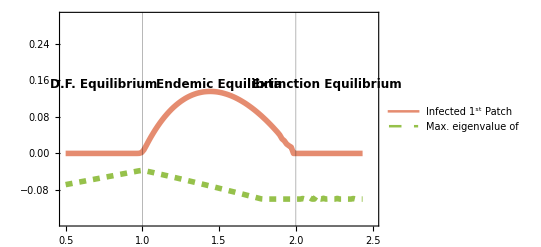

```mathematica
R01s={0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.515,0.515,0.515,0.515,0.515,0.515,0.515,0.515,0.515,0.515,0.53,0.53,0.53,0.53,0.53,0.53,0.53,0.53,0.53,0.53,0.545,0.545,0.545,0.545,0.545,0.545,0.545,0.545,0.545,0.545,0.56,0.56,0.56,0.56,0.56,0.56,0.56,0.56,0.56,0.56,0.575,0.575,0.575,0.575,0.575,0.575,0.575,0.575,0.575,0.575,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.605,0.605,0.605,0.605,0.605,0.605,0.605,0.605,0.605,0.605,0.62,0.62,0.62,0.62,0.62,0.62,0.62,0.62,0.62,0.62,0.635,0.635,0.635,0.635,0.635,0.635,0.635,0.635,0.635,0.635,0.65,0.65,0.65,0.65,0.65,0.65,0.65,0.65,0.65,0.65,0.665,0.665,0.665,0.665,0.665,0.665,0.665,0.665,0.665,0.665,0.68,0.68,0.68,0.68,0.68,0.68,0.68,0.68,0.68,0.68,0.695,0.695,0.695,0.695,0.695,0.695,0.695,0.695,0.695,0.695,0.71,0.71,0.71,0.71,0.71,0.71,0.71,0.71,0.71,0.71,0.725,0.725,0.725,0.725,0.725,0.725,0.725,0.725,0.725,0.725,0.74,0.74,0.74,0.74,0.74,0.74,0.74,0.74,0.74,0.74,0.755,0.755,0.755,0.755,0.755,0.755,0.755,0.755,0.755,0.755,0.77,0.77,0.77,0.77,0.77,0.77,0.77,0.77,0.77,0.77,0.785,0.785,0.785,0.785,0.785,0.785,0.785,0.785,0.785,0.785,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.815,0.815,0.815,0.815,0.815,0.815,0.815,0.815,0.815,0.815,0.83,0.83,0.83,0.83,0.83,0.83,0.83,0.83,0.83,0.83,0.845,0.845,0.845,0.845,0.845,0.845,0.845,0.845,0.845,0.845,0.86,0.86,0.86,0.86,0.86,0.86,0.86,0.86,0.86,0.86,0.875,0.875,0.875,0.875,0.875,0.875,0.875,0.875,0.875,0.875,0.89,0.89,0.89,0.89,0.89,0.89,0.89,0.89,0.89,0.89,0.905,0.905,0.905,0.905,0.905,0.905,0.905,0.905,0.905,0.905,0.92,0.92,0.92,0.92,0.92,0.92,0.92,0.92,0.92,0.92,0.935,0.935,0.935,0.935,0.935,0.935,0.935,0.935,0.935,0.935,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.965,0.965,0.965,0.965,0.965,0.965,0.965,0.965,0.965,0.965,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.98,0.995,0.995,0.995,0.995,0.995,0.995,0.995,0.995,0.995,0.995,1.01,1.01,1.01,1.01,1.01,1.01,1.01,1.01,1.01,1.01,1.025,1.025,1.025,1.025,1.025,1.025,1.025,1.025,1.025,1.025,1.04,1.04,1.04,1.04,1.04,1.04,1.04,1.04,1.04,1.04,1.055,1.055,1.055,1.055,1.055,1.055,1.055,1.055,1.055,1.055,1.07,1.07,1.07,1.07,1.07,1.07,1.07,1.07,1.07,1.07,1.085,1.085,1.085,1.085,1.085,1.085,1.085,1.085,1.085,1.085,1.1,1.1,1.1,1.1,1.1,1.1,1.1,1.1,1.1,1.1,1.115,1.115,1.115,1.115,1.115,1.115,1.115,1.115,1.115,1.115,1.13,1.13,1.13,1.13,1.13,1.13,1.13,1.13,1.13,1.13,1.145,1.145,1.145,1.145,1.145,1.145,1.145,1.145,1.145,1.145,1.16,1.16,1.16,1.16,1.16,1.16,1.16,1.16,1.16,1.16,1.175,1.175,1.175,1.175,1.175,1.175,1.175,1.175,1.175,1.175,1.19,1.19,1.19,1.19,1.19,1.19,1.19,1.19,1.19,1.19,1.205,1.205,1.205,1.205,1.205,1.205,1.205,1.205,1.205,1.205,1.22,1.22,1.22,1.22,1.22,1.22,1.22,1.22,1.22,1.22,1.235,1.235,1.235,1.235,1.235,1.235,1.235,1.235,1.235,1.235,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.265,1.265,1.265,1.265,1.265,1.265,1.265,1.265,1.265,1.265,1.28,1.28,1.28,1.28,1.28,1.28,1.28,1.28,1.28,1.28,1.295,1.295,1.295,1.295,1.295,1.295,1.295,1.295,1.295,1.295,1.31,1.31,1.31,1.31,1.31,1.31,1.31,1.31,1.31,1.31,1.325,1.325,1.325,1.325,1.325,1.325,1.325,1.325,1.325,1.325,1.34,1.34,1.34,1.34,1.34,1.34,1.34,1.34,1.34,1.34,1.355,1.355,1.355,1.355,1.355,1.355,1.355,1.355,1.355,1.355,1.37,1.37,1.37,1.37,1.37,1.37,1.37,1.37,1.37,1.37,1.385,1.385,1.385,1.385,1.385,1.385,1.385,1.385,1.385,1.385,1.4,1.4,1.4,1.4,1.4,1.4,1.4,1.4,1.4,1.4,1.415,1.415,1.415,1.415,1.415,1.415,1.415,1.415,1.415,1.415,1.43,1.43,1.43,1.43,1.43,1.43,1.43,1.43,1.43,1.43,1.445,1.445,1.445,1.445,1.445,1.445,1.445,1.445,1.445,1.445,1.46,1.46,1.46,1.46,1.46,1.46,1.46,1.46,1.46,1.46,1.475,1.475,1.475,1.475,1.475,1.475,1.475,1.475,1.475,1.475,1.49,1.49,1.49,1.49,1.49,1.49,1.49,1.49,1.49,1.49,1.505,1.505,1.505,1.505,1.505,1.505,1.505,1.505,1.505,1.505,1.52,1.52,1.52,1.52,1.52,1.52,1.52,1.52,1.52,1.52,1.535,1.535,1.535,1.535,1.535,1.535,1.535,1.535,1.535,1.535,1.55,1.55,1.55,1.55,1.55,1.55,1.55,1.55,1.55,1.55,1.565,1.565,1.565,1.565,1.565,1.565,1.565,1.565,1.565,1.565,1.58,1.58,1.58,1.58,1.58,1.58,1.58,1.58,1.58,1.58,1.595,1.595,1.595,1.595,1.595,1.595,1.595,1.595,1.595,1.595,1.61,1.61,1.61,1.61,1.61,1.61,1.61,1.61,1.61,1.61,1.625,1.625,1.625,1.625,1.625,1.625,1.625,1.625,1.625,1.625,1.64,1.64,1.64,1.64,1.64,1.64,1.64,1.64,1.64,1.64,1.655,1.655,1.655,1.655,1.655,1.655,1.655,1.655,1.655,1.655,1.67,1.67,1.67,1.67,1.67,1.67,1.67,1.67,1.67,1.67,1.685,1.685,1.685,1.685,1.685,1.685,1.685,1.685,1.685,1.685,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.715,1.715,1.715,1.715,1.715,1.715,1.715,1.715,1.715,1.715,1.73,1.73,1.73,1.73,1.73,1.73,1.73,1.73,1.73,1.73,1.745,1.745,1.745,1.745,1.745,1.745,1.745,1.745,1.745,1.745,1.76,1.76,1.76,1.76,1.76,1.76,1.76,1.76,1.76,1.76,1.775,1.775,1.775,1.775,1.775,1.775,1.775,1.775,1.775,1.775,1.79,1.79,1.79,1.79,1.79,1.79,1.79,1.79,1.79,1.79,1.805,1.805,1.805,1.805,1.805,1.805,1.805,1.805,1.805,1.805,1.82,1.82,1.82,1.82,1.82,1.82,1.82,1.82,1.82,1.82,1.835,1.835,1.835,1.835,1.835,1.835,1.835,1.835,1.835,1.835,1.85,1.85,1.85,1.85,1.85,1.85,1.85,1.85,1.85,1.85,1.865,1.865,1.865,1.865,1.865,1.865,1.865,1.865,1.865,1.865,1.88,1.88,1.88,1.88,1.88,1.88,1.88,1.88,1.88,1.88,1.895,1.895,1.895,1.895,1.895,1.895,1.895,1.895,1.895,1.895,1.91,1.91,1.91,1.91,1.91,1.91,1.91,1.91,1.91,1.91,1.925,1.925,1.925,1.925,1.925,1.925,1.925,1.925,1.925,1.925,1.94,1.94,1.94,1.94,1.94,1.94,1.94,1.94,1.94,1.94,1.955,1.955,1.955,1.955,1.955,1.955,1.955,1.955,1.955,1.955,1.97,1.97,1.97,1.97,1.97,1.97,1.97,1.97,1.97,1.97,1.985,1.985,1.985,1.985,1.985,1.985,1.985,1.985,1.985,1.985,2.0,2.0,2.0,2.0,2.0,2.0,2.0,2.0,2.0,2.0,2.015,2.015,2.015,2.015,2.015,2.015,2.015,2.015,2.015,2.015,2.03,2.03,2.03,2.03,2.03,2.03,2.03,2.03,2.03,2.03,2.045,2.045,2.045,2.045,2.045,2.045,2.045,2.045,2.045,2.045,2.06,2.06,2.06,2.06,2.06,2.06,2.06,2.06,2.06,2.06,2.075,2.075,2.075,2.075,2.075,2.075,2.075,2.075,2.075,2.075,2.09,2.09,2.09,2.09,2.09,2.09,2.09,2.09,2.09,2.09,2.105,2.105,2.105,2.105,2.105,2.105,2.105,2.105,2.105,2.105,2.12,2.12,2.12,2.12,2.12,2.12,2.12,2.12,2.12,2.12,2.135,2.135,2.135,2.135,2.135,2.135,2.135,2.135,2.135,2.135,2.15,2.15,2.15,2.15,2.15,2.15,2.15,2.15,2.15,2.15,2.165,2.165,2.165,2.165,2.165,2.165,2.165,2.165,2.165,2.165,2.18,2.18,2.18,2.18,2.18,2.18,2.18,2.18,2.18,2.18,2.195,2.195,2.195,2.195,2.195,2.195,2.195,2.195,2.195,2.195,2.21,2.21,2.21,2.21,2.21,2.21,2.21,2.21,2.21,2.21,2.225,2.225,2.225,2.225,2.225,2.225,2.225,2.225,2.225,2.225,2.24,2.24,2.24,2.24,2.24,2.24,2.24,2.24,2.24,2.24,2.255,2.255,2.255,2.255,2.255,2.255,2.255,2.255,2.255,2.255,2.27,2.27,2.27,2.27,2.27,2.27,2.27,2.27,2.27,2.27,2.285,2.285,2.285,2.285,2.285,2.285,2.285,2.285,2.285,2.285,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.315,2.315,2.315,2.315,2.315,2.315,2.315,2.315,2.315,2.315,2.33,2.33,2.33,2.33,2.33,2.33,2.33,2.33,2.33,2.33,2.345,2.345,2.345,2.345,2.345,2.345,2.345,2.345,2.345,2.345,2.36,2.36,2.36,2.36,2.36,2.36,2.36,2.36,2.36,2.36,2.375,2.375,2.375,2.375,2.375,2.375,2.375,2.375,2.375,2.375,2.39,2.39,2.39,2.39,2.39,2.39,2.39,2.39,2.39,2.39,2.405,2.405,2.405,2.405,2.405,2.405,2.405,2.405,2.405,2.405,2.42,2.42,2.42,2.42,2.42,2.42,2.42,2.42,2.42,2.42,2.435,2.435,2.435,2.435,2.435,2.435,2.435,2.435,2.435,2.435};

infP1={0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.0002,0.002,0.002,0.002,0.0016,0.002,0.0018,0.0019,0.002,0.0018,0.0019,0.0079,0.0079,0.0079,0.0079,0.008,0.008,0.008,0.0079,0.008,0.0079,0.0171,0.0171,0.0171,0.0171,0.0171,0.0171,0.0171,0.0171,0.0171,0.0171,0.0266,0.0266,0.0266,0.0266,0.0266,0.0266,0.0266,0.0266,0.0266,0.0266,0.0356,0.0356,0.0356,0.0356,0.0356,0.0356,0.0356,0.0356,0.0356,0.0356,0.0441,0.0441,0.0441,0.0441,0.0441,0.0441,0.0441,0.0441,0.0441,0.0441,0.0522,0.0522,0.0522,0.0522,0.0522,0.0522,0.0522,0.0522,0.0522,0.0522,0.0598,0.0598,0.0598,0.0598,0.0598,0.0598,0.0598,0.0598,0.0598,0.0598,0.067,0.067,0.067,0.067,0.067,0.067,0.067,0.067,0.067,0.067,0.0737,0.0737,0.0737,0.0737,0.0737,0.0737,0.0737,0.0737,0.0737,0.0737,0.0801,0.0801,0.0801,0.0801,0.0801,0.0801,0.0801,0.0801,0.0801,0.0801,0.086,0.086,0.086,0.086,0.086,0.086,0.086,0.086,0.086,0.086,0.0916,0.0916,0.0916,0.0916,0.0916,0.0916,0.0916,0.0916,0.0916,0.0916,0.0968,0.0968,0.0968,0.0968,0.0968,0.0968,0.0968,0.0968,0.0968,0.0968,0.1016,0.1016,0.1016,0.1016,0.1016,0.1016,0.1016,0.1016,0.1016,0.1016,0.106,0.106,0.106,0.106,0.106,0.106,0.106,0.106,0.106,0.106,0.1101,0.1101,0.1101,0.1101,0.1101,0.1101,0.1101,0.1101,0.1101,0.1101,0.1139,0.1139,0.1139,0.1139,0.1139,0.1139,0.1139,0.1139,0.1139,0.1139,0.1173,0.1173,0.1173,0.1173,0.1173,0.1173,0.1173,0.1173,0.1173,0.1173,0.1205,0.1205,0.1205,0.1205,0.1205,0.1205,0.1205,0.1205,0.1205,0.1205,0.1233,0.1233,0.1233,0.1233,0.1233,0.1233,0.1233,0.1233,0.1233,0.1233,0.1258,0.1258,0.1258,0.1258,0.1258,0.1258,0.1258,0.1258,0.1258,0.1258,0.128,0.128,0.128,0.128,0.128,0.128,0.128,0.128,0.128,0.128,0.1299,0.1299,0.1299,0.1299,0.1299,0.1299,0.1299,0.1299,0.1299,0.1299,0.1316,0.1316,0.1316,0.1316,0.1316,0.1316,0.1316,0.1316,0.1316,0.1316,0.1329,0.1329,0.1329,0.1329,0.1329,0.1329,0.1329,0.1329,0.1329,0.1329,0.134,0.134,0.134,0.134,0.134,0.134,0.134,0.134,0.134,0.134,0.1349,0.1349,0.1349,0.1349,0.1349,0.1349,0.1349,0.1349,0.1349,0.1349,0.1354,0.1354,0.1354,0.1354,0.1354,0.1354,0.1354,0.1354,0.1354,0.1354,0.1357,0.1357,0.1357,0.1357,0.1357,0.1357,0.1357,0.1357,0.1357,0.1357,0.1358,0.1358,0.1358,0.1358,0.1358,0.1358,0.1358,0.1358,0.1358,0.1358,0.1356,0.1356,0.1356,0.1356,0.1356,0.1356,0.1356,0.1356,0.1356,0.1356,0.1352,0.1352,0.1352,0.1352,0.1352,0.1352,0.1352,0.1352,0.1352,0.1352,0.1346,0.1346,0.1346,0.1346,0.1346,0.1346,0.1346,0.1346,0.1346,0.1346,0.1337,0.1337,0.1337,0.1337,0.1337,0.1337,0.1337,0.1337,0.1337,0.1337,0.1326,0.1326,0.1326,0.1326,0.1326,0.1326,0.1326,0.1326,0.1326,0.1326,0.1312,0.1312,0.1312,0.1312,0.1312,0.1312,0.1312,0.1312,0.1312,0.1312,0.1297,0.1297,0.1297,0.1297,0.1297,0.1297,0.1297,0.1297,0.1297,0.1297,0.1279,0.1279,0.1279,0.1279,0.1279,0.1279,0.1279,0.1279,0.1279,0.1279,0.126,0.126,0.126,0.126,0.126,0.126,0.126,0.126,0.126,0.126,0.1238,0.1238,0.1238,0.1238,0.1238,0.1238,0.1238,0.1238,0.1238,0.1238,0.1214,0.1214,0.1214,0.1214,0.1214,0.1214,0.1214,0.1214,0.1214,0.1214,0.1188,0.1188,0.1188,0.1188,0.1188,0.1188,0.1188,0.1188,0.1188,0.1188,0.116,0.116,0.116,0.116,0.116,0.116,0.116,0.116,0.116,0.116,0.113,0.113,0.113,0.113,0.113,0.113,0.113,0.113,0.113,0.113,0.1099,0.1099,0.1099,0.1099,0.1099,0.1099,0.1099,0.1099,0.1099,0.1099,0.1065,0.1065,0.1065,0.1065,0.1065,0.1065,0.1065,0.1065,0.1065,0.1065,0.1029,0.1029,0.1029,0.1029,0.1029,0.1029,0.1029,0.1029,0.1029,0.1029,0.0992,0.0992,0.0992,0.0992,0.0992,0.0992,0.0992,0.0992,0.0992,0.0992,0.0953,0.0953,0.0953,0.0953,0.0953,0.0953,0.0953,0.0953,0.0953,0.0953,0.0912,0.0912,0.0912,0.0912,0.0912,0.0912,0.0912,0.0912,0.0912,0.0912,0.0869,0.0869,0.0869,0.0869,0.0869,0.0869,0.0869,0.0869,0.0869,0.0869,0.0825,0.0825,0.0825,0.0825,0.0825,0.0825,0.0825,0.0825,0.0825,0.0825,0.0778,0.0778,0.0778,0.0778,0.0778,0.0778,0.0778,0.0778,0.0778,0.0778,0.0731,0.0731,0.0731,0.0731,0.0731,0.0731,0.073,0.0731,0.0731,0.0731,0.0681,0.0681,0.0681,0.0681,0.0681,0.0681,0.0681,0.0681,0.0681,0.0681,0.063,0.063,0.063,0.063,0.063,0.063,0.063,0.063,0.063,0.063,0.0577,0.0577,0.0577,0.0577,0.0577,0.0577,0.0577,0.0577,0.0577,0.0576,0.0522,0.0522,0.0524,0.0522,0.0521,0.0522,0.0521,0.0522,0.0521,0.0522,0.0462,0.0467,0.0467,0.0468,0.0467,0.0467,0.0467,0.0466,0.0467,0.0467,0.0408,0.0405,0.0404,0.0406,0.0405,0.0403,0.0408,0.0404,0.0404,0.0405,0.0356,0.0358,0.0338,0.0353,-0.0,0.0356,0.0357,0.0359,0.0357,0.0356,0.0277,0.0276,0.0274,0.0291,0.0243,0.0274,0.0274,0.0296,0.0278,0.0276,0.0182,0.0183,0.0218,0.0216,0.0185,0.0221,0.0179,0.0306,0.0177,0.0191,0.0127,0.0089,0.0084,0.0396,0.0394,0.0166,0.0147,0.0114,0.0077,0.0084,0.0,0.0489,0.0003,0.011,-0.0,-0.0,0.0035,0.0356,0.0356,0.0016,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0};

maxeigs1={-0.0684,-0.0684,-0.0684,-0.0684,-0.0684,-0.0684,-0.0684,-0.0684,-0.0684,-0.0684,-0.0674,-0.0674,-0.0674,-0.0674,-0.0674,-0.0674,-0.0674,-0.0674,-0.0674,-0.0674,-0.0665,-0.0665,-0.0665,-0.0665,-0.0665,-0.0665,-0.0665,-0.0665,-0.0665,-0.0665,-0.0655,-0.0655,-0.0655,-0.0655,-0.0655,-0.0655,-0.0655,-0.0655,-0.0655,-0.0655,-0.0646,-0.0646,-0.0646,-0.0646,-0.0646,-0.0646,-0.0646,-0.0646,-0.0646,-0.0646,-0.0636,-0.0636,-0.0636,-0.0636,-0.0636,-0.0636,-0.0636,-0.0636,-0.0636,-0.0636,-0.0627,-0.0627,-0.0627,-0.0627,-0.0627,-0.0627,-0.0627,-0.0627,-0.0627,-0.0627,-0.0617,-0.0617,-0.0617,-0.0617,-0.0617,-0.0617,-0.0617,-0.0617,-0.0617,-0.0617,-0.0608,-0.0608,-0.0608,-0.0608,-0.0608,-0.0608,-0.0608,-0.0608,-0.0608,-0.0608,-0.0598,-0.0598,-0.0598,-0.0598,-0.0598,-0.0598,-0.0598,-0.0598,-0.0598,-0.0598,-0.0589,-0.0589,-0.0589,-0.0589,-0.0589,-0.0589,-0.0589,-0.0589,-0.0589,-0.0589,-0.0579,-0.0579,-0.0579,-0.0579,-0.0579,-0.0579,-0.0579,-0.0579,-0.0579,-0.0579,-0.057,-0.057,-0.057,-0.057,-0.057,-0.057,-0.057,-0.057,-0.057,-0.057,-0.056,-0.056,-0.056,-0.056,-0.056,-0.056,-0.056,-0.056,-0.056,-0.056,-0.0551,-0.0551,-0.0551,-0.0551,-0.0551,-0.0551,-0.0551,-0.0551,-0.0551,-0.0551,-0.0541,-0.0541,-0.0541,-0.0541,-0.0541,-0.0541,-0.0541,-0.0541,-0.0541,-0.0541,-0.0532,-0.0532,-0.0532,-0.0532,-0.0532,-0.0532,-0.0532,-0.0532,-0.0532,-0.0532,-0.0522,-0.0522,-0.0522,-0.0522,-0.0522,-0.0522,-0.0522,-0.0522,-0.0522,-0.0522,-0.0513,-0.0513,-0.0513,-0.0513,-0.0513,-0.0513,-0.0513,-0.0513,-0.0513,-0.0513,-0.0503,-0.0503,-0.0503,-0.0503,-0.0503,-0.0503,-0.0503,-0.0503,-0.0503,-0.0503,-0.0494,-0.0494,-0.0494,-0.0494,-0.0494,-0.0494,-0.0494,-0.0494,-0.0494,-0.0494,-0.0484,-0.0484,-0.0484,-0.0484,-0.0484,-0.0484,-0.0484,-0.0484,-0.0484,-0.0484,-0.0475,-0.0475,-0.0475,-0.0475,-0.0475,-0.0475,-0.0475,-0.0475,-0.0475,-0.0475,-0.0465,-0.0465,-0.0465,-0.0465,-0.0465,-0.0465,-0.0465,-0.0465,-0.0465,-0.0465,-0.0456,-0.0456,-0.0456,-0.0456,-0.0456,-0.0456,-0.0456,-0.0456,-0.0456,-0.0456,-0.0446,-0.0446,-0.0446,-0.0446,-0.0446,-0.0446,-0.0446,-0.0446,-0.0446,-0.0446,-0.0437,-0.0437,-0.0437,-0.0437,-0.0437,-0.0437,-0.0437,-0.0437,-0.0437,-0.0437,-0.0427,-0.0427,-0.0427,-0.0427,-0.0427,-0.0427,-0.0427,-0.0427,-0.0427,-0.0427,-0.0418,-0.0418,-0.0418,-0.0418,-0.0418,-0.0418,-0.0418,-0.0418,-0.0418,-0.0418,-0.0408,-0.0408,-0.0408,-0.0408,-0.0408,-0.0408,-0.0408,-0.0408,-0.0408,-0.0408,-0.0399,-0.0399,-0.0399,-0.0399,-0.0399,-0.0399,-0.0399,-0.0399,-0.0399,-0.0399,-0.0389,-0.0389,-0.0389,-0.0389,-0.0389,-0.0389,-0.0389,-0.0389,-0.0389,-0.0389,-0.038,-0.038,-0.038,-0.038,-0.038,-0.038,-0.038,-0.038,-0.038,-0.038,-0.0374,-0.0374,-0.0374,-0.0373,-0.0374,-0.0374,-0.0374,-0.0374,-0.0374,-0.0374,-0.0376,-0.0376,-0.0376,-0.0376,-0.0376,-0.0376,-0.0376,-0.0376,-0.0376,-0.0376,-0.0386,-0.0386,-0.0386,-0.0386,-0.0386,-0.0386,-0.0386,-0.0386,-0.0386,-0.0386,-0.0397,-0.0397,-0.0397,-0.0397,-0.0397,-0.0397,-0.0397,-0.0397,-0.0397,-0.0397,-0.0408,-0.0408,-0.0408,-0.0408,-0.0408,-0.0408,-0.0408,-0.0408,-0.0408,-0.0408,-0.0419,-0.0419,-0.0419,-0.0419,-0.0419,-0.0419,-0.0419,-0.0419,-0.0419,-0.0419,-0.0431,-0.0431,-0.0431,-0.0431,-0.0431,-0.0431,-0.0431,-0.0431,-0.0431,-0.0431,-0.0442,-0.0442,-0.0442,-0.0442,-0.0442,-0.0442,-0.0442,-0.0442,-0.0442,-0.0442,-0.0454,-0.0454,-0.0454,-0.0454,-0.0454,-0.0454,-0.0454,-0.0454,-0.0454,-0.0454,-0.0465,-0.0465,-0.0465,-0.0465,-0.0465,-0.0465,-0.0465,-0.0465,-0.0465,-0.0465,-0.0477,-0.0477,-0.0477,-0.0477,-0.0477,-0.0477,-0.0477,-0.0477,-0.0477,-0.0477,-0.0488,-0.0488,-0.0488,-0.0488,-0.0488,-0.0488,-0.0488,-0.0488,-0.0488,-0.0488,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.0512,-0.0512,-0.0512,-0.0512,-0.0512,-0.0512,-0.0512,-0.0512,-0.0512,-0.0512,-0.0524,-0.0524,-0.0524,-0.0524,-0.0524,-0.0524,-0.0524,-0.0524,-0.0524,-0.0524,-0.0535,-0.0535,-0.0535,-0.0535,-0.0535,-0.0535,-0.0535,-0.0535,-0.0535,-0.0535,-0.0547,-0.0547,-0.0547,-0.0547,-0.0547,-0.0547,-0.0547,-0.0547,-0.0547,-0.0547,-0.0559,-0.0559,-0.0559,-0.0559,-0.0559,-0.0559,-0.0559,-0.0559,-0.0559,-0.0559,-0.0571,-0.0571,-0.0571,-0.0571,-0.0571,-0.0571,-0.0571,-0.0571,-0.0571,-0.0571,-0.0583,-0.0583,-0.0583,-0.0583,-0.0583,-0.0583,-0.0583,-0.0583,-0.0583,-0.0583,-0.0595,-0.0595,-0.0595,-0.0595,-0.0595,-0.0595,-0.0595,-0.0595,-0.0595,-0.0595,-0.0607,-0.0607,-0.0607,-0.0607,-0.0607,-0.0607,-0.0607,-0.0607,-0.0607,-0.0607,-0.0619,-0.0619,-0.0619,-0.0619,-0.0619,-0.0619,-0.0619,-0.0619,-0.0619,-0.0619,-0.0631,-0.0631,-0.0631,-0.0631,-0.0631,-0.0631,-0.0631,-0.0631,-0.0631,-0.0631,-0.0643,-0.0643,-0.0643,-0.0643,-0.0643,-0.0643,-0.0643,-0.0643,-0.0643,-0.0643,-0.0655,-0.0655,-0.0655,-0.0655,-0.0655,-0.0655,-0.0655,-0.0655,-0.0655,-0.0655,-0.0668,-0.0668,-0.0668,-0.0668,-0.0668,-0.0668,-0.0668,-0.0668,-0.0668,-0.0668,-0.068,-0.068,-0.068,-0.068,-0.068,-0.068,-0.068,-0.068,-0.068,-0.068,-0.0692,-0.0692,-0.0692,-0.0692,-0.0692,-0.0692,-0.0692,-0.0692,-0.0692,-0.0692,-0.0705,-0.0705,-0.0705,-0.0705,-0.0705,-0.0705,-0.0705,-0.0705,-0.0705,-0.0705,-0.0717,-0.0717,-0.0717,-0.0717,-0.0717,-0.0717,-0.0717,-0.0717,-0.0717,-0.0717,-0.0729,-0.0729,-0.0729,-0.0729,-0.0729,-0.0729,-0.0729,-0.0729,-0.0729,-0.0729,-0.0742,-0.0742,-0.0742,-0.0742,-0.0742,-0.0742,-0.0742,-0.0742,-0.0742,-0.0742,-0.0754,-0.0754,-0.0754,-0.0754,-0.0754,-0.0754,-0.0754,-0.0754,-0.0754,-0.0754,-0.0767,-0.0767,-0.0767,-0.0767,-0.0767,-0.0767,-0.0767,-0.0767,-0.0767,-0.0767,-0.0779,-0.0779,-0.0779,-0.0779,-0.0779,-0.0779,-0.0779,-0.0779,-0.0779,-0.0779,-0.0792,-0.0792,-0.0792,-0.0792,-0.0792,-0.0792,-0.0792,-0.0792,-0.0792,-0.0792,-0.0804,-0.0804,-0.0804,-0.0804,-0.0804,-0.0804,-0.0804,-0.0804,-0.0804,-0.0804,-0.0817,-0.0817,-0.0817,-0.0817,-0.0817,-0.0817,-0.0817,-0.0817,-0.0817,-0.0817,-0.083,-0.083,-0.083,-0.083,-0.083,-0.083,-0.083,-0.083,-0.083,-0.083,-0.0842,-0.0842,-0.0842,-0.0842,-0.0842,-0.0842,-0.0842,-0.0842,-0.0842,-0.0842,-0.0855,-0.0855,-0.0855,-0.0855,-0.0855,-0.0855,-0.0855,-0.0855,-0.0855,-0.0855,-0.0868,-0.0868,-0.0868,-0.0868,-0.0868,-0.0868,-0.0868,-0.0868,-0.0868,-0.0868,-0.088,-0.088,-0.088,-0.088,-0.088,-0.088,-0.088,-0.088,-0.088,-0.088,-0.0893,-0.0893,-0.0893,-0.0893,-0.0893,-0.0893,-0.0893,-0.0893,-0.0893,-0.0893,-0.0906,-0.0906,-0.0906,-0.0906,-0.0906,-0.0906,-0.0906,-0.0906,-0.0906,-0.0906,-0.0919,-0.0919,-0.0919,-0.0919,-0.0919,-0.0919,-0.0919,-0.0919,-0.0919,-0.0919,-0.0932,-0.0932,-0.0932,-0.0932,-0.0932,-0.0932,-0.0932,-0.0932,-0.0932,-0.0932,-0.0945,-0.0945,-0.0945,-0.0945,-0.0945,-0.0945,-0.0945,-0.0945,-0.0945,-0.0945,-0.0957,-0.0957,-0.0957,-0.0957,-0.0957,-0.0957,-0.0957,-0.0957,-0.0957,-0.0957,-0.097,-0.097,-0.097,-0.097,-0.097,-0.097,-0.097,-0.097,-0.097,-0.097,-0.0983,-0.0983,-0.0983,-0.0983,-0.0983,-0.0983,-0.0983,-0.0983,-0.0983,-0.0983,-0.0996,-0.0996,-0.0996,-0.0996,-0.0996,-0.0996,-0.0996,-0.0996,-0.0996,-0.0996,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.0875,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.0933,-0.0933,-0.1,-0.1,-0.1,-0.0827,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.0635,-0.0635,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.0906,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.0829,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.0972,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.0997,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.0848,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.0926,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.0997,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.0881,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1};

tdbinfmaxeigs1=TemporalData[{infP1, maxeigs1},{{R01s },{R01s }}];
maxEigsGraph1= ListLinePlot[ tdbinfmaxeigs1,
PlotStyle->{ 
Directive[Thickness[0.01],ToColor[RGBColor["#E58C70"],Hue]],
Directive[Thickness[0.01],Dashed,ToColor[RGBColor["#96C14B"],Hue]]
},
Frame->{True,True,False,False},
FrameLabel->{Style["", Black, 18 ], None},
Axes->False,
LabelStyle->Directive[Bold, Medium, Black],
PlotRange->{{0.5,2.5},{-0.15, 0.3}},
TicksStyle->Directive[Bold, 12],GridLines->{{{2,Black}, {1,Black}},None},
PlotLegends->Placed[{
Style["Infected 1^st Patch",FontFamily->"Century",16],
Style["Max. eigenvalue of ",FontFamily->"Century",16]
}, {Center,Top}],
ImageSize->{600}, Epilog->{Text[Style["Endemic Equilibria",Small,Bold,Black,12],{1.5,0.15}], 
Text[Style["D.F. Equilibrium",Small,Bold,Black, 12],{0.75,0.15}], 
Text[Style["Extinction Equilibrium",Small,Bold,Black,12],{2.2,0.15}]}];
Export["C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/picno/Plots/maxEigsGraph1.pdf",maxEigsGraph1,"PDF","AllowRasterization"->False];
maxEigsGraph1
```

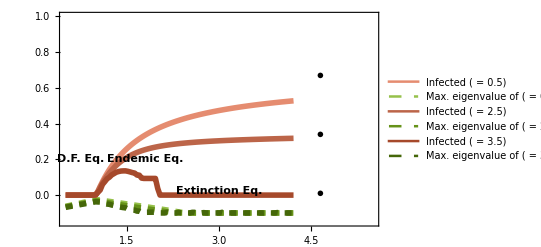

```mathematica
R02s={0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5375,0.5375,0.5375,0.5375,0.5375,0.5375,0.5375,0.5375,0.5375,0.5375,0.575,0.575,0.575,0.575,0.575,0.575,0.575,0.575,0.575,0.575,0.6125,0.6125,0.6125,0.6125,0.6125,0.6125,0.6125,0.6125,0.6125,0.6125,0.65,0.65,0.65,0.65,0.65,0.65,0.65,0.65,0.65,0.65,0.6875,0.6875,0.6875,0.6875,0.6875,0.6875,0.6875,0.6875,0.6875,0.6875,0.725,0.725,0.725,0.725,0.725,0.725,0.725,0.725,0.725,0.725,0.7625,0.7625,0.7625,0.7625,0.7625,0.7625,0.7625,0.7625,0.7625,0.7625,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8375,0.8375,0.8375,0.8375,0.8375,0.8375,0.8375,0.8375,0.8375,0.8375,0.875,0.875,0.875,0.875,0.875,0.875,0.875,0.875,0.875,0.875,0.9125,0.9125,0.9125,0.9125,0.9125,0.9125,0.9125,0.9125,0.9125,0.9125,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.9875,0.9875,0.9875,0.9875,0.9875,0.9875,0.9875,0.9875,0.9875,0.9875,1.025,1.025,1.025,1.025,1.025,1.025,1.025,1.025,1.025,1.025,1.0625,1.0625,1.0625,1.0625,1.0625,1.0625,1.0625,1.0625,1.0625,1.0625,1.1,1.1,1.1,1.1,1.1,1.1,1.1,1.1,1.1,1.1,1.1375,1.1375,1.1375,1.1375,1.1375,1.1375,1.1375,1.1375,1.1375,1.1375,1.175,1.175,1.175,1.175,1.175,1.175,1.175,1.175,1.175,1.175,1.2125,1.2125,1.2125,1.2125,1.2125,1.2125,1.2125,1.2125,1.2125,1.2125,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.2875,1.2875,1.2875,1.2875,1.2875,1.2875,1.2875,1.2875,1.2875,1.2875,1.325,1.325,1.325,1.325,1.325,1.325,1.325,1.325,1.325,1.325,1.3625,1.3625,1.3625,1.3625,1.3625,1.3625,1.3625,1.3625,1.3625,1.3625,1.4,1.4,1.4,1.4,1.4,1.4,1.4,1.4,1.4,1.4,1.4375,1.4375,1.4375,1.4375,1.4375,1.4375,1.4375,1.4375,1.4375,1.4375,1.475,1.475,1.475,1.475,1.475,1.475,1.475,1.475,1.475,1.475,1.5125,1.5125,1.5125,1.5125,1.5125,1.5125,1.5125,1.5125,1.5125,1.5125,1.55,1.55,1.55,1.55,1.55,1.55,1.55,1.55,1.55,1.55,1.5875,1.5875,1.5875,1.5875,1.5875,1.5875,1.5875,1.5875,1.5875,1.5875,1.625,1.625,1.625,1.625,1.625,1.625,1.625,1.625,1.625,1.625,1.6625,1.6625,1.6625,1.6625,1.6625,1.6625,1.6625,1.6625,1.6625,1.6625,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7375,1.7375,1.7375,1.7375,1.7375,1.7375,1.7375,1.7375,1.7375,1.7375,1.775,1.775,1.775,1.775,1.775,1.775,1.775,1.775,1.775,1.775,1.8125,1.8125,1.8125,1.8125,1.8125,1.8125,1.8125,1.8125,1.8125,1.8125,1.85,1.85,1.85,1.85,1.85,1.85,1.85,1.85,1.85,1.85,1.8875,1.8875,1.8875,1.8875,1.8875,1.8875,1.8875,1.8875,1.8875,1.8875,1.925,1.925,1.925,1.925,1.925,1.925,1.925,1.925,1.925,1.925,1.9625,1.9625,1.9625,1.9625,1.9625,1.9625,1.9625,1.9625,1.9625,1.9625,2.0,2.0,2.0,2.0,2.0,2.0,2.0,2.0,2.0,2.0,2.0375,2.0375,2.0375,2.0375,2.0375,2.0375,2.0375,2.0375,2.0375,2.0375,2.075,2.075,2.075,2.075,2.075,2.075,2.075,2.075,2.075,2.075,2.1125,2.1125,2.1125,2.1125,2.1125,2.1125,2.1125,2.1125,2.1125,2.1125,2.15,2.15,2.15,2.15,2.15,2.15,2.15,2.15,2.15,2.15,2.1875,2.1875,2.1875,2.1875,2.1875,2.1875,2.1875,2.1875,2.1875,2.1875,2.225,2.225,2.225,2.225,2.225,2.225,2.225,2.225,2.225,2.225,2.2625,2.2625,2.2625,2.2625,2.2625,2.2625,2.2625,2.2625,2.2625,2.2625,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.3375,2.3375,2.3375,2.3375,2.3375,2.3375,2.3375,2.3375,2.3375,2.3375,2.375,2.375,2.375,2.375,2.375,2.375,2.375,2.375,2.375,2.375,2.4125,2.4125,2.4125,2.4125,2.4125,2.4125,2.4125,2.4125,2.4125,2.4125,2.45,2.45,2.45,2.45,2.45,2.45,2.45,2.45,2.45,2.45,2.4875,2.4875,2.4875,2.4875,2.4875,2.4875,2.4875,2.4875,2.4875,2.4875,2.525,2.525,2.525,2.525,2.525,2.525,2.525,2.525,2.525,2.525,2.5625,2.5625,2.5625,2.5625,2.5625,2.5625,2.5625,2.5625,2.5625,2.5625,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.6375,2.6375,2.6375,2.6375,2.6375,2.6375,2.6375,2.6375,2.6375,2.6375,2.675,2.675,2.675,2.675,2.675,2.675,2.675,2.675,2.675,2.675,2.7125,2.7125,2.7125,2.7125,2.7125,2.7125,2.7125,2.7125,2.7125,2.7125,2.75,2.75,2.75,2.75,2.75,2.75,2.75,2.75,2.75,2.75,2.7875,2.7875,2.7875,2.7875,2.7875,2.7875,2.7875,2.7875,2.7875,2.7875,2.825,2.825,2.825,2.825,2.825,2.825,2.825,2.825,2.825,2.825,2.8625,2.8625,2.8625,2.8625,2.8625,2.8625,2.8625,2.8625,2.8625,2.8625,2.9,2.9,2.9,2.9,2.9,2.9,2.9,2.9,2.9,2.9,2.9375,2.9375,2.9375,2.9375,2.9375,2.9375,2.9375,2.9375,2.9375,2.9375,2.975,2.975,2.975,2.975,2.975,2.975,2.975,2.975,2.975,2.975,3.0125,3.0125,3.0125,3.0125,3.0125,3.0125,3.0125,3.0125,3.0125,3.0125,3.05,3.05,3.05,3.05,3.05,3.05,3.05,3.05,3.05,3.05,3.0875,3.0875,3.0875,3.0875,3.0875,3.0875,3.0875,3.0875,3.0875,3.0875,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.1625,3.1625,3.1625,3.1625,3.1625,3.1625,3.1625,3.1625,3.1625,3.1625,3.2,3.2,3.2,3.2,3.2,3.2,3.2,3.2,3.2,3.2,3.2375,3.2375,3.2375,3.2375,3.2375,3.2375,3.2375,3.2375,3.2375,3.2375,3.275,3.275,3.275,3.275,3.275,3.275,3.275,3.275,3.275,3.275,3.3125,3.3125,3.3125,3.3125,3.3125,3.3125,3.3125,3.3125,3.3125,3.3125,3.35,3.35,3.35,3.35,3.35,3.35,3.35,3.35,3.35,3.35,3.3875,3.3875,3.3875,3.3875,3.3875,3.3875,3.3875,3.3875,3.3875,3.3875,3.425,3.425,3.425,3.425,3.425,3.425,3.425,3.425,3.425,3.425,3.4625,3.4625,3.4625,3.4625,3.4625,3.4625,3.4625,3.4625,3.4625,3.4625,3.5,3.5,3.5,3.5,3.5,3.5,3.5,3.5,3.5,3.5,3.5375,3.5375,3.5375,3.5375,3.5375,3.5375,3.5375,3.5375,3.5375,3.5375,3.575,3.575,3.575,3.575,3.575,3.575,3.575,3.575,3.575,3.575,3.6125,3.6125,3.6125,3.6125,3.6125,3.6125,3.6125,3.6125,3.6125,3.6125,3.65,3.65,3.65,3.65,3.65,3.65,3.65,3.65,3.65,3.65,3.6875,3.6875,3.6875,3.6875,3.6875,3.6875,3.6875,3.6875,3.6875,3.6875,3.725,3.725,3.725,3.725,3.725,3.725,3.725,3.725,3.725,3.725,3.7625,3.7625,3.7625,3.7625,3.7625,3.7625,3.7625,3.7625,3.7625,3.7625,3.8,3.8,3.8,3.8,3.8,3.8,3.8,3.8,3.8,3.8,3.8375,3.8375,3.8375,3.8375,3.8375,3.8375,3.8375,3.8375,3.8375,3.8375,3.875,3.875,3.875,3.875,3.875,3.875,3.875,3.875,3.875,3.875,3.9125,3.9125,3.9125,3.9125,3.9125,3.9125,3.9125,3.9125,3.9125,3.9125,3.95,3.95,3.95,3.95,3.95,3.95,3.95,3.95,3.95,3.95,3.9875,3.9875,3.9875,3.9875,3.9875,3.9875,3.9875,3.9875,3.9875,3.9875,4.025,4.025,4.025,4.025,4.025,4.025,4.025,4.025,4.025,4.025,4.0625,4.0625,4.0625,4.0625,4.0625,4.0625,4.0625,4.0625,4.0625,4.0625,4.1,4.1,4.1,4.1,4.1,4.1,4.1,4.1,4.1,4.1,4.1375,4.1375,4.1375,4.1375,4.1375,4.1375,4.1375,4.1375,4.1375,4.1375,4.175,4.175,4.175,4.175,4.175,4.175,4.175,4.175,4.175,4.175,4.2125,4.2125,4.2125,4.2125,4.2125,4.2125,4.2125,4.2125,4.2125,4.2125};

infP2={-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0009,0.0009,0.0009,0.0009,0.0009,0.0009,0.0009,0.0009,0.0009,0.0009,0.0206,0.0206,0.0206,0.0206,0.0206,0.0206,0.0206,0.0206,0.0206,0.0206,0.0491,0.0491,0.0491,0.0491,0.0491,0.0491,0.0491,0.0491,0.0491,0.0491,0.0753,0.0753,0.0753,0.0753,0.0753,0.0753,0.0753,0.0753,0.0753,0.0753,0.0995,0.0995,0.0995,0.0995,0.0995,0.0995,0.0995,0.0995,0.0995,0.0995,0.1219,0.1219,0.1219,0.1219,0.1219,0.1219,0.1219,0.1219,0.1219,0.1219,0.1426,0.1426,0.1426,0.1426,0.1426,0.1426,0.1426,0.1426,0.1426,0.1426,0.1618,0.1618,0.1618,0.1618,0.1618,0.1618,0.1618,0.1618,0.1618,0.1618,0.1796,0.1796,0.1796,0.1796,0.1796,0.1796,0.1796,0.1796,0.1796,0.1796,0.1963,0.1963,0.1963,0.1963,0.1963,0.1963,0.1963,0.1963,0.1963,0.1963,0.2118,0.2118,0.2118,0.2118,0.2118,0.2118,0.2118,0.2118,0.2118,0.2118,0.2263,0.2263,0.2263,0.2263,0.2263,0.2263,0.2263,0.2263,0.2263,0.2263,0.2399,0.2399,0.2399,0.2399,0.2399,0.2399,0.2399,0.2399,0.2399,0.2399,0.2526,0.2526,0.2526,0.2526,0.2526,0.2526,0.2526,0.2526,0.2526,0.2526,0.2646,0.2646,0.2646,0.2646,0.2646,0.2646,0.2646,0.2646,0.2646,0.2646,0.2759,0.2759,0.2759,0.2759,0.2759,0.2759,0.2759,0.2759,0.2759,0.2759,0.2866,0.2866,0.2866,0.2866,0.2866,0.2866,0.2866,0.2866,0.2866,0.2866,0.2966,0.2966,0.2966,0.2966,0.2966,0.2966,0.2966,0.2966,0.2966,0.2966,0.3061,0.3061,0.3061,0.3061,0.3061,0.3061,0.3061,0.3061,0.3061,0.3061,0.3152,0.3152,0.3152,0.3152,0.3152,0.3152,0.3152,0.3152,0.3152,0.3152,0.3237,0.3237,0.3237,0.3237,0.3237,0.3237,0.3237,0.3237,0.3237,0.3237,0.3318,0.3318,0.3318,0.3318,0.3318,0.3318,0.3318,0.3318,0.3318,0.3318,0.3395,0.3395,0.3395,0.3395,0.3395,0.3395,0.3395,0.3395,0.3395,0.3395,0.3469,0.3469,0.3469,0.3469,0.3469,0.3469,0.3469,0.3469,0.3469,0.3469,0.3539,0.3539,0.3539,0.3539,0.3539,0.3539,0.3539,0.3539,0.3539,0.3539,0.3605,0.3605,0.3605,0.3605,0.3605,0.3605,0.3605,0.3605,0.3605,0.3605,0.3669,0.3669,0.3669,0.3669,0.3669,0.3669,0.3669,0.3669,0.3669,0.3669,0.373,0.373,0.373,0.373,0.373,0.373,0.373,0.373,0.373,0.373,0.3789,0.3789,0.3789,0.3789,0.3789,0.3789,0.3789,0.3789,0.3789,0.3789,0.3844,0.3844,0.3844,0.3844,0.3844,0.3844,0.3844,0.3844,0.3844,0.3844,0.3898,0.3898,0.3898,0.3898,0.3898,0.3898,0.3898,0.3898,0.3898,0.3898,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.3999,0.3999,0.3999,0.3999,0.3999,0.3999,0.3999,0.3999,0.3999,0.3999,0.4046,0.4046,0.4046,0.4046,0.4046,0.4046,0.4046,0.4046,0.4046,0.4046,0.4092,0.4092,0.4092,0.4092,0.4092,0.4092,0.4092,0.4092,0.4092,0.4092,0.4136,0.4136,0.4136,0.4136,0.4136,0.4136,0.4136,0.4136,0.4136,0.4136,0.4178,0.4178,0.4178,0.4178,0.4178,0.4178,0.4178,0.4178,0.4178,0.4178,0.4219,0.4219,0.4219,0.4219,0.4219,0.4219,0.4219,0.4219,0.4219,0.4219,0.4259,0.4259,0.4259,0.4259,0.4259,0.4259,0.4259,0.4259,0.4259,0.4259,0.4297,0.4297,0.4297,0.4297,0.4297,0.4297,0.4297,0.4297,0.4297,0.4297,0.4334,0.4334,0.4334,0.4334,0.4334,0.4334,0.4334,0.4334,0.4334,0.4334,0.4369,0.4369,0.4369,0.4369,0.4369,0.4369,0.4369,0.4369,0.4369,0.4369,0.4404,0.4404,0.4404,0.4404,0.4404,0.4404,0.4404,0.4404,0.4404,0.4404,0.4437,0.4437,0.4437,0.4437,0.4437,0.4437,0.4437,0.4437,0.4437,0.4437,0.4469,0.4469,0.4469,0.4469,0.4469,0.4469,0.4469,0.4469,0.4469,0.4469,0.4501,0.4501,0.4501,0.4501,0.4501,0.4501,0.4501,0.4501,0.4501,0.4501,0.4531,0.4531,0.4531,0.4531,0.4531,0.4531,0.4531,0.4531,0.4531,0.4531,0.456,0.456,0.456,0.456,0.456,0.456,0.456,0.456,0.456,0.456,0.4589,0.4589,0.4589,0.4589,0.4589,0.4589,0.4589,0.4589,0.4589,0.4589,0.4616,0.4616,0.4616,0.4616,0.4616,0.4616,0.4616,0.4616,0.4616,0.4616,0.4643,0.4643,0.4643,0.4643,0.4643,0.4643,0.4643,0.4643,0.4643,0.4643,0.467,0.467,0.467,0.467,0.467,0.467,0.467,0.467,0.467,0.467,0.4695,0.4695,0.4695,0.4695,0.4695,0.4695,0.4695,0.4695,0.4695,0.4695,0.472,0.472,0.472,0.472,0.472,0.472,0.472,0.472,0.472,0.472,0.4744,0.4744,0.4744,0.4744,0.4744,0.4744,0.4744,0.4744,0.4744,0.4744,0.4767,0.4767,0.4767,0.4767,0.4767,0.4767,0.4767,0.4767,0.4767,0.4767,0.479,0.479,0.479,0.479,0.479,0.479,0.479,0.479,0.479,0.479,0.4812,0.4812,0.4812,0.4812,0.4812,0.4812,0.4812,0.4812,0.4812,0.4812,0.4834,0.4834,0.4834,0.4834,0.4834,0.4834,0.4834,0.4834,0.4834,0.4834,0.4855,0.4855,0.4855,0.4855,0.4855,0.4855,0.4855,0.4855,0.4855,0.4855,0.4876,0.4876,0.4876,0.4876,0.4876,0.4876,0.4876,0.4876,0.4876,0.4876,0.4896,0.4896,0.4896,0.4896,0.4896,0.4896,0.4896,0.4896,0.4896,0.4896,0.4916,0.4916,0.4916,0.4916,0.4916,0.4916,0.4916,0.4916,0.4916,0.4916,0.4935,0.4935,0.4935,0.4935,0.4935,0.4935,0.4935,0.4935,0.4935,0.4935,0.4954,0.4954,0.4954,0.4954,0.4954,0.4954,0.4954,0.4954,0.4954,0.4954,0.4972,0.4972,0.4972,0.4972,0.4972,0.4972,0.4972,0.4972,0.4972,0.4972,0.499,0.499,0.499,0.499,0.499,0.499,0.499,0.499,0.499,0.499,0.5007,0.5007,0.5007,0.5007,0.5007,0.5007,0.5007,0.5007,0.5007,0.5007,0.5024,0.5024,0.5024,0.5024,0.5024,0.5024,0.5024,0.5024,0.5024,0.5024,0.5041,0.5041,0.5041,0.5041,0.5041,0.5041,0.5041,0.5041,0.5041,0.5041,0.5057,0.5057,0.5057,0.5057,0.5057,0.5057,0.5057,0.5057,0.5057,0.5057,0.5073,0.5073,0.5073,0.5073,0.5073,0.5073,0.5073,0.5073,0.5073,0.5073,0.5089,0.5089,0.5089,0.5089,0.5089,0.5089,0.5089,0.5089,0.5089,0.5089,0.5104,0.5104,0.5104,0.5104,0.5104,0.5104,0.5104,0.5104,0.5104,0.5104,0.512,0.512,0.512,0.512,0.512,0.512,0.512,0.512,0.512,0.512,0.5134,0.5134,0.5134,0.5134,0.5134,0.5134,0.5134,0.5134,0.5134,0.5134,0.5149,0.5149,0.5149,0.5149,0.5149,0.5149,0.5149,0.5149,0.5149,0.5149,0.5163,0.5163,0.5163,0.5163,0.5163,0.5163,0.5163,0.5163,0.5163,0.5163,0.5177,0.5177,0.5177,0.5177,0.5177,0.5177,0.5177,0.5177,0.5177,0.5177,0.519,0.519,0.519,0.519,0.519,0.519,0.519,0.519,0.519,0.519,0.5204,0.5204,0.5204,0.5204,0.5204,0.5204,0.5204,0.5204,0.5204,0.5204,0.5217,0.5217,0.5217,0.5217,0.5217,0.5217,0.5217,0.5217,0.5217,0.5217,0.5229,0.5229,0.5229,0.5229,0.5229,0.5229,0.5229,0.5229,0.5229,0.5229,0.5242,0.5242,0.5242,0.5242,0.5242,0.5242,0.5242,0.5242,0.5242,0.5242,0.5254,0.5254,0.5254,0.5254,0.5254,0.5254,0.5254,0.5254,0.5254,0.5254,0.5267,0.5267,0.5267,0.5267,0.5267,0.5267,0.5267,0.5267,0.5267,0.5267,0.5278,0.5278,0.5278,0.5278,0.5278,0.5278,0.5278,0.5278,0.5278,0.5278};

maxeigs2={-0.0625,-0.0625,-0.0625,-0.0625,-0.0625,-0.0625,-0.0625,-0.0625,-0.0625,-0.0625,-0.0597,-0.0597,-0.0597,-0.0597,-0.0597,-0.0597,-0.0597,-0.0597,-0.0597,-0.0597,-0.0569,-0.0569,-0.0569,-0.0569,-0.0569,-0.0569,-0.0569,-0.0569,-0.0569,-0.0569,-0.0541,-0.0541,-0.0541,-0.0541,-0.0541,-0.0541,-0.0541,-0.0541,-0.0541,-0.0541,-0.0512,-0.0512,-0.0512,-0.0512,-0.0512,-0.0512,-0.0512,-0.0512,-0.0512,-0.0512,-0.0484,-0.0484,-0.0484,-0.0484,-0.0484,-0.0484,-0.0484,-0.0484,-0.0484,-0.0484,-0.0456,-0.0456,-0.0456,-0.0456,-0.0456,-0.0456,-0.0456,-0.0456,-0.0456,-0.0456,-0.0428,-0.0428,-0.0428,-0.0428,-0.0428,-0.0428,-0.0428,-0.0428,-0.0428,-0.0428,-0.04,-0.04,-0.04,-0.04,-0.04,-0.04,-0.04,-0.04,-0.04,-0.04,-0.0372,-0.0372,-0.0372,-0.0372,-0.0372,-0.0372,-0.0372,-0.0372,-0.0372,-0.0372,-0.0344,-0.0344,-0.0344,-0.0344,-0.0344,-0.0344,-0.0344,-0.0344,-0.0344,-0.0344,-0.0316,-0.0316,-0.0316,-0.0316,-0.0316,-0.0316,-0.0316,-0.0316,-0.0316,-0.0316,-0.0287,-0.0287,-0.0287,-0.0287,-0.0287,-0.0287,-0.0287,-0.0287,-0.0287,-0.0287,-0.0261,-0.0261,-0.0261,-0.0261,-0.0261,-0.0261,-0.0261,-0.0261,-0.0261,-0.0261,-0.0262,-0.0262,-0.0262,-0.0262,-0.0262,-0.0262,-0.0262,-0.0262,-0.0262,-0.0262,-0.0279,-0.0279,-0.0279,-0.0279,-0.0279,-0.0279,-0.0279,-0.0279,-0.0279,-0.0279,-0.0297,-0.0297,-0.0297,-0.0297,-0.0297,-0.0297,-0.0297,-0.0297,-0.0297,-0.0297,-0.0316,-0.0316,-0.0316,-0.0316,-0.0316,-0.0316,-0.0316,-0.0316,-0.0316,-0.0316,-0.0334,-0.0334,-0.0334,-0.0334,-0.0334,-0.0334,-0.0334,-0.0334,-0.0334,-0.0334,-0.0352,-0.0352,-0.0352,-0.0352,-0.0352,-0.0352,-0.0352,-0.0352,-0.0352,-0.0352,-0.0371,-0.0371,-0.0371,-0.0371,-0.0371,-0.0371,-0.0371,-0.0371,-0.0371,-0.0371,-0.0389,-0.0389,-0.0389,-0.0389,-0.0389,-0.0389,-0.0389,-0.0389,-0.0389,-0.0389,-0.0407,-0.0407,-0.0407,-0.0407,-0.0407,-0.0407,-0.0407,-0.0407,-0.0407,-0.0407,-0.0426,-0.0426,-0.0426,-0.0426,-0.0426,-0.0426,-0.0426,-0.0426,-0.0426,-0.0426,-0.0445,-0.0445,-0.0445,-0.0445,-0.0445,-0.0445,-0.0445,-0.0445,-0.0445,-0.0445,-0.0463,-0.0463,-0.0463,-0.0463,-0.0463,-0.0463,-0.0463,-0.0463,-0.0463,-0.0463,-0.0482,-0.0482,-0.0482,-0.0482,-0.0482,-0.0482,-0.0482,-0.0482,-0.0482,-0.0482,-0.0501,-0.0501,-0.0501,-0.0501,-0.0501,-0.0501,-0.0501,-0.0501,-0.0501,-0.0501,-0.052,-0.052,-0.052,-0.052,-0.052,-0.052,-0.052,-0.052,-0.052,-0.052,-0.0539,-0.0539,-0.0539,-0.0539,-0.0539,-0.0539,-0.0539,-0.0539,-0.0539,-0.0539,-0.0558,-0.0558,-0.0558,-0.0558,-0.0558,-0.0558,-0.0558,-0.0558,-0.0558,-0.0558,-0.0577,-0.0577,-0.0577,-0.0577,-0.0577,-0.0577,-0.0577,-0.0577,-0.0577,-0.0577,-0.0596,-0.0596,-0.0596,-0.0596,-0.0596,-0.0596,-0.0596,-0.0596,-0.0596,-0.0596,-0.0615,-0.0615,-0.0615,-0.0615,-0.0615,-0.0615,-0.0615,-0.0615,-0.0615,-0.0615,-0.0634,-0.0634,-0.0634,-0.0634,-0.0634,-0.0634,-0.0634,-0.0634,-0.0634,-0.0634,-0.0654,-0.0654,-0.0654,-0.0654,-0.0654,-0.0654,-0.0654,-0.0654,-0.0654,-0.0654,-0.0673,-0.0673,-0.0673,-0.0673,-0.0673,-0.0673,-0.0673,-0.0673,-0.0673,-0.0673,-0.0693,-0.0693,-0.0693,-0.0693,-0.0693,-0.0693,-0.0693,-0.0693,-0.0693,-0.0693,-0.0713,-0.0713,-0.0713,-0.0713,-0.0713,-0.0713,-0.0713,-0.0713,-0.0713,-0.0713,-0.0733,-0.0733,-0.0733,-0.0733,-0.0733,-0.0733,-0.0733,-0.0733,-0.0733,-0.0733,-0.0753,-0.0753,-0.0753,-0.0753,-0.0753,-0.0753,-0.0753,-0.0753,-0.0753,-0.0753,-0.0773,-0.0773,-0.0773,-0.0773,-0.0773,-0.0773,-0.0773,-0.0773,-0.0773,-0.0773,-0.0793,-0.0793,-0.0793,-0.0793,-0.0793,-0.0793,-0.0793,-0.0793,-0.0793,-0.0793,-0.0813,-0.0813,-0.0813,-0.0813,-0.0813,-0.0813,-0.0813,-0.0813,-0.0813,-0.0813,-0.0833,-0.0833,-0.0833,-0.0833,-0.0833,-0.0833,-0.0833,-0.0833,-0.0833,-0.0833,-0.0853,-0.0853,-0.0853,-0.0853,-0.0853,-0.0853,-0.0853,-0.0853,-0.0853,-0.0853,-0.0874,-0.0874,-0.0874,-0.0874,-0.0874,-0.0874,-0.0874,-0.0874,-0.0874,-0.0874,-0.0894,-0.0894,-0.0894,-0.0894,-0.0894,-0.0894,-0.0894,-0.0894,-0.0894,-0.0894,-0.0915,-0.0915,-0.0915,-0.0915,-0.0915,-0.0915,-0.0915,-0.0915,-0.0915,-0.0915,-0.0936,-0.0936,-0.0936,-0.0936,-0.0936,-0.0936,-0.0936,-0.0936,-0.0936,-0.0936,-0.0956,-0.0956,-0.0956,-0.0956,-0.0956,-0.0956,-0.0956,-0.0956,-0.0956,-0.0956,-0.0977,-0.0977,-0.0977,-0.0977,-0.0977,-0.0977,-0.0977,-0.0977,-0.0977,-0.0977,-0.0998,-0.0998,-0.0998,-0.0998,-0.0998,-0.0998,-0.0998,-0.0998,-0.0998,-0.0998,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1};

infP22={0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0008,0.0008,0.0006,0.0008,0.0008,0.0008,0.0008,0.0008,0.0008,0.0008,0.0188,0.0188,0.0188,0.0188,0.0188,0.0188,0.0188,0.0188,0.0188,0.0188,0.0444,0.0444,0.0444,0.0444,0.0444,0.0444,0.0444,0.0444,0.0444,0.0444,0.0675,0.0675,0.0675,0.0675,0.0675,0.0675,0.0675,0.0675,0.0675,0.0675,0.0884,0.0884,0.0884,0.0884,0.0884,0.0884,0.0884,0.0884,0.0884,0.0884,0.1072,0.1072,0.1072,0.1072,0.1072,0.1072,0.1072,0.1072,0.1072,0.1072,0.1243,0.1243,0.1243,0.1243,0.1243,0.1243,0.1243,0.1243,0.1243,0.1243,0.1397,0.1397,0.1397,0.1397,0.1397,0.1397,0.1397,0.1397,0.1397,0.1397,0.1536,0.1536,0.1536,0.1536,0.1536,0.1536,0.1536,0.1536,0.1536,0.1536,0.1663,0.1663,0.1663,0.1663,0.1663,0.1663,0.1663,0.1663,0.1663,0.1663,0.1777,0.1777,0.1777,0.1777,0.1777,0.1777,0.1777,0.1777,0.1777,0.1777,0.1881,0.1881,0.1881,0.1881,0.1881,0.1881,0.1881,0.1881,0.1881,0.1881,0.1975,0.1975,0.1975,0.1975,0.1975,0.1975,0.1975,0.1975,0.1975,0.1975,0.2061,0.2061,0.2061,0.2061,0.2061,0.2061,0.2061,0.2061,0.2061,0.2061,0.2139,0.2139,0.2139,0.2139,0.2139,0.2139,0.2139,0.2139,0.2139,0.2139,0.221,0.221,0.221,0.221,0.221,0.221,0.221,0.221,0.221,0.221,0.2274,0.2274,0.2274,0.2274,0.2274,0.2274,0.2274,0.2274,0.2274,0.2274,0.2333,0.2333,0.2333,0.2333,0.2333,0.2333,0.2333,0.2333,0.2333,0.2333,0.2387,0.2387,0.2387,0.2387,0.2387,0.2387,0.2387,0.2387,0.2387,0.2387,0.2436,0.2436,0.2436,0.2436,0.2436,0.2436,0.2436,0.2436,0.2436,0.2436,0.2482,0.2482,0.2482,0.2482,0.2482,0.2482,0.2482,0.2482,0.2482,0.2482,0.2523,0.2523,0.2523,0.2523,0.2523,0.2523,0.2523,0.2523,0.2523,0.2523,0.2561,0.2561,0.2561,0.2561,0.2561,0.2561,0.2561,0.2561,0.2561,0.2561,0.2596,0.2596,0.2596,0.2596,0.2596,0.2596,0.2596,0.2596,0.2596,0.2596,0.2629,0.2629,0.2629,0.2629,0.2629,0.2629,0.2629,0.2629,0.2629,0.2629,0.2659,0.2659,0.2659,0.2659,0.2659,0.2659,0.2659,0.2659,0.2659,0.2659,0.2686,0.2686,0.2686,0.2686,0.2686,0.2686,0.2686,0.2686,0.2686,0.2686,0.2712,0.2712,0.2712,0.2712,0.2712,0.2712,0.2712,0.2712,0.2712,0.2712,0.2736,0.2736,0.2736,0.2736,0.2736,0.2736,0.2736,0.2736,0.2736,0.2736,0.2758,0.2758,0.2758,0.2758,0.2758,0.2758,0.2758,0.2758,0.2758,0.2758,0.2779,0.2779,0.2779,0.2779,0.2779,0.2779,0.2779,0.2779,0.2779,0.2779,0.2798,0.2798,0.2798,0.2798,0.2798,0.2798,0.2798,0.2798,0.2798,0.2798,0.2816,0.2816,0.2816,0.2816,0.2816,0.2816,0.2816,0.2816,0.2816,0.2816,0.2833,0.2833,0.2833,0.2833,0.2833,0.2833,0.2833,0.2833,0.2833,0.2833,0.2849,0.2849,0.2849,0.2849,0.2849,0.2849,0.2849,0.2849,0.2849,0.2849,0.2864,0.2864,0.2864,0.2864,0.2864,0.2864,0.2864,0.2864,0.2864,0.2864,0.2878,0.2878,0.2878,0.2878,0.2878,0.2878,0.2878,0.2878,0.2878,0.2878,0.2892,0.2892,0.2892,0.2892,0.2892,0.2892,0.2892,0.2892,0.2892,0.2892,0.2904,0.2904,0.2904,0.2904,0.2904,0.2904,0.2904,0.2904,0.2904,0.2904,0.2916,0.2916,0.2916,0.2916,0.2916,0.2916,0.2916,0.2916,0.2916,0.2916,0.2927,0.2927,0.2927,0.2927,0.2927,0.2927,0.2927,0.2927,0.2927,0.2927,0.2938,0.2938,0.2938,0.2938,0.2938,0.2938,0.2938,0.2938,0.2938,0.2938,0.2948,0.2948,0.2948,0.2948,0.2948,0.2948,0.2948,0.2948,0.2948,0.2948,0.2958,0.2958,0.2958,0.2958,0.2958,0.2958,0.2958,0.2958,0.2958,0.2958,0.2968,0.2968,0.2968,0.2968,0.2968,0.2968,0.2968,0.2968,0.2968,0.2968,0.2976,0.2976,0.2976,0.2976,0.2976,0.2976,0.2976,0.2976,0.2976,0.2976,0.2985,0.2985,0.2985,0.2985,0.2985,0.2985,0.2985,0.2985,0.2985,0.2985,0.2993,0.2993,0.2993,0.2993,0.2993,0.2993,0.2993,0.2993,0.2993,0.2993,0.3001,0.3001,0.3001,0.3001,0.3001,0.3001,0.3001,0.3001,0.3001,0.3001,0.3009,0.3009,0.3009,0.3009,0.3009,0.3009,0.3009,0.3009,0.3009,0.3009,0.3016,0.3016,0.3016,0.3016,0.3016,0.3016,0.3016,0.3016,0.3016,0.3016,0.3023,0.3023,0.3023,0.3023,0.3023,0.3023,0.3023,0.3023,0.3023,0.3023,0.303,0.303,0.303,0.303,0.303,0.303,0.303,0.303,0.303,0.303,0.3036,0.3036,0.3036,0.3036,0.3036,0.3036,0.3036,0.3036,0.3036,0.3036,0.3043,0.3043,0.3043,0.3043,0.3043,0.3043,0.3043,0.3043,0.3043,0.3043,0.3049,0.3049,0.3049,0.3049,0.3049,0.3049,0.3049,0.3049,0.3049,0.3049,0.3055,0.3055,0.3055,0.3055,0.3055,0.3055,0.3055,0.3055,0.3055,0.3055,0.3061,0.3061,0.3061,0.3061,0.3061,0.3061,0.3061,0.3061,0.3061,0.3061,0.3066,0.3066,0.3066,0.3066,0.3066,0.3066,0.3066,0.3066,0.3066,0.3066,0.3072,0.3072,0.3072,0.3072,0.3072,0.3072,0.3072,0.3072,0.3072,0.3072,0.3077,0.3077,0.3077,0.3077,0.3077,0.3077,0.3077,0.3077,0.3077,0.3077,0.3082,0.3082,0.3082,0.3082,0.3082,0.3082,0.3082,0.3082,0.3082,0.3082,0.3087,0.3087,0.3087,0.3087,0.3087,0.3087,0.3087,0.3087,0.3087,0.3087,0.3092,0.3092,0.3092,0.3092,0.3092,0.3092,0.3092,0.3092,0.3092,0.3092,0.3097,0.3097,0.3097,0.3097,0.3097,0.3097,0.3097,0.3097,0.3097,0.3097,0.3101,0.3101,0.3101,0.3101,0.3101,0.3101,0.3101,0.3101,0.3101,0.3101,0.3106,0.3106,0.3106,0.3106,0.3106,0.3106,0.3106,0.3106,0.3106,0.3106,0.311,0.311,0.311,0.311,0.311,0.311,0.311,0.311,0.311,0.311,0.3115,0.3115,0.3115,0.3115,0.3115,0.3115,0.3115,0.3115,0.3115,0.3115,0.3119,0.3119,0.3119,0.3119,0.3119,0.3119,0.3119,0.3119,0.3119,0.3119,0.3123,0.3123,0.3123,0.3123,0.3123,0.3123,0.3123,0.3123,0.3123,0.3123,0.3127,0.3127,0.3127,0.3127,0.3127,0.3127,0.3127,0.3127,0.3127,0.3127,0.3131,0.3131,0.3131,0.3131,0.3131,0.3131,0.3131,0.3131,0.3131,0.3131,0.3135,0.3135,0.3135,0.3135,0.3135,0.3135,0.3135,0.3135,0.3135,0.3135,0.3139,0.3139,0.3139,0.3139,0.3139,0.3139,0.3139,0.3139,0.3139,0.3139,0.3143,0.3143,0.3143,0.3143,0.3143,0.3143,0.3143,0.3143,0.3143,0.3143,0.3147,0.3147,0.3147,0.3147,0.3147,0.3147,0.3147,0.3147,0.3147,0.3147,0.315,0.315,0.315,0.315,0.315,0.315,0.315,0.315,0.315,0.315,0.3154,0.3154,0.3154,0.3154,0.3154,0.3154,0.3154,0.3154,0.3154,0.3154,0.3157,0.3157,0.3157,0.3157,0.3157,0.3157,0.3157,0.3157,0.3157,0.3157,0.3161,0.3161,0.3161,0.3161,0.3161,0.3161,0.3161,0.3161,0.3161,0.3161,0.3164,0.3164,0.3164,0.3164,0.3164,0.3164,0.3164,0.3164,0.3164,0.3164,0.3167,0.3167,0.3167,0.3167,0.3167,0.3167,0.3167,0.3167,0.3167,0.3167,0.3171,0.3171,0.3171,0.3171,0.3171,0.3171,0.3171,0.3171,0.3171,0.3171,0.3174,0.3174,0.3174,0.3174,0.3174,0.3174,0.3174,0.3174,0.3174,0.3174,0.3177,0.3177,0.3177,0.3177,0.3177,0.3177,0.3177,0.3177,0.3177,0.3177,0.318,0.318,0.318,0.318,0.318,0.318,0.318,0.318,0.318,0.318};

maxeigs22={-0.0656,-0.0656,-0.0656,-0.0656,-0.0656,-0.0656,-0.0656,-0.0656,-0.0656,-0.0656,-0.063,-0.063,-0.063,-0.063,-0.063,-0.063,-0.063,-0.063,-0.063,-0.063,-0.0605,-0.0605,-0.0605,-0.0605,-0.0605,-0.0605,-0.0605,-0.0605,-0.0605,-0.0605,-0.0579,-0.0579,-0.0579,-0.0579,-0.0579,-0.0579,-0.0579,-0.0579,-0.0579,-0.0579,-0.0553,-0.0553,-0.0553,-0.0553,-0.0553,-0.0553,-0.0553,-0.0553,-0.0553,-0.0553,-0.0527,-0.0527,-0.0527,-0.0527,-0.0527,-0.0527,-0.0527,-0.0527,-0.0527,-0.0527,-0.0502,-0.0502,-0.0502,-0.0502,-0.0502,-0.0502,-0.0502,-0.0502,-0.0502,-0.0502,-0.0476,-0.0476,-0.0476,-0.0476,-0.0476,-0.0476,-0.0476,-0.0476,-0.0476,-0.0476,-0.045,-0.045,-0.045,-0.045,-0.045,-0.045,-0.045,-0.045,-0.045,-0.045,-0.0424,-0.0424,-0.0424,-0.0424,-0.0424,-0.0424,-0.0424,-0.0424,-0.0424,-0.0424,-0.0398,-0.0398,-0.0398,-0.0398,-0.0398,-0.0398,-0.0398,-0.0398,-0.0398,-0.0398,-0.0373,-0.0373,-0.0373,-0.0373,-0.0373,-0.0373,-0.0373,-0.0373,-0.0373,-0.0373,-0.0347,-0.0347,-0.0347,-0.0347,-0.0347,-0.0347,-0.0347,-0.0347,-0.0347,-0.0347,-0.0322,-0.0322,-0.0322,-0.0322,-0.0322,-0.0322,-0.0322,-0.0322,-0.0322,-0.0322,-0.0327,-0.0327,-0.0327,-0.0327,-0.0327,-0.0327,-0.0327,-0.0327,-0.0327,-0.0327,-0.0349,-0.0349,-0.0349,-0.0349,-0.0349,-0.0349,-0.0349,-0.0349,-0.0349,-0.0349,-0.0371,-0.0371,-0.0371,-0.0371,-0.0371,-0.0371,-0.0371,-0.0371,-0.0371,-0.0371,-0.0392,-0.0392,-0.0392,-0.0392,-0.0392,-0.0392,-0.0392,-0.0392,-0.0392,-0.0392,-0.0414,-0.0414,-0.0414,-0.0414,-0.0414,-0.0414,-0.0414,-0.0414,-0.0414,-0.0414,-0.0436,-0.0436,-0.0436,-0.0436,-0.0436,-0.0436,-0.0436,-0.0436,-0.0436,-0.0436,-0.0457,-0.0457,-0.0457,-0.0457,-0.0457,-0.0457,-0.0457,-0.0457,-0.0457,-0.0457,-0.0478,-0.0478,-0.0478,-0.0478,-0.0478,-0.0478,-0.0478,-0.0478,-0.0478,-0.0478,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.0521,-0.0521,-0.0521,-0.0521,-0.0521,-0.0521,-0.0521,-0.0521,-0.0521,-0.0521,-0.0541,-0.0541,-0.0541,-0.0541,-0.0541,-0.0541,-0.0541,-0.0541,-0.0541,-0.0541,-0.0562,-0.0562,-0.0562,-0.0562,-0.0562,-0.0562,-0.0562,-0.0562,-0.0562,-0.0562,-0.0583,-0.0583,-0.0583,-0.0583,-0.0583,-0.0583,-0.0583,-0.0583,-0.0583,-0.0583,-0.0603,-0.0603,-0.0603,-0.0603,-0.0603,-0.0603,-0.0603,-0.0603,-0.0603,-0.0603,-0.0624,-0.0624,-0.0624,-0.0624,-0.0624,-0.0624,-0.0624,-0.0624,-0.0624,-0.0624,-0.0644,-0.0644,-0.0644,-0.0644,-0.0644,-0.0644,-0.0644,-0.0644,-0.0644,-0.0644,-0.0664,-0.0664,-0.0664,-0.0664,-0.0664,-0.0664,-0.0664,-0.0664,-0.0664,-0.0664,-0.0684,-0.0684,-0.0684,-0.0684,-0.0684,-0.0684,-0.0684,-0.0684,-0.0684,-0.0684,-0.0703,-0.0703,-0.0703,-0.0703,-0.0703,-0.0703,-0.0703,-0.0703,-0.0703,-0.0703,-0.0723,-0.0723,-0.0723,-0.0723,-0.0723,-0.0723,-0.0723,-0.0723,-0.0723,-0.0723,-0.0742,-0.0742,-0.0742,-0.0742,-0.0742,-0.0742,-0.0742,-0.0742,-0.0742,-0.0742,-0.0762,-0.0762,-0.0762,-0.0762,-0.0762,-0.0762,-0.0762,-0.0762,-0.0762,-0.0762,-0.0781,-0.0781,-0.0781,-0.0781,-0.0781,-0.0781,-0.0781,-0.0781,-0.0781,-0.0781,-0.08,-0.08,-0.08,-0.08,-0.08,-0.08,-0.08,-0.08,-0.08,-0.08,-0.0819,-0.0819,-0.0819,-0.0819,-0.0819,-0.0819,-0.0819,-0.0819,-0.0819,-0.0819,-0.0838,-0.0838,-0.0838,-0.0838,-0.0838,-0.0838,-0.0838,-0.0838,-0.0838,-0.0838,-0.0857,-0.0857,-0.0857,-0.0857,-0.0857,-0.0857,-0.0857,-0.0857,-0.0857,-0.0857,-0.0876,-0.0876,-0.0876,-0.0876,-0.0876,-0.0876,-0.0876,-0.0876,-0.0876,-0.0876,-0.0894,-0.0894,-0.0894,-0.0894,-0.0894,-0.0894,-0.0894,-0.0894,-0.0894,-0.0894,-0.0913,-0.0913,-0.0913,-0.0913,-0.0913,-0.0913,-0.0913,-0.0913,-0.0913,-0.0913,-0.0931,-0.0931,-0.0931,-0.0931,-0.0931,-0.0931,-0.0931,-0.0931,-0.0931,-0.0931,-0.0949,-0.0949,-0.0949,-0.0949,-0.0949,-0.0949,-0.0949,-0.0949,-0.0949,-0.0949,-0.0968,-0.0968,-0.0968,-0.0968,-0.0968,-0.0968,-0.0968,-0.0968,-0.0968,-0.0968,-0.0986,-0.0986,-0.0986,-0.0986,-0.0986,-0.0986,-0.0986,-0.0986,-0.0986,-0.0986,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1};

R02s3={0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5375,0.5375,0.5375,0.5375,0.5375,0.5375,0.5375,0.5375,0.5375,0.5375,0.575,0.575,0.575,0.575,0.575,0.575,0.575,0.575,0.575,0.575,0.6125,0.6125,0.6125,0.6125,0.6125,0.6125,0.6125,0.6125,0.6125,0.6125,0.65,0.65,0.65,0.65,0.65,0.65,0.65,0.65,0.65,0.65,0.6875,0.6875,0.6875,0.6875,0.6875,0.6875,0.6875,0.6875,0.6875,0.6875,0.725,0.725,0.725,0.725,0.725,0.725,0.725,0.725,0.725,0.725,0.7625,0.7625,0.7625,0.7625,0.7625,0.7625,0.7625,0.7625,0.7625,0.7625,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8375,0.8375,0.8375,0.8375,0.8375,0.8375,0.8375,0.8375,0.8375,0.8375,0.875,0.875,0.875,0.875,0.875,0.875,0.875,0.875,0.875,0.875,0.9125,0.9125,0.9125,0.9125,0.9125,0.9125,0.9125,0.9125,0.9125,0.9125,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.9875,0.9875,0.9875,0.9875,0.9875,0.9875,0.9875,0.9875,0.9875,0.9875,1.025,1.025,1.025,1.025,1.025,1.025,1.025,1.025,1.025,1.025,1.0625,1.0625,1.0625,1.0625,1.0625,1.0625,1.0625,1.0625,1.0625,1.0625,1.1,1.1,1.1,1.1,1.1,1.1,1.1,1.1,1.1,1.1,1.1375,1.1375,1.1375,1.1375,1.1375,1.1375,1.1375,1.1375,1.1375,1.1375,1.175,1.175,1.175,1.175,1.175,1.175,1.175,1.175,1.175,1.175,1.2125,1.2125,1.2125,1.2125,1.2125,1.2125,1.2125,1.2125,1.2125,1.2125,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.25,1.2875,1.2875,1.2875,1.2875,1.2875,1.2875,1.2875,1.2875,1.2875,1.2875,1.325,1.325,1.325,1.325,1.325,1.325,1.325,1.325,1.325,1.325,1.3625,1.3625,1.3625,1.3625,1.3625,1.3625,1.3625,1.3625,1.3625,1.3625,1.4,1.4,1.4,1.4,1.4,1.4,1.4,1.4,1.4,1.4,1.4375,1.4375,1.4375,1.4375,1.4375,1.4375,1.4375,1.4375,1.4375,1.4375,1.475,1.475,1.475,1.475,1.475,1.475,1.475,1.475,1.475,1.475,1.5125,1.5125,1.5125,1.5125,1.5125,1.5125,1.5125,1.5125,1.5125,1.5125,1.55,1.55,1.55,1.55,1.55,1.55,1.55,1.55,1.55,1.55,1.5875,1.5875,1.5875,1.5875,1.5875,1.5875,1.5875,1.5875,1.5875,1.5875,1.625,1.625,1.625,1.625,1.625,1.625,1.625,1.625,1.625,1.625,1.6625,1.6625,1.6625,1.6625,1.6625,1.6625,1.6625,1.6625,1.6625,1.6625,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7,1.7375,1.7375,1.7375,1.7375,1.7375,1.7375,1.7375,1.7375,1.7375,1.7375,1.775,1.775,1.775,1.775,1.775,1.775,1.775,1.775,1.775,1.775,1.8125,1.8125,1.8125,1.8125,1.8125,1.8125,1.8125,1.8125,1.8125,1.8125,1.85,1.85,1.85,1.85,1.85,1.85,1.85,1.85,1.85,1.85,1.8875,1.8875,1.8875,1.8875,1.8875,1.8875,1.8875,1.8875,1.8875,1.8875,1.925,1.925,1.925,1.925,1.925,1.925,1.925,1.925,1.925,1.925,1.9625,1.9625,1.9625,1.9625,1.9625,1.9625,1.9625,1.9625,1.9625,1.9625,2.0,2.0,2.0,2.0,2.0,2.0,2.0,2.0,2.0,2.0,2.0375,2.0375,2.0375,2.0375,2.0375,2.0375,2.0375,2.0375,2.0375,2.0375,2.075,2.075,2.075,2.075,2.075,2.075,2.075,2.075,2.075,2.075,2.1125,2.1125,2.1125,2.1125,2.1125,2.1125,2.1125,2.1125,2.1125,2.1125,2.15,2.15,2.15,2.15,2.15,2.15,2.15,2.15,2.15,2.15,2.1875,2.1875,2.1875,2.1875,2.1875,2.1875,2.1875,2.1875,2.1875,2.225,2.225,2.225,2.225,2.225,2.225,2.225,2.225,2.225,2.225,2.2625,2.2625,2.2625,2.2625,2.2625,2.2625,2.2625,2.2625,2.2625,2.2625,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.3,2.3375,2.3375,2.3375,2.3375,2.3375,2.3375,2.3375,2.3375,2.3375,2.375,2.375,2.375,2.375,2.375,2.375,2.375,2.375,2.375,2.375,2.4125,2.4125,2.4125,2.4125,2.4125,2.4125,2.4125,2.4125,2.4125,2.4125,2.45,2.45,2.45,2.45,2.45,2.45,2.45,2.45,2.45,2.45,2.4875,2.4875,2.4875,2.4875,2.4875,2.4875,2.4875,2.4875,2.4875,2.4875,2.525,2.525,2.525,2.525,2.525,2.525,2.525,2.525,2.525,2.525,2.5625,2.5625,2.5625,2.5625,2.5625,2.5625,2.5625,2.5625,2.5625,2.5625,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.6,2.6375,2.6375,2.6375,2.6375,2.6375,2.6375,2.6375,2.6375,2.6375,2.6375,2.675,2.675,2.675,2.675,2.675,2.675,2.675,2.675,2.675,2.7125,2.7125,2.7125,2.7125,2.7125,2.7125,2.7125,2.7125,2.7125,2.7125,2.75,2.75,2.75,2.75,2.75,2.75,2.75,2.75,2.75,2.75,2.7875,2.7875,2.7875,2.7875,2.7875,2.7875,2.7875,2.7875,2.7875,2.825,2.825,2.825,2.825,2.825,2.825,2.825,2.825,2.825,2.8625,2.8625,2.8625,2.8625,2.8625,2.8625,2.8625,2.8625,2.8625,2.9,2.9,2.9,2.9,2.9,2.9,2.9,2.9,2.9,2.9,2.9375,2.9375,2.9375,2.9375,2.9375,2.9375,2.9375,2.9375,2.9375,2.9375,2.975,2.975,2.975,2.975,2.975,2.975,2.975,2.975,2.975,2.975,3.0125,3.0125,3.0125,3.0125,3.0125,3.0125,3.0125,3.0125,3.0125,3.0125,3.05,3.05,3.05,3.05,3.05,3.05,3.05,3.05,3.05,3.05,3.0875,3.0875,3.0875,3.0875,3.0875,3.0875,3.0875,3.0875,3.0875,3.0875,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.1625,3.1625,3.1625,3.1625,3.1625,3.1625,3.1625,3.1625,3.2,3.2,3.2,3.2,3.2,3.2,3.2,3.2,3.2375,3.2375,3.2375,3.2375,3.2375,3.2375,3.2375,3.2375,3.2375,3.275,3.275,3.275,3.275,3.275,3.275,3.275,3.275,3.275,3.275,3.3125,3.3125,3.3125,3.3125,3.3125,3.3125,3.3125,3.3125,3.3125,3.3125,3.35,3.35,3.35,3.35,3.35,3.35,3.35,3.35,3.35,3.35,3.3875,3.3875,3.3875,3.3875,3.3875,3.3875,3.3875,3.3875,3.3875,3.3875,3.425,3.425,3.425,3.425,3.425,3.425,3.425,3.425,3.425,3.4625,3.4625,3.4625,3.4625,3.4625,3.4625,3.4625,3.4625,3.4625,3.4625,3.5,3.5,3.5,3.5,3.5,3.5,3.5,3.5,3.5,3.5,3.5375,3.5375,3.5375,3.5375,3.5375,3.5375,3.5375,3.5375,3.5375,3.575,3.575,3.575,3.575,3.575,3.575,3.575,3.575,3.575,3.6125,3.6125,3.6125,3.6125,3.6125,3.6125,3.6125,3.6125,3.6125,3.6125,3.65,3.65,3.65,3.65,3.65,3.65,3.65,3.65,3.65,3.65,3.6875,3.6875,3.6875,3.6875,3.6875,3.6875,3.6875,3.6875,3.6875,3.6875,3.725,3.725,3.725,3.725,3.725,3.725,3.725,3.725,3.725,3.725,3.7625,3.7625,3.7625,3.7625,3.7625,3.7625,3.7625,3.7625,3.7625,3.8,3.8,3.8,3.8,3.8,3.8,3.8,3.8,3.8,3.8375,3.8375,3.8375,3.8375,3.8375,3.8375,3.8375,3.8375,3.8375,3.8375,3.875,3.875,3.875,3.875,3.875,3.875,3.875,3.875,3.875,3.875,3.9125,3.9125,3.9125,3.9125,3.9125,3.9125,3.9125,3.9125,3.9125,3.9125,3.95,3.95,3.95,3.95,3.95,3.95,3.95,3.95,3.95,3.95,3.9875,3.9875,3.9875,3.9875,3.9875,3.9875,3.9875,3.9875,3.9875,3.9875,4.025,4.025,4.025,4.025,4.025,4.025,4.025,4.025,4.025,4.025,4.0625,4.0625,4.0625,4.0625,4.0625,4.0625,4.0625,4.0625,4.0625,4.0625,4.1,4.1,4.1,4.1,4.1,4.1,4.1,4.1,4.1,4.1,4.1375,4.1375,4.1375,4.1375,4.1375,4.1375,4.1375,4.1375,4.175,4.175,4.175,4.175,4.175,4.175,4.175,4.175,4.175,4.175,4.2125,4.2125,4.2125,4.2125,4.2125,4.2125,4.2125,4.2125,4.2125,4.2125};

infP23={-0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0007,0.0007,0.0007,0.0007,0.0007,0.0007,0.0007,0.0171,0.0171,0.0171,0.0171,0.0171,0.0171,0.0171,0.0171,0.0171,0.0171,0.0171,0.0171,0.0171,0.0171,0.0399,0.0399,0.0399,0.0399,0.0399,0.0598,0.0598,0.0598,0.0598,0.0598,0.0598,0.0598,0.0598,0.0598,0.0598,0.0598,0.077,0.077,0.077,0.077,0.077,0.077,0.077,0.077,0.077,0.0916,0.0916,0.0916,0.0916,0.0916,0.0916,0.0916,0.0916,0.0916,0.0916,0.0916,0.0916,0.0916,0.1038,0.1038,0.1038,0.1038,0.1038,0.1038,0.1038,0.1038,0.1139,0.1139,0.1139,0.1139,0.1139,0.1139,0.1139,0.1139,0.1139,0.1139,0.1139,0.1219,0.1219,0.1219,0.1219,0.1219,0.1219,0.1219,0.1219,0.128,0.128,0.128,0.128,0.128,0.128,0.128,0.128,0.128,0.128,0.128,0.1323,0.1323,0.1323,0.1323,0.1323,0.1323,0.1323,0.1323,0.1323,0.1323,0.1349,0.1349,0.1349,0.1349,0.1349,0.1349,0.1349,0.1349,0.1349,0.1349,0.1349,0.1349,0.1358,0.1358,0.1358,0.1358,0.1358,0.1358,0.1358,0.1358,0.1358,0.1358,0.1358,0.1358,0.1358,0.1358,0.1358,0.1352,0.1352,0.1332,0.1332,0.1332,0.1332,0.1332,0.1332,0.1332,0.1332,0.1332,0.1332,0.1297,0.1297,0.1297,0.1297,0.1297,0.1297,0.1297,0.1297,0.1297,0.1297,0.1297,0.1297,0.1249,0.1249,0.1249,0.1249,0.1249,0.1249,0.1249,0.1249,0.1249,0.1249,0.1249,0.1249,0.1249,0.1249,0.1249,0.1188,0.1188,0.1188,0.1188,0.1115,0.1115,0.1115,0.1115,0.1115,0.1115,0.1115,0.1115,0.1115,0.1115,0.1115,0.1115,0.1115,0.1115,0.1115,0.1115,0.1115,0.1115,0.1115,0.1115,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0933,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,0.0,0.0,0.0,-0.0,-0.0,0.0,0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,0.0,0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,-0.0,-0.0,-0.0,0.0,-0.0,-0.0,0.0,0.0,-0.0,-0.0};

maxeigs3={-0.0684,-0.0684,-0.0684,-0.0684,-0.0684,-0.0684,-0.0684,-0.0684,-0.0684,-0.0684,-0.066,-0.066,-0.066,-0.066,-0.066,-0.066,-0.066,-0.066,-0.066,-0.066,-0.0636,-0.0636,-0.0636,-0.0636,-0.0636,-0.0636,-0.0636,-0.0636,-0.0636,-0.0636,-0.0612,-0.0612,-0.0612,-0.0612,-0.0612,-0.0612,-0.0612,-0.0612,-0.0612,-0.0612,-0.0589,-0.0589,-0.0589,-0.0589,-0.0589,-0.0589,-0.0589,-0.0589,-0.0589,-0.0589,-0.0565,-0.0565,-0.0565,-0.0565,-0.0565,-0.0565,-0.0565,-0.0565,-0.0565,-0.0565,-0.0541,-0.0541,-0.0541,-0.0541,-0.0541,-0.0541,-0.0541,-0.0541,-0.0541,-0.0541,-0.0517,-0.0517,-0.0517,-0.0517,-0.0517,-0.0517,-0.0517,-0.0517,-0.0517,-0.0517,-0.0494,-0.0494,-0.0494,-0.0494,-0.0494,-0.0494,-0.0494,-0.0494,-0.0494,-0.0494,-0.047,-0.047,-0.047,-0.047,-0.047,-0.047,-0.047,-0.047,-0.047,-0.047,-0.0446,-0.0446,-0.0446,-0.0446,-0.0446,-0.0446,-0.0446,-0.0446,-0.0446,-0.0446,-0.0422,-0.0422,-0.0422,-0.0422,-0.0422,-0.0422,-0.0422,-0.0422,-0.0422,-0.0422,-0.0399,-0.0399,-0.0399,-0.0399,-0.0399,-0.0399,-0.0399,-0.0399,-0.0399,-0.0399,-0.0375,-0.0375,-0.0375,-0.0375,-0.0376,-0.0376,-0.0376,-0.0376,-0.0376,-0.0376,-0.0353,-0.0386,-0.0386,-0.0386,-0.0386,-0.0386,-0.0386,-0.0386,-0.0386,-0.0386,-0.0363,-0.0363,-0.0363,-0.0363,-0.0363,-0.0414,-0.0414,-0.0414,-0.0414,-0.0414,-0.0442,-0.0442,-0.0442,-0.0442,-0.0442,-0.0442,-0.0442,-0.0442,-0.0442,-0.0442,-0.0423,-0.0471,-0.0471,-0.0471,-0.0471,-0.0471,-0.0471,-0.0471,-0.0471,-0.0471,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.05,-0.0484,-0.0484,-0.0484,-0.0529,-0.0529,-0.0529,-0.0529,-0.0529,-0.0529,-0.0529,-0.0515,-0.0559,-0.0559,-0.0559,-0.0559,-0.0559,-0.0559,-0.0559,-0.0559,-0.0559,-0.0546,-0.0546,-0.0589,-0.0589,-0.0589,-0.0589,-0.0589,-0.0589,-0.0589,-0.0589,-0.0619,-0.0619,-0.0619,-0.0619,-0.0619,-0.0619,-0.0619,-0.0619,-0.0619,-0.0619,-0.0608,-0.0649,-0.0649,-0.0649,-0.0649,-0.0649,-0.0649,-0.0649,-0.0649,-0.0649,-0.064,-0.068,-0.068,-0.068,-0.068,-0.068,-0.068,-0.068,-0.068,-0.068,-0.0671,-0.0671,-0.0671,-0.0711,-0.0711,-0.0711,-0.0711,-0.0711,-0.0711,-0.0711,-0.0703,-0.0703,-0.0703,-0.0703,-0.0703,-0.0703,-0.0703,-0.0703,-0.0742,-0.0742,-0.0773,-0.0773,-0.0773,-0.0773,-0.0773,-0.0773,-0.0773,-0.0773,-0.0773,-0.0773,-0.0804,-0.0804,-0.0804,-0.0804,-0.0804,-0.0804,-0.0804,-0.0804,-0.0804,-0.0804,-0.0799,-0.0799,-0.0836,-0.0836,-0.0836,-0.0836,-0.0836,-0.0836,-0.0836,-0.0836,-0.0832,-0.0832,-0.0832,-0.0832,-0.0832,-0.0832,-0.0832,-0.0868,-0.0868,-0.0868,-0.0864,-0.09,-0.09,-0.09,-0.09,-0.09,-0.09,-0.09,-0.09,-0.09,-0.0897,-0.0897,-0.0897,-0.0897,-0.0897,-0.0897,-0.0897,-0.0897,-0.0897,-0.0897,-0.0894,-0.0964,-0.0964,-0.0964,-0.0964,-0.0964,-0.0964,-0.0964,-0.0964,-0.0964,-0.0962,-0.0962,-0.0962,-0.0962,-0.0962,-0.0962,-0.0962,-0.0962,-0.0962,-0.0962,-0.0961,-0.0961,-0.0961,-0.0961,-0.0961,-0.0961,-0.0961,-0.0961,-0.0961,-0.0961,-0.0959,-0.0959,-0.0959,-0.0959,-0.0959,-0.0959,-0.0959,-0.0959,-0.0959,-0.0959,-0.0958,-0.0958,-0.0958,-0.0958,-0.0958,-0.0958,-0.0958,-0.0958,-0.0958,-0.0958,-0.0956,-0.0956,-0.0956,-0.0956,-0.0956,-0.0956,-0.0956,-0.0956,-0.0956,-0.0956,-0.0954,-0.0954,-0.0954,-0.0954,-0.0954,-0.0954,-0.0954,-0.0954,-0.0954,-0.0954,-0.0953,-0.0953,-0.0953,-0.0953,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.0991,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.0845,-0.0836,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.0801,-0.1,-0.1,-0.0913,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.0851,-0.1,-0.1,-0.1,-0.0822,-0.1,-0.1,-0.1,-0.1,-0.0905,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.081,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.0874,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.0648,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.0821,-0.0839,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.0806,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.074,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.0888,-0.1,-0.0746,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.0942,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.0893,-0.0893,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1};

tdbinfmaxeigs2=TemporalData[{infP2, maxeigs2, infP22, maxeigs22, infP23, maxeigs3},{{R02s },{R02s },{R02s },{R02s }, {R02s3},{R02s3}}];
maxEigsGraph2= ListLinePlot[ tdbinfmaxeigs2,
PlotStyle->{ 
Directive[Thickness[0.01],ToColor[RGBColor["#E58C70"],Hue]],
Directive[Thickness[0.01],Dashed,ToColor[RGBColor["#96C14B"],Hue]], 
Directive[Thickness[0.01],ToColor[RGBColor["#BC6549"],Hue]],
Directive[Thickness[0.01],Dashed,ToColor[RGBColor["#669219"],Hue]], 
Directive[Thickness[0.01],ToColor[RGBColor["#A6492B"],Hue]],
Directive[Thickness[0.01],Dashed,ToColor[RGBColor["#456709"],Hue]]
},
Frame->{True,True,False,False},
FrameLabel->{Style["", Black, 14 ], None},
Axes->False,
LabelStyle->Directive[Bold, Medium, Black],
PlotRange->{{0.5,5.5},{-0.15, 1}},
PlotRangeClipping->False,
TicksStyle->Directive[Bold, 12],
PlotLegends->Placed[{
Style["Infected ( = 0.5)",FontFamily->"Century",14],
Style["Max. eigenvalue of  ( = 0.5)",FontFamily->"Century",14],
Style["Infected ( = 2.5)",FontFamily->"Century",14],
Style["Max. eigenvalue of  ( = 2.5)",FontFamily->"Century",14],
Style["Infected ( = 3.5)",FontFamily->"Century",14],
Style["Max. eigenvalue of  ( = 3.5)",FontFamily->"Century",14]
}, {Left, Top}],
ImageSize->{600}, Epilog->{Text[Style["Endemic Eq.",Small,Bold,Black],{1.8,0.2}],
Text[Style["Extinction Eq.",Small,Bold,Black],{3,0.025}], 
Text[Style["D.F. Eq.",Small,Bold,Black],{0.75,0.2}],
Inset[Show[R01R02effect1,ImageSize->100],{4.65,0.67},Automatic],
Inset[Show[R01R02effect2,ImageSize->100],{4.65,0.34},Automatic],
Inset[Show[R01R02effect3,ImageSize->100],{4.65,0.01},Automatic]}];
Export["C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/picno/Plots/maxEigsGraph2_V2.pdf",maxEigsGraph2,"PDF","AllowRasterization"->False];
maxEigsGraph2
```

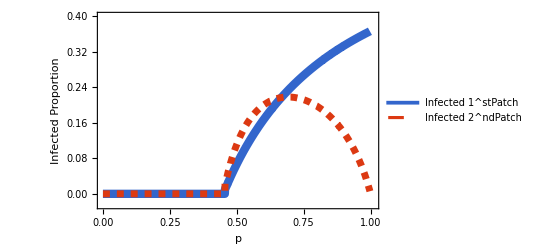

```mathematica
pp={0.5299,0.9756,0.1607,0.8359,0.2446,0.7601,0.6825,0.9512,0.1679,0.9371,0.2055,0.8874,0.6332,0.0521,0.231,0.8815,0.8797,0.3861,0.5969,0.1375,0.5913,0.1008,0.6372,0.5247,0.1581,0.1715,0.5835,0.1004,0.6322,0.5425,0.6389,0.3364,0.8929,0.185,0.4517,0.8945,0.4081,0.3252,0.7654,0.8945,0.6933,0.8455,0.8002,0.8841,0.5249,0.4764,0.5721,0.4979,0.4117,0.4054,0.0205,0.1132,0.5068,0.5845,0.5113,0.996,0.2909,0.6183,0.3488,0.2451,0.3633,0.9773,0.3149,0.1793,0.2506,0.798,0.7959,0.2429,0.7587,0.346,0.1446,0.8471,0.9951,0.5397,0.9968,0.1451,0.5047,0.1597,0.6261,0.5406,0.6436,0.449,0.6325,0.4677,0.1903,0.2399,0.6604,0.8831,0.27,0.5215,0.2873,0.6253,0.2874,0.7226,0.6128,0.4896,0.6069,0.0408,0.4915,0.3781,0.2158,0.5561,0.4032,0.3496,0.7765,0.1056,0.3124,0.3351,0.9194,0.715,0.7873,0.8154,0.5026,0.5281,0.2102,0.4675,0.3019,0.3303,0.3876,0.6202,0.037,0.3857,0.5215,0.0494,0.8404,0.9563,0.0515,0.5549,0.5274,0.7321,0.1206,0.7461,0.2242,0.3133,0.5897,0.253,0.737,0.5223,0.1212,0.8072,0.6632,0.8519,0.6027,0.3662,0.4418,0.1364,0.9234,0.5879,0.2038,0.4763,0.8944,0.9351,0.3286,0.0387,0.0965,0.5457,0.2207,0.694,0.4203,0.6391,0.1683,0.661,0.0609,0.8137,0.7849,0.0208,0.0123,0.718,0.9169,0.5184,0.0049,0.8015,0.2296,0.9848,0.58,0.844,0.5046,0.1792,0.448,0.6192,0.0402,0.9241,0.3306,0.8722,0.7235,0.5172,0.5073,0.0966,0.7016,0.1446,0.7984,0.0779,0.1435,0.3987,0.4719,0.6076,0.6174,0.8202,0.9356,0.0612,0.7022,0.1078,0.6156,0.9061,0.1784,0.4618,0.8029,0.6004,0.0006,0.8509,0.8445,0.0996,0.7448,0.7064,0.4557,0.4026,0.2881,0.3943,0.9794,0.7093,0.2142,0.8641,0.3178,0.8388,0.7815,0.9289,0.7448,0.3714,0.4302,0.1432,0.3394,0.6102,0.6347,0.311,0.7524,0.1781,0.5627,0.564,0.4565,0.0733,0.9295,0.6226,0.6738,0.1288,0.2875,0.1156,0.0838,0.8032,0.4009,0.3512,0.5244,0.9013,0.1793,0.289,0.5043,0.2521,0.024,0.4416,0.9502,0.8241,0.3849,0.2341,0.9246,0.3847,0.2865,0.5623,0.7305,0.7892,0.8491,0.8565,0.7032,0.6958,0.3495,0.237,0.4821,0.6326,0.0027,0.4302,0.7103,0.7401,0.6807,0.5011,0.7126,0.882,0.8462,0.9838,0.7137,0.361,0.0887,0.2721,0.1418,0.2407,0.1842,0.861,0.1488,0.9039,0.805,0.0909,0.2265,0.3373,0.6423,0.0743,0.3497,0.2155,0.9818,0.4872,0.2233,0.5163,0.6303,0.0772,0.475,0.1427,0.9391,0.4441,0.1976,0.5947,0.7746,0.957,0.4094,0.6863,0.0618,0.7777,0.3918,0.3612,0.3729,0.1882,0.6585,0.1217,0.0105,0.0922,0.5157,0.1823,0.7731,0.6568,0.0997,0.6899,0.4058,0.2224,0.137,0.0454,0.6258,0.379,0.3011,0.7087,0.8775,0.2881,0.2682,0.6596,0.8437,0.3384,0.0042,0.4933,0.5451,0.5192,0.0355,0.1763,0.367,0.7555,0.5441,0.4274,0.1124,0.469,0.0241,0.8498,0.3544,0.985,0.4086,0.0752,0.4685,0.8721,0.9673,0.8939,0.6458,0.8824,0.953,0.2017,0.9774,0.5097,0.1666,0.2586,0.9651,0.2199,0.1639,0.0146,0.62,0.4077,0.8188,0.6937,0.852,0.611,0.6998,0.5656,0.4373,0.4339,0.1818,0.3674,0.8965,0.5987,0.2912,0.6331,0.6311,0.4822,0.2872,0.888,0.5724,0.7475,0.8229,0.5296,0.3166,0.2299,0.7954,0.6337,0.3462,0.2265,0.7695,0.1765,0.4458,0.9382,0.0278,0.9974,0.5901,0.7214,0.414,0.5203,0.8228,0.3481,0.5433,0.4325,0.4653,0.5171,0.0436,0.3849,0.525,0.9129,0.7995,0.4947,0.7171,0.2798,0.4901,0.2756,0.9485,0.3419,0.3746,0.8796,0.2894,0.4413,0.3024,0.7335,0.1968,0.8886,0.6768,0.379,0.6324,0.1694,0.2057,0.9439,0.5208,0.5495,0.3716,0.9834,0.4839,0.1183,0.892,0.5983,0.066,0.6787,0.1023,0.587,0.792,0.5979,0.4113,0.3182,0.3129,0.1267,0.8216,0.3757,0.3631,0.0238,0.9114,0.9432,0.7211,0.8688,0.7627,0.7956,0.1425,0.7961,0.5521,0.0413,0.6894,0.0532,0.5883,0.9721,0.5326,0.1697,0.019,0.8067,0.2355,0.6761,0.7282,0.7488};

inf1={0.1005,0.3592,-0.0,0.3078,0.0,0.272,0.2271,0.3513,0.0,0.3465,-0.0,0.3286,0.1929,0.0,-0.0,0.3263,0.3256,0.0,0.1641,-0.0,0.1593,0.0,0.1959,0.0949,0.0,0.0,0.1526,-0.0,0.1921,0.1136,0.1971,0.0,0.3307,-0.0,-0.0,0.3313,0.0,-0.0,0.2747,0.3313,0.2339,0.3119,0.2917,0.3273,0.0951,0.037,0.1422,0.0641,-0.0,-0.0,0.0,-0.0,0.0747,0.1534,0.08,0.3655,-0.0,0.1815,-0.0,-0.0,-0.0,0.3597,-0.0,0.0,-0.0,0.2907,0.2897,-0.0,0.2712,0.0,-0.0,0.3125,0.3652,0.1108,0.3657,-0.0,0.0722,-0.0,0.1875,0.1117,0.2005,-0.0,0.1924,0.0252,-0.0,-0.0,0.2124,0.3269,0.0,0.0914,-0.0,0.1869,0.0,0.2515,0.1771,0.054,0.1723,0.0,0.0563,0.0,0.0,0.1272,-0.0,-0.0,0.2803,0.0,-0.0,-0.0,0.3404,0.2471,0.2856,0.2987,0.0698,0.0986,-0.0,0.0251,-0.0,-0.0,0.0,0.183,0.0,-0.0,0.0914,-0.0,0.3097,0.3529,-0.0,0.126,0.0978,0.2569,0.0,0.2646,-0.0,0.0,0.158,-0.0,0.2596,0.0923,0.0,0.295,0.2143,0.3145,0.1689,-0.0,-0.0,0.0,0.3418,0.1564,0.0,0.0368,0.3313,0.3459,0.0,0.0,-0.0,0.1169,-0.0,0.2344,-0.0,0.1973,0.0,0.2128,0.0,0.298,0.2844,-0.0,0.0,0.2488,0.3395,0.088,0.0,0.2923,-0.0,0.362,0.1494,0.3112,0.0721,-0.0,0.0,0.1822,-0.0,0.342,0.0,0.3227,0.252,0.0867,0.0753,-0.0,0.2391,-0.0,0.2909,0.0,0.0,-0.0,0.0309,0.1729,0.1807,0.3009,0.346,-0.0,0.2394,-0.0,0.1793,0.3356,0.0,0.0172,0.293,0.167,-0.0,0.3141,0.3114,-0.0,0.2639,0.2419,-0.0,-0.0,0.0,-0.0,0.3604,0.2437,0.0,0.3195,0.0,0.309,0.2828,0.3437,0.2639,-0.0,0.0,-0.0,-0.0,0.175,0.194,0.0,0.2679,-0.0,0.1335,0.1348,0.0112,-0.0,0.3439,0.1848,0.2214,0.0,0.0,0.0,-0.0,0.2932,-0.0,-0.0,0.0946,0.3338,-0.0,0.0,0.0718,0.0,0.0,0.0,0.3509,0.3026,-0.0,-0.0,0.3422,-0.0,0.0,0.1331,0.256,0.2866,0.3133,0.3164,0.24,0.2355,-0.0,-0.0,0.0444,0.1924,-0.0,0.0,0.2443,0.2613,0.2259,0.0679,0.2457,0.3265,0.3121,0.3617,0.2463,-0.0,-0.0,0.0,-0.0,0.0,-0.0,0.3182,-0.0,0.3348,0.294,0.0,-0.0,-0.0,0.1996,-0.0,0.0,0.0,0.3611,0.0509,0.0,0.0856,0.1907,0.0,0.035,-0.0,0.3472,0.0,0.0,0.1622,0.2794,0.3532,0.0,0.2295,0.0,0.2809,0.0,-0.0,-0.0,0.0,0.2111,-0.0,-0.0,-0.0,0.085,0.0,0.2786,0.2099,-0.0,0.2318,-0.0,-0.0,-0.0,0.0,0.1872,-0.0,-0.0,0.2434,0.3248,0.0,-0.0,0.2118,0.3111,0.0,-0.0,0.0585,0.1163,0.0888,0.0,-0.0,-0.0,0.2696,0.1153,-0.0,0.0,0.0271,-0.0,0.3137,-0.0,0.3621,0.0,0.0,0.0264,0.3227,0.3565,0.3311,0.2022,0.3267,0.3519,0.0,0.3597,0.0781,0.0,0.0,0.3558,0.0,-0.0,-0.0,0.1828,0.0,0.3003,0.2342,0.3145,0.1757,0.238,0.1363,-0.0,0.0,0.0,-0.0,0.332,0.1656,-0.0,0.1928,0.1913,0.0445,-0.0,0.3288,0.1425,0.2653,0.3021,0.1003,0.0,-0.0,0.2895,0.1933,-0.0,0.0,0.2768,0.0,0.0,0.3469,0.0,0.3659,0.1583,0.2508,-0.0,0.0901,0.3021,-0.0,0.1145,0.0,0.0218,0.0865,-0.0,0.0,0.0953,0.338,0.2914,0.0603,0.2483,-0.0,0.0546,0.0,0.3504,0.0,0.0,0.3256,-0.0,0.0,0.0,0.2577,-0.0,0.3291,0.2234,-0.0,0.1923,-0.0,-0.0,0.3488,0.0907,0.1207,0.0,0.3616,0.0467,0.0,0.3303,0.1653,0.0,0.2246,-0.0,0.1556,0.2879,0.1649,0.0,-0.0,-0.0,0.0,0.3015,0.0,-0.0,-0.0,0.3375,0.3486,0.2507,0.3214,0.2733,0.2896,0.0,0.2898,0.1233,0.0,0.2315,0.0,0.1567,0.3581,0.1034,0.0,-0.0,0.2948,-0.0,0.2229,0.2547,0.266};

inf2={0.1495,0.0478,-0.0,0.1811,0.0,0.2096,0.2178,0.0838,-0.0,0.1012,-0.0,0.1482,0.2109,0.0,-0.0,0.1526,0.154,0.0,0.1982,-0.0,0.1956,0.0,0.2119,0.1437,0.0,0.0,0.1915,-0.0,0.2106,0.1619,0.2123,0.0,0.1438,-0.0,-0.0,0.1425,0.0,-0.0,0.2083,0.1425,0.2179,0.1759,0.1972,0.1507,0.144,0.0681,0.1847,0.1075,-0.0,-0.0,0.0,-0.0,0.1209,0.192,0.1272,0.009,0.0,0.2066,-0.0,-0.0,-0.0,0.0449,0.0,-0.0,-0.0,0.198,0.1988,-0.0,0.21,0.0,-0.0,0.1751,0.0108,0.1594,0.0071,-0.0,0.1179,-0.0,0.209,0.1602,0.2133,-0.0,0.2107,0.0484,-0.0,-0.0,0.216,0.1515,0.0,0.1401,-0.0,0.2088,0.0,0.2162,0.2047,0.0937,0.2025,0.0,0.097,0.0,0.0,0.1735,-0.0,-0.0,0.2052,0.0,-0.0,-0.0,0.12,0.217,0.2018,0.191,0.1148,0.1475,-0.0,0.0482,-0.0,-0.0,0.0,0.2072,0.0,-0.0,0.14,-0.0,0.1787,0.0771,-0.0,0.1725,0.1467,0.215,0.0,0.2127,-0.0,0.0,0.1948,-0.0,0.2143,0.141,0.0,0.1944,0.2163,0.1723,0.2008,-0.0,-0.0,-0.0,0.116,0.1939,0.0,0.0678,0.1426,0.1034,0.0,0.0,-0.0,0.1648,-0.0,0.2179,-0.0,0.2123,0.0,0.2161,0.0,0.1917,0.2026,-0.0,0.0,0.2167,0.1225,0.1363,0.0,0.1967,-0.0,0.0314,0.1895,0.1768,0.1178,-0.0,0.0,0.2069,-0.0,0.1153,0.0,0.1592,0.2161,0.1348,0.1216,-0.0,0.2178,-0.0,0.1979,0.0,0.0,-0.0,0.0582,0.2028,0.2063,0.1888,0.1028,-0.0,0.2177,-0.0,0.2057,0.1326,0.0,0.034,0.1962,0.1998,-0.0,0.1728,0.1765,-0.0,0.2129,0.2176,-0.0,-0.0,0.0,-0.0,0.0413,0.2174,0.0,0.1647,0.0,0.1796,0.2037,0.1103,0.2129,-0.0,0.0,-0.0,-0.0,0.2037,0.2113,0.0,0.2114,-0.0,0.1784,0.1793,0.0233,-0.0,0.1096,0.208,0.2173,0.0,0.0,0.0,-0.0,0.196,-0.0,-0.0,0.1434,0.1368,-0.0,0.0,0.1174,0.0,0.0,0.0,0.0851,0.187,-0.0,-0.0,0.1148,-0.0,0.0,0.1781,0.2152,0.2012,0.1739,0.1695,0.2177,0.2179,-0.0,-0.0,0.0797,0.2108,-0.0,0.0,0.2173,0.2137,0.2177,0.1125,0.2172,0.1522,0.1755,0.0333,0.2171,-0.0,-0.0,0.0,-0.0,0.0,-0.0,0.1667,-0.0,0.1346,0.1953,0.0,-0.0,-0.0,0.213,-0.0,0.0,0.0,0.0369,0.0893,0.0,0.1337,0.2102,0.0,0.065,-0.0,0.0987,0.0,0.0,0.1972,0.2058,0.076,0.0,0.2179,0.0,0.2049,0.0,-0.0,-0.0,0.0,0.2158,-0.0,-0.0,-0.0,0.1329,0.0,0.2062,0.2155,-0.0,0.2179,-0.0,-0.0,-0.0,0.0,0.2089,-0.0,-0.0,0.2174,0.1556,0.0,-0.0,0.2159,0.1769,0.0,-0.0,0.1,0.1643,0.1372,0.0,-0.0,-0.0,0.2107,0.1634,-0.0,0.0,0.0517,-0.0,0.1735,-0.0,0.0311,0.0,0.0,0.0505,0.1593,0.061,0.143,0.2137,0.152,0.0814,0.0,0.0448,0.125,0.0,0.0,0.0644,0.0,-0.0,-0.0,0.2072,0.0,0.1894,0.2179,0.1722,0.204,0.2178,0.1804,-0.0,-0.0,-0.0,-0.0,0.1409,0.199,-0.0,0.2109,0.2104,0.0798,-0.0,0.1477,0.1849,0.2124,0.1875,0.1492,0.0,-0.0,0.199,0.211,-0.0,0.0,0.2072,0.0,0.0,0.0999,0.0,0.0058,0.195,0.2164,-0.0,0.1385,0.1876,-0.0,0.1627,0.0,0.0424,0.1346,-0.0,-0.0,0.1441,0.1263,0.1975,0.1024,0.2168,-0.0,0.0945,0.0,0.0873,0.0,0.0,0.154,-0.0,0.0,0.0,0.2148,-0.0,0.1472,0.2175,-0.0,0.2107,-0.0,-0.0,0.093,0.1392,0.1681,0.0,0.0341,0.0832,0.0,0.1445,0.1989,0.0,0.2176,-0.0,0.1934,0.2002,0.1987,0.0,-0.0,-0.0,0.0,0.1881,0.0,-0.0,-0.0,0.1278,0.0939,0.2164,0.1616,0.209,0.1989,0.0,0.1987,0.1703,0.0,0.2179,0.0,0.194,0.0535,0.1523,0.0,-0.0,0.1946,-0.0,0.2175,0.2155,0.2121};
tdbpp=TemporalData[{inf1, inf2},{{pp },{pp }}];
ppGraph= ListLinePlot[ tdbpp,
PlotStyle->{ 
Directive[Thickness[0.015],ToColor[RGBColor["#3366CC"],Hue]],
Directive[Thickness[0.0125],Dashed,ToColor[RGBColor["#DC3912"],Hue]]
},
Frame->{True,True,False,False},
FrameLabel->{Style["p", Black, 18 ], Style["Infected Proportion", Black, 18 ]},
Axes->False,
LabelStyle->Directive[Bold, Medium, Black],
PlotRange->{{0,1.01},{-0.025, 0.4}},
TicksStyle->Directive[Bold, 12],
PlotLegends->Placed[{
Style["Infected 1^stPatch",FontFamily->"Century",16],
Style["Infected 2^ndPatch",FontFamily->"Century",16]
}, Below],
ImageSize->{600},Epilog->{Inset[Show[PR02effect,ImageSize->160],{0.17,0.3},Automatic]}];
Export["C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/picno/Plots/ppGraph_v2.pdf",ppGraph,"PDF","AllowRasterization"->False];
ppGraph
```

```mathematica
(*AS10={0.65714,0.65714,0.65714,0.65714,0.65714,0.65714,0.65714,0.65714,0.56825,0.56825,0.46207,0.46207,0.37915,0.37915,0.31271,0.31271,0.25837,0.25837,0.21315,0.21315,0.175,0.175,0.14242,0.14242,0.1143,0.1143,0.08982,0.08982,0.06834,0.06834,0.04935,0.04935,0.03247,0.03247,0.01737,0.01739,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0};
I20={0.2824,0.2824,0.2824,0.2824,0.2824,0.2824,0.2824,0.2824,0.2784,0.2784,0.27263,0.27263,0.2671,0.2671,0.26177,0.26177,0.25661,0.25661,0.25161,0.25161,0.24673,0.24673,0.24195,0.24195,0.23726,0.23726,0.23263,0.23263,0.22805,0.22805,0.22349,0.22349,0.21894,0.21894,0.21437,0.21438,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833,0.20833};
I21={0.41438,0.41438,0.41438,0.41438,0.41438,0.41438,0.41438,0.41438,0.40684,0.40684,0.39571,0.39571,0.38476,0.38476,0.37392,0.37392,0.36315,0.36315,0.35239,0.35239,0.34157,0.34157,0.33062,0.33062,0.31946,0.31946,0.30799,0.30799,0.29608,0.29608,0.28356,0.28356,0.27016,0.27016,0.25555,0.2556,0.2556,0.23369,0.23369,0.23333,0.23333,0.23352,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333,0.23333};
I22={0.48966,0.48966,0.48966,0.48966,0.48966,0.48966,0.48966,0.48966,0.47925,0.47925,0.46368,0.46368,0.44811,0.44811,0.43245,0.43245,0.41663,0.41663,0.40055,0.40055,0.38407,0.38407,0.36706,0.36706,0.34931,0.34931,0.33057,0.33057,0.31044,0.31044,0.28835,0.28835,0.26326,0.26326,0.23314,0.23334,0.23334,0.17818,0.17818,0.17818,0.17818,0.17818,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175,0.175};
I23={0.53803,0.53803,0.53803,0.53803,0.53803,0.53803,0.53803,0.53803,0.52533,0.52533,0.50618,0.50618,0.48683,0.48683,0.4672,0.4672,0.44716,0.44716,0.42658,0.42658,0.40528,0.40528,0.38304,0.38304,0.35955,0.35955,0.3344,0.3344,0.30694,0.30694,0.2761,0.2761,0.23992,0.23992,0.19377,0.19371,0.16935,0.16363,0.06655,0.06655,0.08169,0.08169,0.08169,0.08169,0.08169,0.06665,0.06665,0.06665,0.06665,0.06665,0.06665,0.06665,0.06665,0.06665,0.06665,0.06662,0.06662,0.06662,0.06662,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,0.06664,0.06664,0.06664,0.06664,0.06664,0.06665,0.06665,0.06665,0.06665,0.06665,0.06665,0.06665,0.06665,0.06665,0.06665,0.06665,0.06665,0.06665,0.06665,0.06665,0.06665,0.06665,0.06665,0.06665,0.06665,0.06665,0.06665,0.06665,0.06665,0.06665,0.06665,0.06665,0.06665};
I24={0.57165,0.57165,0.57165,0.57165,0.57165,0.57165,0.57165,0.57165,0.55713,0.55713,0.5351,0.5351,0.5127,0.5127,0.48983,0.48983,0.46635,0.46635,0.44209,0.44209,0.41686,0.41686,0.39037,0.39037,0.36226,0.36226,0.332,0.332,0.29878,0.29878,0.26129,0.26129,0.21705,0.21705,0.16036,0.16047,0.01936,0.13906,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0};
I25={0.59638,0.59638,0.59638,0.59638,0.59638,0.59638,0.59638,0.59638,0.58038,0.58038,0.55602,0.55602,0.53114,0.53114,0.50564,0.50564,0.47936,0.47936,0.45213,0.45213,0.42373,0.42373,0.39387,0.39387,0.36213,0.36213,0.32795,0.32795,0.29049,0.29049,0.24837,0.24837,0.19912,0.19912,0.13756,0.13731,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0};
tdbAS1=TemporalData[{I20, I21, I22, I23, I24, I25},{{AS10},{AS10},{AS10},{AS10},{AS10},{AS10}}];
AS1Graph= ListLinePlot[ tdbAS1,
PlotStyle->{ 
Directive[Thickness[0.0075],ToColor[RGBColor["#3366CC"],Hue]],Directive[Thickness[0.0075],ToColor[RGBColor["#DC3912"],Hue]],Directive[Thickness[0.0075],ToColor[RGBColor["#FF9900"],Hue]],Directive[Thickness[0.0075],ToColor[RGBColor["#109618"],Hue]],Directive[Thickness[0.0075],ToColor[RGBColor["#990099"],Hue]],Directive[Thickness[0.0075],ToColor[RGBColor["#0099C6"],Hue]]
},
Frame->{True,True,False,False},
FrameLabel->{Style["", Black, 14 ], Style["", Black, 14 ]},
Axes->False,
LabelStyle->Directive[Bold, Medium, Black],
PlotRange->{{-0.02,0.6},{-0.02, 0.6}},
TicksStyle->Directive[Bold, 12],
PlotLegends->Placed[{
Style["",FontFamily->"Century",12],
Style["",FontFamily->"Century",12],
Style["",FontFamily->"Century",12],
Style["",FontFamily->"Century",12],
Style["",FontFamily->"Century",12],
Style["",FontFamily->"Century",12]
}, Right],
ImageSize->{600}];
Export["C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/picno/Plots/AS1Graph.pdf",AS1Graph,"PDF","AllowRasterization"->False];
AS1Graph*)
```

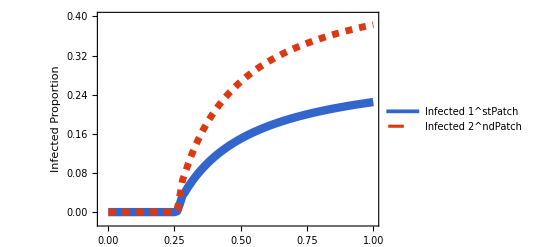

```mathematica
alphas={0.001,0.001,0.01099,0.01099,0.02098,0.02098,0.03097,0.03097,0.04096,0.04096,0.05095,0.05095,0.06094,0.06094,0.07093,0.07093,0.08092,0.08092,0.09091,0.09091,0.1009,0.1009,0.11089,0.11089,0.12088,0.12088,0.13087,0.13087,0.14086,0.14086,0.15085,0.15085,0.16084,0.16084,0.17083,0.17083,0.18082,0.18082,0.19081,0.19081,0.2008,0.2008,0.21079,0.21079,0.22078,0.22078,0.23077,0.23077,0.24076,0.24076,0.25075,0.25075,0.26074,0.26074,0.27073,0.27073,0.28072,0.28072,0.29071,0.29071,0.3007,0.3007,0.31069,0.31069,0.32068,0.32068,0.33067,0.33067,0.34066,0.34066,0.35065,0.35065,0.36064,0.36064,0.37063,0.37063,0.38062,0.38062,0.39061,0.39061,0.4006,0.4006,0.41059,0.41059,0.42058,0.42058,0.43057,0.43057,0.44056,0.44056,0.45055,0.45055,0.46054,0.46054,0.47053,0.47053,0.48052,0.48052,0.49051,0.49051,0.5005,0.5005,0.51049,0.51049,0.52048,0.52048,0.53047,0.53047,0.54046,0.54046,0.55045,0.55045,0.56044,0.56044,0.57043,0.57043,0.58042,0.58042,0.59041,0.59041,0.6004,0.6004,0.61039,0.61039,0.62038,0.62038,0.63037,0.63037,0.64036,0.64036,0.65035,0.65035,0.66034,0.66034,0.67033,0.67033,0.68032,0.68032,0.69031,0.69031,0.7003,0.7003,0.71029,0.71029,0.72028,0.72028,0.73027,0.73027,0.74026,0.74026,0.75025,0.75025,0.76024,0.76024,0.77023,0.77023,0.78022,0.78022,0.79021,0.79021,0.8002,0.8002,0.81019,0.81019,0.82018,0.82018,0.83017,0.83017,0.84016,0.84016,0.85015,0.85015,0.86014,0.86014,0.87013,0.87013,0.88012,0.88012,0.89011,0.89011,0.9001,0.9001,0.91009,0.91009,0.92008,0.92008,0.93007,0.93007,0.94006,0.94006,0.95005,0.95005,0.96004,0.96004,0.97003,0.97003,0.98002,0.98002,0.99001,0.99001,1.0,1.0};
I1s={0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.00388,0.01703,0.01701,0.03429,0.03381,0.04159,0.04153,0.05046,0.05044,0.05857,0.05858,0.06613,0.06617,0.07319,0.07319,0.07984,0.07984,0.08611,0.08611,0.09204,0.09204,0.09764,0.09764,0.10295,0.10295,0.10799,0.10799,0.11278,0.11278,0.11734,0.11734,0.12167,0.12167,0.12581,0.12581,0.12976,0.12976,0.13354,0.13354,0.13715,0.13715,0.14061,0.14061,0.14392,0.14392,0.1471,0.1471,0.15015,0.15015,0.15308,0.15308,0.1559,0.1559,0.15862,0.15862,0.16123,0.16123,0.16375,0.16375,0.16618,0.16618,0.16852,0.16852,0.17078,0.17078,0.17297,0.17297,0.17508,0.17508,0.17713,0.17713,0.17911,0.17911,0.18102,0.18102,0.18288,0.18288,0.18468,0.18468,0.18642,0.18642,0.18811,0.18811,0.18976,0.18976,0.19135,0.19135,0.1929,0.1929,0.19441,0.19441,0.19587,0.19587,0.1973,0.1973,0.19868,0.19868,0.20003,0.20003,0.20135,0.20135,0.20263,0.20263,0.20387,0.20387,0.20509,0.20509,0.20627,0.20627,0.20743,0.20743,0.20856,0.20856,0.20966,0.20966,0.21073,0.21073,0.21178,0.21178,0.2128,0.2128,0.21381,0.21381,0.21478,0.21478,0.21574,0.21574,0.21668,0.21668,0.21759,0.21759,0.21849,0.21849,0.21936,0.21936,0.22022,0.22022,0.22106,0.22106,0.22188,0.22188,0.22268,0.22268,0.22347,0.22347,0.22424,0.22424,0.225,0.225};
I2s={0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.00808,0.03367,0.03367,0.06608,0.06515,0.08002,0.08,0.09644,0.09639,0.1112,0.11122,0.1248,0.12489,0.13735,0.13735,0.14906,0.14906,0.16001,0.16001,0.17026,0.17026,0.17989,0.17989,0.18895,0.18895,0.19748,0.19748,0.20554,0.20554,0.21317,0.21317,0.22039,0.22039,0.22724,0.22724,0.23375,0.23375,0.23995,0.23995,0.24585,0.24585,0.25148,0.25148,0.25685,0.25685,0.26199,0.26199,0.26691,0.26691,0.27162,0.27162,0.27613,0.27613,0.28046,0.28046,0.28462,0.28462,0.28862,0.28862,0.29247,0.29247,0.29617,0.29617,0.29974,0.29974,0.30318,0.30318,0.3065,0.3065,0.30971,0.30971,0.3128,0.3128,0.31579,0.31579,0.31869,0.31869,0.32149,0.32149,0.3242,0.3242,0.32683,0.32683,0.32937,0.32937,0.33184,0.33184,0.33424,0.33424,0.33656,0.33656,0.33882,0.33882,0.34101,0.34101,0.34314,0.34314,0.34521,0.34521,0.34723,0.34723,0.34919,0.34919,0.3511,0.3511,0.35296,0.35296,0.35477,0.35477,0.35654,0.35654,0.35826,0.35826,0.35993,0.35993,0.36157,0.36157,0.36317,0.36317,0.36472,0.36472,0.36625,0.36625,0.36773,0.36773,0.36918,0.36918,0.3706,0.3706,0.37199,0.37199,0.37334,0.37334,0.37467,0.37467,0.37597,0.37597,0.37723,0.37723,0.37847,0.37847,0.37969,0.37969,0.38088,0.38088,0.38204,0.38204,0.38319,0.38319};

tdbalphas=TemporalData[{I1s, I2s},{{alphas},{alphas}}];
AlphasGraph= ListLinePlot[ tdbalphas,
PlotStyle->{ 
Directive[Thickness[0.015],ToColor[RGBColor["#3366CC"],Hue]],
Directive[Thickness[0.0125],Dashed,ToColor[RGBColor["#DC3912"],Hue]]
},
Frame->{True,True,False,False},
FrameLabel->{Style["", Black, 18 ], Style["Infected Proportion", Black, 18 ]},
Axes->False,
LabelStyle->Directive[Bold, Medium, Black],
PlotRange->{{-0.02,1},{-0.02, 0.4}},
TicksStyle->Directive[Bold, 12],
PlotLegends->Placed[{
Style["Infected 1^stPatch",FontFamily->"Century",16],
Style["Infected 2^ndPatch",FontFamily->"Century",16]
}, Below],
ImageSize->{600},Epilog->{Inset[Show[AlphaR02effect,ImageSize->160],{0.15,0.3},Automatic]}];Export["C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/picno/Plots/AlphasGraph_V2.pdf",AlphasGraph,"PDF","AllowRasterization"->False];
AlphasGraph
```

-Graphics-

-Graphics-

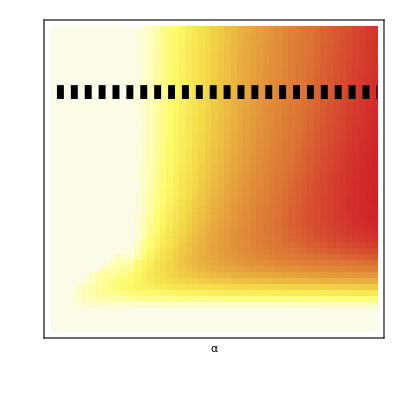

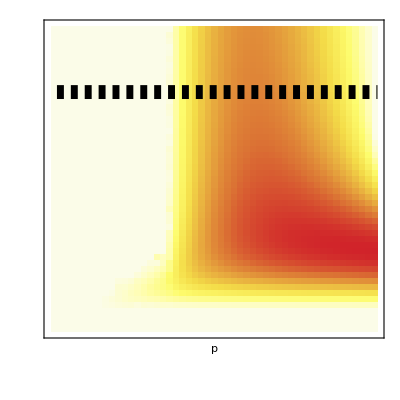

```mathematica
dataAlpha={{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0127,0.0559,0.0861,0.1124,0.1353,0.1556,0.1737,0.1899,0.2046,0.2180,0.2301,0.2413,0.2515,0.2605,0.2693,0.2775,0.2850,0.2921,0.2988,0.3050,0.3108,0.3163,0.3215,0.3264,0.3310,0.3354,0.3396,0.3436,0.3473,0.3509,0.3544,0.3577,0.3608,0.3638,0.3667,0.3694,0.3721,0.3746},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0373,0.0570,0.0863,0.1126,0.1356,0.1559,0.1740,0.1903,0.2050,0.2184,0.2305,0.2417,0.2519,0.2609,0.2697,0.2778,0.2854,0.2925,0.2991,0.3054,0.3112,0.3167,0.3219,0.3268,0.3314,0.3358,0.3400,0.3439,0.3477,0.3513,0.3547,0.3580,0.3611,0.3641,0.3670,0.3697,0.3724,0.3749},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0135,0.0557,0.0865,0.1129,0.1359,0.1563,0.1744,0.1907,0.2054,0.2188,0.2309,0.2421,0.2523,0.2613,0.2701,0.2783,0.2859,0.2929,0.2996,0.3058,0.3116,0.3171,0.3223,0.3272,0.3318,0.3362,0.3403,0.3443,0.3481,0.3516,0.3551,0.3583,0.3615,0.3644,0.3673,0.3701,0.3727,0.3752},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0156,0.0568,0.0868,0.1133,0.1363,0.1566,0.1748,0.1911,0.2059,0.2192,0.2314,0.2425,0.2528,0.2618,0.2706,0.2787,0.2863,0.2934,0.3000,0.3062,0.3120,0.3175,0.3227,0.3276,0.3322,0.3366,0.3407,0.3447,0.3484,0.3520,0.3554,0.3587,0.3618,0.3648,0.3677,0.3704,0.3730,0.3756},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0229,0.0574,0.0870,0.1136,0.1366,0.1571,0.1753,0.1916,0.2063,0.2197,0.2319,0.2430,0.2533,0.2623,0.2710,0.2792,0.2868,0.2938,0.3004,0.3066,0.3125,0.3179,0.3231,0.3280,0.3326,0.3370,0.3411,0.3451,0.3488,0.3524,0.3558,0.3591,0.3622,0.3652,0.3680,0.3708,0.3734,0.3759},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0195,0.0585,0.0874,0.1140,0.1371,0.1575,0.1757,0.1921,0.2068,0.2202,0.2324,0.2435,0.2538,0.2628,0.2715,0.2797,0.2873,0.2943,0.3009,0.3071,0.3129,0.3184,0.3236,0.3284,0.3330,0.3374,0.3416,0.3455,0.3492,0.3528,0.3562,0.3595,0.3626,0.3655,0.3684,0.3711,0.3737,0.3763},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0079,0.0564,0.0877,0.1144,0.1375,0.1580,0.1762,0.1926,0.2073,0.2207,0.2329,0.2441,0.2543,0.2633,0.2721,0.2802,0.2878,0.2948,0.3014,0.3076,0.3134,0.3189,0.3240,0.3289,0.3335,0.3379,0.3420,0.3459,0.3497,0.3532,0.3566,0.3599,0.3630,0.3659,0.3688,0.3715,0.3741,0.3766},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0227,0.0571,0.0881,0.1148,0.1380,0.1585,0.1768,0.1931,0.2079,0.2213,0.2335,0.2446,0.2549,0.2639,0.2726,0.2808,0.2883,0.2954,0.3020,0.3081,0.3139,0.3194,0.3245,0.3294,0.3340,0.3383,0.3425,0.3464,0.3501,0.3537,0.3571,0.3603,0.3634,0.3664,0.3692,0.3719,0.3745,0.3770},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0077,0.0589,0.0885,0.1152,0.1385,0.1591,0.1773,0.1937,0.2085,0.2219,0.2341,0.2453,0.2555,0.2645,0.2732,0.2814,0.2889,0.2960,0.3025,0.3087,0.3145,0.3199,0.3251,0.3299,0.3345,0.3388,0.3430,0.3469,0.3506,0.3541,0.3575,0.3608,0.3638,0.3668,0.3696,0.3723,0.3749,0.3774},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0218,0.0571,0.0891,0.1157,0.1390,0.1596,0.1780,0.1944,0.2092,0.2226,0.2348,0.2459,0.2562,0.2651,0.2739,0.2820,0.2895,0.2966,0.3031,0.3093,0.3151,0.3205,0.3256,0.3305,0.3350,0.3394,0.3435,0.3474,0.3511,0.3546,0.3580,0.3612,0.3643,0.3672,0.3701,0.3727,0.3753,0.3778},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0204,0.0598,0.0894,0.1163,0.1396,0.1603,0.1786,0.1951,0.2099,0.2233,0.2355,0.2466,0.2569,0.2658,0.2746,0.2827,0.2902,0.2972,0.3038,0.3099,0.3157,0.3211,0.3262,0.3311,0.3356,0.3399,0.3440,0.3479,0.3516,0.3551,0.3585,0.3617,0.3648,0.3677,0.3705,0.3732,0.3758,0.3783},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0199,0.0582,0.0898,0.1168,0.1403,0.1610,0.1794,0.1958,0.2106,0.2240,0.2362,0.2474,0.2576,0.2666,0.2753,0.2834,0.2909,0.2979,0.3045,0.3106,0.3163,0.3218,0.3269,0.3317,0.3362,0.3405,0.3446,0.3485,0.3522,0.3557,0.3590,0.3622,0.3653,0.3682,0.3710,0.3737,0.3762,0.3787},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0233,0.0603,0.0904,0.1175,0.1410,0.1617,0.1801,0.1966,0.2114,0.2248,0.2370,0.2482,0.2584,0.2673,0.2761,0.2841,0.2917,0.2986,0.3052,0.3113,0.3170,0.3224,0.3275,0.3323,0.3368,0.3411,0.3452,0.3491,0.3527,0.3562,0.3596,0.3628,0.3658,0.3687,0.3715,0.3741,0.3767,0.3792},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0250,0.0592,0.0909,0.1182,0.1418,0.1625,0.1810,0.1975,0.2123,0.2257,0.2379,0.2490,0.2592,0.2682,0.2769,0.2850,0.2924,0.2994,0.3059,0.3120,0.3178,0.3231,0.3282,0.3330,0.3375,0.3418,0.3458,0.3497,0.3533,0.3568,0.3601,0.3633,0.3663,0.3692,0.3720,0.3746,0.3772,0.3796},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0230,0.0595,0.0915,0.1189,0.1426,0.1634,0.1819,0.1984,0.2132,0.2267,0.2388,0.2500,0.2602,0.2691,0.2778,0.2858,0.2933,0.3003,0.3068,0.3128,0.3185,0.3239,0.3289,0.3337,0.3382,0.3425,0.3465,0.3503,0.3540,0.3574,0.3607,0.3639,0.3669,0.3698,0.3725,0.3752,0.3777,0.3801},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0299,0.0610,0.0922,0.1197,0.1435,0.1644,0.1829,0.1994,0.2142,0.2277,0.2398,0.2509,0.2611,0.2700,0.2787,0.2867,0.2942,0.3011,0.3076,0.3137,0.3193,0.3247,0.3297,0.3344,0.3389,0.3432,0.3472,0.3510,0.3546,0.3581,0.3613,0.3645,0.3675,0.3703,0.3731,0.3757,0.3782,0.3806},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0175,0.0613,0.0930,0.1206,0.1445,0.1654,0.1840,0.2005,0.2153,0.2287,0.2409,0.2520,0.2622,0.2711,0.2797,0.2877,0.2951,0.3021,0.3085,0.3145,0.3202,0.3255,0.3305,0.3352,0.3397,0.3439,0.3479,0.3517,0.3553,0.3587,0.3620,0.3651,0.3681,0.3709,0.3736,0.3762,0.3787,0.3811},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0135,0.0608,0.0938,0.1216,0.1455,0.1665,0.1851,0.2017,0.2165,0.2299,0.2421,0.2531,0.2633,0.2722,0.2808,0.2888,0.2962,0.3030,0.3095,0.3155,0.3211,0.3264,0.3314,0.3361,0.3405,0.3447,0.3486,0.3524,0.3560,0.3594,0.3626,0.3657,0.3687,0.3715,0.3742,0.3768,0.3793,0.3816},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0141,0.0615,0.0948,0.1227,0.1467,0.1678,0.1864,0.2029,0.2178,0.2312,0.2433,0.2544,0.2645,0.2733,0.2819,0.2899,0.2972,0.3041,0.3105,0.3165,0.3221,0.3273,0.3323,0.3369,0.3413,0.3455,0.3494,0.3532,0.3567,0.3601,0.3633,0.3664,0.3693,0.3721,0.3748,0.3773,0.3798,0.3821},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0326,0.0626,0.0958,0.1239,0.1480,0.1691,0.1878,0.2043,0.2192,0.2326,0.2447,0.2557,0.2658,0.2746,0.2831,0.2910,0.2984,0.3052,0.3116,0.3175,0.3231,0.3283,0.3332,0.3378,0.3422,0.3463,0.3502,0.3539,0.3575,0.3608,0.3640,0.3670,0.3699,0.3727,0.3754,0.3779,0.3803,0.3827},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0116,0.0648,0.0970,0.1252,0.1494,0.1706,0.1893,0.2059,0.2207,0.2340,0.2461,0.2571,0.2671,0.2759,0.2844,0.2923,0.2996,0.3064,0.3127,0.3186,0.3241,0.3293,0.3342,0.3388,0.3431,0.3472,0.3511,0.3547,0.3582,0.3615,0.3647,0.3677,0.3706,0.3733,0.3760,0.3785,0.3809,0.3832},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0208,0.0650,0.0982,0.1267,0.1510,0.1723,0.1909,0.2075,0.2223,0.2356,0.2477,0.2586,0.2686,0.2774,0.2858,0.2936,0.3009,0.3076,0.3139,0.3197,0.3252,0.3304,0.3352,0.3397,0.3440,0.3481,0.3519,0.3556,0.3590,0.3623,0.3654,0.3684,0.3712,0.3740,0.3765,0.3790,0.3814,0.3837},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0243,0.0655,0.0996,0.1283,0.1528,0.1740,0.1927,0.2093,0.2241,0.2374,0.2494,0.2603,0.2702,0.2789,0.2873,0.2951,0.3022,0.3089,0.3151,0.3209,0.3264,0.3315,0.3362,0.3407,0.3450,0.3490,0.3528,0.3564,0.3598,0.3630,0.3661,0.3691,0.3719,0.3746,0.3771,0.3796,0.3819,0.3842},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0184,0.0683,0.1012,0.1301,0.1547,0.1760,0.1947,0.2113,0.2260,0.2393,0.2512,0.2620,0.2719,0.2805,0.2889,0.2966,0.3037,0.3103,0.3165,0.3222,0.3276,0.3326,0.3373,0.3418,0.3460,0.3499,0.3537,0.3572,0.3606,0.3638,0.3668,0.3698,0.3725,0.3752,0.3777,0.3801,0.3824,0.3846},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0418,0.0691,0.1031,0.1322,0.1569,0.1782,0.1969,0.2134,0.2281,0.2413,0.2532,0.2639,0.2737,0.2823,0.2905,0.2982,0.3052,0.3117,0.3178,0.3235,0.3288,0.3338,0.3384,0.3428,0.3470,0.3509,0.3546,0.3581,0.3614,0.3645,0.3675,0.3704,0.3731,0.3757,0.3782,0.3806,0.3829,0.3851},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0274,0.0700,0.1052,0.1345,0.1593,0.1807,0.1993,0.2158,0.2304,0.2435,0.2553,0.2660,0.2757,0.2841,0.2923,0.2998,0.3068,0.3132,0.3193,0.3248,0.3301,0.3350,0.3396,0.3439,0.3480,0.3518,0.3555,0.3589,0.3622,0.3653,0.3682,0.3710,0.3737,0.3763,0.3787,0.3810,0.3833,0.3854},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0070,0.0734,0.1076,0.1371,0.1620,0.1834,0.2020,0.2184,0.2329,0.2459,0.2576,0.2681,0.2777,0.2861,0.2942,0.3016,0.3085,0.3148,0.3207,0.3262,0.3314,0.3362,0.3407,0.3450,0.3490,0.3527,0.3563,0.3597,0.3629,0.3659,0.3688,0.3716,0.3742,0.3767,0.3791,0.3814,0.3836,0.3857},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0077,0.0154,0.0741,0.1103,0.1400,0.1650,0.1864,0.2049,0.2212,0.2356,0.2485,0.2600,0.2704,0.2799,0.2881,0.2961,0.3034,0.3102,0.3164,0.3222,0.3276,0.3327,0.3374,0.3418,0.3460,0.3499,0.3536,0.3571,0.3604,0.3636,0.3665,0.3694,0.3721,0.3746,0.3771,0.3794,0.3816,0.3838,0.3858},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0339,0.0782,0.1133,0.1434,0.1684,0.1897,0.2081,0.2243,0.2386,0.2512,0.2626,0.2729,0.2822,0.2903,0.2981,0.3053,0.3119,0.3181,0.3238,0.3290,0.3340,0.3386,0.3429,0.3470,0.3508,0.3544,0.3579,0.3611,0.3641,0.3670,0.3698,0.3724,0.3749,0.3773,0.3796,0.3818,0.3839,0.3858},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0248,0.0800,0.1172,0.1472,0.1722,0.1934,0.2117,0.2277,0.2417,0.2542,0.2654,0.2755,0.2847,0.2926,0.3002,0.3072,0.3137,0.3197,0.3253,0.3304,0.3352,0.3397,0.3440,0.3479,0.3516,0.3552,0.3585,0.3616,0.3646,0.3674,0.3701,0.3726,0.3751,0.3774,0.3796,0.3817,0.3837,0.3857},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0156,0.0851,0.1214,0.1516,0.1765,0.1975,0.2156,0.2313,0.2452,0.2574,0.2684,0.2782,0.2872,0.2949,0.3024,0.3092,0.3155,0.3213,0.3267,0.3317,0.3364,0.3408,0.3449,0.3487,0.3523,0.3557,0.3589,0.3620,0.3649,0.3676,0.3702,0.3726,0.3750,0.3772,0.3794,0.3814,0.3834,0.3852},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0443,0.0893,0.1264,0.1566,0.1813,0.2021,0.2199,0.2353,0.2488,0.2608,0.2715,0.2811,0.2897,0.2972,0.3045,0.3111,0.3172,0.3228,0.3280,0.3329,0.3374,0.3416,0.3456,0.3493,0.3528,0.3561,0.3592,0.3621,0.3649,0.3675,0.3700,0.3724,0.3746,0.3768,0.3788,0.3808,0.3827,0.3845},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0378,0.0943,0.1320,0.1623,0.1867,0.2071,0.2245,0.2395,0.2527,0.2643,0.2746,0.2839,0.2923,0.2995,0.3065,0.3129,0.3188,0.3242,0.3292,0.3339,0.3382,0.3422,0.3460,0.3496,0.3529,0.3561,0.3591,0.3619,0.3645,0.3670,0.3694,0.3717,0.3739,0.3759,0.3779,0.3798,0.3816,0.3833},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0393,0.1018,0.1390,0.1689,0.1928,0.2126,0.2295,0.2440,0.2567,0.2679,0.2778,0.2867,0.2948,0.3017,0.3084,0.3145,0.3201,0.3253,0.3301,0.3345,0.3386,0.3425,0.3461,0.3495,0.3527,0.3557,0.3585,0.3612,0.3637,0.3661,0.3684,0.3705,0.3726,0.3746,0.3764,0.3782,0.3799,0.3816},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0284,0.1106,0.1471,0.1763,0.1994,0.2186,0.2348,0.2487,0.2608,0.2714,0.2809,0.2894,0.2970,0.3036,0.3099,0.3157,0.3210,0.3259,0.3305,0.3347,0.3386,0.3423,0.3457,0.3489,0.3519,0.3547,0.3574,0.3599,0.3623,0.3646,0.3667,0.3687,0.3707,0.3725,0.3743,0.3760,0.3776,0.3791},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0251,0.1193,0.1564,0.1845,0.2066,0.2248,0.2402,0.2533,0.2647,0.2748,0.2837,0.2917,0.2989,0.3051,0.3110,0.3164,0.3214,0.3260,0.3303,0.3342,0.3379,0.3413,0.3445,0.3475,0.3503,0.3530,0.3555,0.3578,0.3601,0.3622,0.3642,0.3661,0.3679,0.3696,0.3713,0.3728,0.3743,0.3758},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0905,0.1333,0.1669,0.1934,0.2141,0.2311,0.2455,0.2577,0.2684,0.2777,0.2860,0.2934,0.3000,0.3058,0.3113,0.3163,0.3210,0.3252,0.3292,0.3328,0.3362,0.3394,0.3423,0.3451,0.3477,0.3502,0.3525,0.3547,0.3567,0.3587,0.3605,0.3623,0.3640,0.3656,0.3671,0.3685,0.3699,0.3713},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0188,0.0200,0.0871,0.1445,0.1784,0.2026,0.2216,0.2372,0.2503,0.2615,0.2713,0.2798,0.2874,0.2941,0.3002,0.3055,0.3105,0.3151,0.3193,0.3232,0.3268,0.3301,0.3332,0.3361,0.3388,0.3414,0.3437,0.3460,0.3481,0.3501,0.3519,0.3537,0.3554,0.3570,0.3586,0.3600,0.3614,0.3627,0.3640,0.3652},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0079,0.0808,0.0675,0.0664,0.1156,0.1623,0.1901,0.2117,0.2286,0.2425,0.2542,0.2642,0.2729,0.2806,0.2873,0.2934,0.2989,0.3036,0.3081,0.3122,0.3160,0.3195,0.3227,0.3257,0.3285,0.3311,0.3335,0.3358,0.3379,0.3399,0.3418,0.3436,0.3453,0.3469,0.3484,0.3498,0.3512,0.3525,0.3538,0.3550,0.3561,0.3572},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0790,0.1010,0.1076,0.1142,0.1672,0.1768,0.2011,0.2195,0.2341,0.2461,0.2563,0.2650,0.2726,0.2793,0.2852,0.2905,0.2953,0.2994,0.3034,0.3070,0.3103,0.3134,0.3162,0.3188,0.3213,0.3236,0.3257,0.3277,0.3296,0.3313,0.3330,0.3346,0.3361,0.3375,0.3388,0.3401,0.3413,0.3424,0.3435,0.3446,0.3456,0.3466},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0075,0.0262,0.1095,0.1084,0.1202,0.1331,0.1340,0.1734,0.1912,0.2098,0.2248,0.2369,0.2470,0.2556,0.2629,0.2694,0.2750,0.2801,0.2846,0.2886,0.2922,0.2955,0.2986,0.3015,0.3041,0.3065,0.3088,0.3108,0.3128,0.3146,0.3163,0.3179,0.3195,0.3209,0.3222,0.3235,0.3247,0.3259,0.3270,0.3280,0.3290,0.3299,0.3308,0.3317,0.3325},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0751,0.1030,0.1239,0.1157,0.1371,0.1472,0.1590,0.1838,0.1990,0.2140,0.2259,0.2356,0.2437,0.2506,0.2566,0.2618,0.2665,0.2706,0.2743,0.2776,0.2805,0.2833,0.2859,0.2882,0.2904,0.2924,0.2942,0.2960,0.2976,0.2991,0.3005,0.3019,0.3031,0.3043,0.3054,0.3065,0.3075,0.3085,0.3094,0.3102,0.3111,0.3118,0.3126,0.3133,0.3140},{0.0000,0.0000,0.0000,0.0000,0.0135,0.0521,0.0780,0.1155,0.1269,0.1413,0.1560,0.1644,0.1730,0.1887,0.2007,0.2118,0.2207,0.2280,0.2342,0.2395,0.2442,0.2482,0.2518,0.2551,0.2580,0.2606,0.2629,0.2651,0.2671,0.2690,0.2707,0.2723,0.2737,0.2751,0.2764,0.2776,0.2787,0.2798,0.2808,0.2817,0.2826,0.2835,0.2843,0.2851,0.2858,0.2865,0.2871,0.2878,0.2884,0.2889,0.2895},{0.0000,0.0000,0.0000,0.0035,0.0674,0.0835,0.1104,0.1239,0.1384,0.1500,0.1600,0.1677,0.1741,0.1864,0.1926,0.2001,0.2063,0.2115,0.2160,0.2198,0.2232,0.2262,0.2288,0.2312,0.2333,0.2353,0.2370,0.2386,0.2401,0.2415,0.2427,0.2439,0.2450,0.2461,0.2470,0.2479,0.2488,0.2496,0.2503,0.2510,0.2517,0.2523,0.2529,0.2535,0.2541,0.2546,0.2551,0.2556,0.2560,0.2564,0.2569},{0.0000,0.0000,0.0000,0.0348,0.0691,0.0942,0.1087,0.1222,0.1361,0.1438,0.1500,0.1517,0.1592,0.1644,0.1706,0.1753,0.1793,0.1827,0.1856,0.1881,0.1903,0.1923,0.1941,0.1957,0.1971,0.1984,0.1995,0.2007,0.2017,0.2026,0.2035,0.2043,0.2050,0.2057,0.2064,0.2070,0.2076,0.2081,0.2086,0.2091,0.2096,0.2100,0.2104,0.2108,0.2112,0.2116,0.2119,0.2122,0.2126,0.2129,0.2131},{0.0000,0.0000,0.0035,0.0348,0.0554,0.0881,0.0892,0.1057,0.1112,0.1155,0.1130,0.1217,0.1241,0.1272,0.1300,0.1326,0.1347,0.1366,0.1382,0.1396,0.1408,0.1419,0.1429,0.1438,0.1446,0.1454,0.1460,0.1466,0.1472,0.1478,0.1483,0.1487,0.1492,0.1496,0.1499,0.1503,0.1506,0.1510,0.1513,0.1515,0.1518,0.1521,0.1523,0.1525,0.1527,0.1530,0.1532,0.1533,0.1535,0.1537,0.1539},{0.0000,0.0000,0.0052,0.0174,0.0394,0.0491,0.0527,0.0553,0.0572,0.0529,0.0420,0.0610,0.0555,0.0629,0.0638,0.0646,0.0654,0.0660,0.0666,0.0670,0.0675,0.0679,0.0682,0.0685,0.0688,0.0691,0.0693,0.0695,0.0698,0.0700,0.0701,0.0703,0.0705,0.0706,0.0707,0.0709,0.0710,0.0711,0.0712,0.0713,0.0714,0.0715,0.0716,0.0717,0.0718,0.0718,0.0719,0.0720,0.0720,0.0721,0.0722},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000}};

dataP = {{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0069,0.1144,0.1688,0.2088,0.2387,0.2616,0.2792,0.2927,0.3026,0.3103,0.3159,0.3195,0.3215,0.3220,0.3211,0.3190,0.3157,0.3112,0.3055,0.2986,0.2905,0.2811,0.2704,0.2581,0.2441,0.2281,0.2099,0.1889,0.1645,0.1358,0.1012,0.0578,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0437,0.1147,0.1691,0.2091,0.2391,0.2620,0.2796,0.2931,0.3030,0.3108,0.3163,0.3200,0.3221,0.3226,0.3218,0.3197,0.3165,0.3120,0.3064,0.2997,0.2917,0.2824,0.2717,0.2595,0.2456,0.2298,0.2117,0.1908,0.1665,0.1378,0.1030,0.0592,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0312,0.1148,0.1695,0.2095,0.2395,0.2624,0.2800,0.2935,0.3034,0.3112,0.3168,0.3206,0.3226,0.3232,0.3225,0.3205,0.3173,0.3130,0.3074,0.3008,0.2929,0.2837,0.2731,0.2611,0.2473,0.2316,0.2136,0.1928,0.1686,0.1399,0.1049,0.0606,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0094,0.1154,0.1699,0.2100,0.2399,0.2628,0.2804,0.2940,0.3039,0.3117,0.3173,0.3211,0.3232,0.3239,0.3232,0.3213,0.3182,0.3139,0.3085,0.3019,0.2941,0.2851,0.2747,0.2627,0.2491,0.2335,0.2156,0.1950,0.1708,0.1421,0.1070,0.0623,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0168,0.1155,0.1704,0.2104,0.2404,0.2633,0.2809,0.2944,0.3043,0.3122,0.3179,0.3217,0.3239,0.3246,0.3240,0.3222,0.3191,0.3150,0.3096,0.3032,0.2955,0.2866,0.2763,0.2644,0.2509,0.2355,0.2178,0.1972,0.1732,0.1445,0.1093,0.0640,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0324,0.1161,0.1709,0.2109,0.2409,0.2637,0.2813,0.2949,0.3048,0.3127,0.3185,0.3223,0.3246,0.3254,0.3248,0.3230,0.3201,0.3160,0.3108,0.3045,0.2969,0.2881,0.2779,0.2663,0.2529,0.2376,0.2201,0.1997,0.1757,0.1471,0.1118,0.0660,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0190,0.1169,0.1714,0.2114,0.2414,0.2642,0.2818,0.2954,0.3054,0.3133,0.3191,0.3230,0.3253,0.3261,0.3257,0.3240,0.3211,0.3172,0.3121,0.3058,0.2984,0.2897,0.2797,0.2682,0.2550,0.2399,0.2225,0.2023,0.1785,0.1499,0.1146,0.0682,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0258,0.1171,0.1719,0.2119,0.2419,0.2648,0.2824,0.2960,0.3059,0.3139,0.3197,0.3237,0.3260,0.3270,0.3266,0.3250,0.3222,0.3184,0.3134,0.3073,0.3000,0.2914,0.2816,0.2703,0.2572,0.2423,0.2251,0.2050,0.1814,0.1530,0.1175,0.0707,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0356,0.1178,0.1725,0.2125,0.2425,0.2653,0.2829,0.2966,0.3066,0.3146,0.3204,0.3244,0.3268,0.3278,0.3275,0.3260,0.3234,0.3196,0.3148,0.3088,0.3016,0.2933,0.2836,0.2724,0.2596,0.2449,0.2279,0.2080,0.1846,0.1563,0.1208,0.0735,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0419,0.1180,0.1731,0.2131,0.2431,0.2659,0.2835,0.2972,0.3072,0.3152,0.3211,0.3252,0.3277,0.3287,0.3285,0.3271,0.3246,0.3210,0.3162,0.3104,0.3034,0.2952,0.2857,0.2747,0.2621,0.2476,0.2308,0.2112,0.1880,0.1598,0.1244,0.0766,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0069,0.1183,0.1737,0.2138,0.2437,0.2666,0.2842,0.2978,0.3079,0.3159,0.3219,0.3260,0.3286,0.3297,0.3296,0.3283,0.3259,0.3224,0.3178,0.3121,0.3052,0.2972,0.2879,0.2771,0.2648,0.2505,0.2339,0.2146,0.1916,0.1637,0.1283,0.0801,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0184,0.1191,0.1744,0.2145,0.2444,0.2672,0.2849,0.2985,0.3086,0.3167,0.3227,0.3269,0.3295,0.3307,0.3307,0.3295,0.3272,0.3238,0.3194,0.3139,0.3072,0.2994,0.2903,0.2797,0.2676,0.2536,0.2373,0.2183,0.1956,0.1679,0.1327,0.0841,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0234,0.1199,0.1752,0.2152,0.2452,0.2680,0.2856,0.2993,0.3093,0.3175,0.3235,0.3278,0.3305,0.3318,0.3319,0.3308,0.3286,0.3254,0.3211,0.3157,0.3093,0.3016,0.2927,0.2825,0.2706,0.2568,0.2409,0.2222,0.1998,0.1725,0.1375,0.0887,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0395,0.1207,0.1760,0.2160,0.2459,0.2687,0.2864,0.3000,0.3101,0.3183,0.3244,0.3287,0.3315,0.3330,0.3331,0.3322,0.3301,0.3270,0.3229,0.3177,0.3115,0.3040,0.2954,0.2854,0.2738,0.2603,0.2447,0.2264,0.2044,0.1775,0.1429,0.0940,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0307,0.1217,0.1768,0.2169,0.2468,0.2696,0.2872,0.3009,0.3110,0.3192,0.3254,0.3298,0.3326,0.3342,0.3345,0.3336,0.3317,0.3288,0.3248,0.3198,0.3138,0.3066,0.2982,0.2884,0.2771,0.2641,0.2488,0.2309,0.2094,0.1830,0.1488,0.1000,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0175,0.1225,0.1778,0.2178,0.2477,0.2704,0.2880,0.3017,0.3119,0.3202,0.3264,0.3308,0.3338,0.3354,0.3358,0.3351,0.3334,0.3306,0.3268,0.3221,0.3162,0.3093,0.3012,0.2917,0.2807,0.2680,0.2532,0.2357,0.2148,0.1889,0.1553,0.1070,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0182,0.1233,0.1788,0.2188,0.2486,0.2714,0.2890,0.3027,0.3128,0.3212,0.3274,0.3320,0.3350,0.3368,0.3373,0.3367,0.3351,0.3326,0.3290,0.3244,0.3188,0.3121,0.3043,0.2952,0.2846,0.2723,0.2579,0.2409,0.2206,0.1954,0.1626,0.1150,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0024,0.1244,0.1798,0.2199,0.2497,0.2724,0.2899,0.3037,0.3139,0.3222,0.3285,0.3332,0.3363,0.3382,0.3388,0.3384,0.3370,0.3346,0.3312,0.3269,0.3215,0.3152,0.3076,0.2988,0.2886,0.2768,0.2629,0.2465,0.2268,0.2024,0.1706,0.1242,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0281,0.1254,0.1810,0.2210,0.2508,0.2734,0.2910,0.3047,0.3149,0.3233,0.3297,0.3344,0.3377,0.3396,0.3405,0.3402,0.3389,0.3367,0.3336,0.3295,0.3244,0.3183,0.3111,0.3027,0.2930,0.2816,0.2683,0.2525,0.2336,0.2101,0.1795,0.1347,0.0072},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0159,0.1266,0.1823,0.2223,0.2519,0.2746,0.2921,0.3058,0.3161,0.3245,0.3310,0.3358,0.3391,0.3412,0.3422,0.3421,0.3410,0.3390,0.3361,0.3322,0.3275,0.3217,0.3149,0.3069,0.2975,0.2867,0.2739,0.2589,0.2408,0.2184,0.1892,0.1465,0.0359},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0457,0.1278,0.1836,0.2236,0.2532,0.2758,0.2933,0.3070,0.3173,0.3257,0.3323,0.3371,0.3406,0.3428,0.3439,0.3440,0.3432,0.3414,0.3387,0.3351,0.3307,0.3252,0.3188,0.3112,0.3024,0.2921,0.2800,0.2657,0.2486,0.2273,0.1997,0.1598,0.0667},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0352,0.1291,0.1851,0.2250,0.2545,0.2771,0.2945,0.3082,0.3185,0.3270,0.3336,0.3386,0.3422,0.3445,0.3458,0.3461,0.3454,0.3439,0.3415,0.3382,0.3340,0.3290,0.3229,0.3158,0.3075,0.2978,0.2864,0.2730,0.2569,0.2369,0.2112,0.1744,0.0976},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0373,0.1308,0.1868,0.2266,0.2560,0.2784,0.2959,0.3095,0.3198,0.3284,0.3351,0.3401,0.3438,0.3463,0.3477,0.3482,0.3478,0.3465,0.3443,0.3414,0.3376,0.3329,0.3273,0.3206,0.3129,0.3038,0.2932,0.2807,0.2657,0.2472,0.2235,0.1902,0.1274},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0426,0.1325,0.1885,0.2282,0.2575,0.2799,0.2973,0.3109,0.3212,0.3298,0.3366,0.3417,0.3455,0.3482,0.3498,0.3504,0.3502,0.3492,0.3473,0.3447,0.3412,0.3370,0.3318,0.3257,0.3185,0.3102,0.3003,0.2888,0.2750,0.2580,0.2365,0.2069,0.1560},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0262,0.1345,0.1905,0.2300,0.2592,0.2814,0.2987,0.3124,0.3227,0.3313,0.3381,0.3434,0.3473,0.3501,0.3519,0.3527,0.3528,0.3520,0.3504,0.3481,0.3451,0.3412,0.3365,0.3310,0.3244,0.3168,0.3078,0.2973,0.2847,0.2694,0.2502,0.2244,0.1834},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0214,0.1368,0.1926,0.2320,0.2610,0.2831,0.3003,0.3139,0.3242,0.3328,0.3397,0.3450,0.3491,0.3521,0.3540,0.3551,0.3554,0.3549,0.3536,0.3517,0.3490,0.3456,0.3414,0.3365,0.3306,0.3237,0.3156,0.3061,0.2948,0.2813,0.2644,0.2422,0.2095},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0353,0.1392,0.1949,0.2341,0.2629,0.2848,0.3019,0.3154,0.3257,0.3344,0.3413,0.3468,0.3510,0.3541,0.3562,0.3575,0.3580,0.3578,0.3569,0.3553,0.3531,0.3501,0.3465,0.3421,0.3369,0.3307,0.3236,0.3152,0.3053,0.2934,0.2788,0.2602,0.2343},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0473,0.1415,0.1974,0.2363,0.2649,0.2866,0.3036,0.3170,0.3273,0.3360,0.3430,0.3485,0.3528,0.3561,0.3584,0.3600,0.3608,0.3608,0.3603,0.3590,0.3572,0.3547,0.3516,0.3478,0.3433,0.3380,0.3317,0.3244,0.3159,0.3057,0.2934,0.2780,0.2576},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0547,0.1446,0.2002,0.2387,0.2670,0.2885,0.3053,0.3187,0.3289,0.3376,0.3446,0.3502,0.3547,0.3581,0.3606,0.3624,0.3634,0.3638,0.3636,0.3628,0.3614,0.3594,0.3568,0.3536,0.3498,0.3453,0.3400,0.3338,0.3265,0.3180,0.3078,0.2953,0.2795},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0624,0.1478,0.2032,0.2413,0.2692,0.2905,0.3071,0.3203,0.3305,0.3392,0.3462,0.3519,0.3565,0.3600,0.3628,0.3648,0.3661,0.3668,0.3669,0.3664,0.3655,0.3640,0.3619,0.3594,0.3562,0.3525,0.3481,0.3430,0.3370,0.3300,0.3218,0.3119,0.2998},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0903,0.1517,0.2065,0.2441,0.2715,0.2925,0.3088,0.3219,0.3320,0.3406,0.3477,0.3535,0.3581,0.3619,0.3648,0.3670,0.3686,0.3696,0.3700,0.3699,0.3694,0.3684,0.3669,0.3650,0.3625,0.3596,0.3561,0.3520,0.3472,0.3417,0.3352,0.3276,0.3185},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0450,0.1558,0.2101,0.2470,0.2739,0.2944,0.3105,0.3234,0.3334,0.3420,0.3491,0.3549,0.3596,0.3635,0.3666,0.3690,0.3708,0.3721,0.3729,0.3732,0.3731,0.3726,0.3716,0.3703,0.3685,0.3663,0.3636,0.3605,0.3568,0.3526,0.3477,0.3420,0.3353},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0450,0.1609,0.2140,0.2500,0.2763,0.2964,0.3121,0.3248,0.3346,0.3431,0.3501,0.3560,0.3608,0.3648,0.3681,0.3707,0.3728,0.3743,0.3754,0.3761,0.3764,0.3763,0.3759,0.3751,0.3739,0.3724,0.3706,0.3683,0.3657,0.3626,0.3590,0.3549,0.3502},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0244,0.1664,0.2181,0.2531,0.2787,0.2981,0.3135,0.3258,0.3355,0.3439,0.3509,0.3567,0.3616,0.3657,0.3691,0.3719,0.3742,0.3760,0.3774,0.3784,0.3791,0.3794,0.3794,0.3792,0.3786,0.3777,0.3766,0.3751,0.3734,0.3713,0.3689,0.3661,0.3629},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0873,0.1719,0.2224,0.2562,0.2808,0.2996,0.3145,0.3265,0.3359,0.3441,0.3510,0.3568,0.3618,0.3659,0.3694,0.3724,0.3749,0.3769,0.3786,0.3799,0.3809,0.3817,0.3821,0.3823,0.3822,0.3820,0.3814,0.3807,0.3797,0.3785,0.3770,0.3753,0.3733},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0910,0.1786,0.2269,0.2592,0.2827,0.3007,0.3150,0.3265,0.3356,0.3437,0.3504,0.3562,0.3611,0.3653,0.3689,0.3720,0.3746,0.3768,0.3788,0.3803,0.3817,0.3827,0.3835,0.3841,0.3845,0.3847,0.3848,0.3846,0.3842,0.3837,0.3831,0.3822,0.3812},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.1046,0.1857,0.2312,0.2617,0.2840,0.3011,0.3147,0.3257,0.3345,0.3422,0.3488,0.3544,0.3593,0.3634,0.3671,0.3702,0.3730,0.3754,0.3775,0.3793,0.3809,0.3822,0.3833,0.3843,0.3850,0.3857,0.3861,0.3864,0.3866,0.3867,0.3866,0.3864,0.3861},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.1095,0.1930,0.2352,0.2636,0.2844,0.3004,0.3132,0.3237,0.3320,0.3394,0.3457,0.3512,0.3559,0.3600,0.3637,0.3668,0.3697,0.3722,0.3744,0.3764,0.3781,0.3797,0.3810,0.3822,0.3833,0.3842,0.3850,0.3857,0.3863,0.3868,0.3871,0.3874,0.3876},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.1067,0.0833,0.1128,0.1997,0.2383,0.2643,0.2834,0.2983,0.3102,0.3199,0.3277,0.3347,0.3407,0.3459,0.3505,0.3545,0.3580,0.3612,0.3640,0.3666,0.3689,0.3709,0.3728,0.3745,0.3760,0.3774,0.3787,0.3798,0.3809,0.3818,0.3827,0.3835,0.3842,0.3848,0.3854},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0293,0.0293,0.0801,0.1475,0.2060,0.2399,0.2632,0.2805,0.2940,0.3048,0.3138,0.3210,0.3275,0.3331,0.3380,0.3423,0.3461,0.3496,0.3526,0.3554,0.3579,0.3602,0.3623,0.3642,0.3660,0.3676,0.3691,0.3705,0.3718,0.3730,0.3741,0.3751,0.3761,0.3770,0.3779,0.3787},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0374,0.0570,0.0846,0.1090,0.1479,0.2098,0.2391,0.2595,0.2747,0.2867,0.2964,0.3045,0.3110,0.3169,0.3220,0.3265,0.3305,0.3341,0.3373,0.3402,0.3428,0.3453,0.3475,0.3495,0.3514,0.3532,0.3548,0.3563,0.3578,0.3591,0.3604,0.3616,0.3627,0.3638,0.3648,0.3657,0.3667},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0335,0.0637,0.0898,0.1130,0.1333,0.1772,0.2104,0.2346,0.2518,0.2649,0.2752,0.2836,0.2907,0.2964,0.3017,0.3062,0.3103,0.3139,0.3171,0.3201,0.3227,0.3252,0.3274,0.3295,0.3314,0.3332,0.3349,0.3364,0.3379,0.3393,0.3406,0.3419,0.3431,0.3442,0.3453,0.3463,0.3473,0.3483},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0249,0.0292,0.0419,0.0764,0.0941,0.1133,0.1326,0.1483,0.1798,0.2053,0.2246,0.2386,0.2493,0.2579,0.2650,0.2709,0.2758,0.2803,0.2842,0.2877,0.2908,0.2937,0.2962,0.2986,0.3008,0.3028,0.3046,0.3064,0.3080,0.3095,0.3109,0.3123,0.3136,0.3148,0.3159,0.3171,0.3181,0.3191,0.3201,0.3210,0.3219},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0012,0.0497,0.0521,0.0703,0.0904,0.1085,0.1246,0.1392,0.1519,0.1674,0.1922,0.2067,0.2174,0.2258,0.2326,0.2382,0.2430,0.2469,0.2505,0.2537,0.2566,0.2592,0.2615,0.2637,0.2656,0.2675,0.2691,0.2707,0.2722,0.2736,0.2749,0.2761,0.2773,0.2784,0.2794,0.2804,0.2814,0.2823,0.2832,0.2840,0.2848,0.2856},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0125,0.0497,0.0627,0.0804,0.0967,0.1102,0.1218,0.1320,0.1410,0.1522,0.1675,0.1775,0.1851,0.1911,0.1960,0.2001,0.2036,0.2066,0.2093,0.2117,0.2139,0.2158,0.2176,0.2192,0.2208,0.2222,0.2235,0.2247,0.2258,0.2269,0.2279,0.2289,0.2298,0.2306,0.2315,0.2323,0.2330,0.2337,0.2344,0.2351,0.2358,0.2364},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0165,0.0323,0.0479,0.0633,0.0747,0.0804,0.0925,0.0996,0.1059,0.1114,0.1196,0.1264,0.1323,0.1368,0.1405,0.1436,0.1461,0.1484,0.1502,0.1520,0.1535,0.1549,0.1562,0.1574,0.1584,0.1594,0.1603,0.1612,0.1620,0.1628,0.1635,0.1641,0.1648,0.1654,0.1660,0.1665,0.1670,0.1675,0.1680,0.1685,0.1689,0.1694,0.1698},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0157,0.0204,0.0320,0.0374,0.0418,0.0273,0.0439,0.0413,0.0486,0.0562,0.0531,0.0617,0.0639,0.0656,0.0670,0.0682,0.0693,0.0702,0.0709,0.0716,0.0723,0.0728,0.0734,0.0739,0.0743,0.0747,0.0751,0.0755,0.0758,0.0761,0.0764,0.0767,0.0770,0.0772,0.0775,0.0777,0.0779,0.0781,0.0783,0.0785,0.0787,0.0789,0.0791},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000},{0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000}};

AlphaR02effect=MatrixPlot[dataAlpha, 
ColorFunction->ColorData["TemperatureMap"],
ColorFunctionScaling->True,
PlotLegends->None, 
LabelStyle->Directive[Bold, FontSize->10],
FrameLabel->{Style["", Black, 14], Style["α", Black,14]},
Frame->True,
FrameTicks->{None,None},
ImageSize-> {200},
Epilog->{Directive[{Thickness[0.025],Dashed,Black}],Line[{{1,40},{51,40}}]}
];

PR02effect=MatrixPlot[dataP, 
ColorFunction->ColorData["TemperatureMap"],
ColorFunctionScaling->True,
PlotLegends->None, 
LabelStyle->Directive[Bold, FontSize->10],
FrameLabel->{Style["", Black, 14 ], Style["p", Black, 14]},
Frame->True,
FrameTicks->{None,None},
ImageSize-> {200},
Epilog->{Directive[{Thickness[0.025],Dashed,Black}],Line[{{1,40},{51,40}}]}
];


AlphaR02effectAll=MatrixPlot[dataAlpha, 
ColorFunction->ColorData["TemperatureMap"],
ColorFunctionScaling->True,
PlotLegends->Automatic, 
LabelStyle->Directive[Bold, FontSize->12],
FrameLabel->{Style["", Black, 20], Style["α", Black,20]},
Frame->True,
ImageSize-> {550},
FrameTicks->{{{{1,8.0},{3,7.7},{5,7.4},{7,7.1},{9,6.8},{11,6.5},{13,6.2},{15,5.9},{17,5.6},{19,5.3},{21,5.0},{23,4.7},{25,4.4},{27,4.1},{29,3.8},{31,3.5},{33,3.2},{35,2.9},{37,2.6},{39,2.3},{41,2.0},{43,1.7},{45,1.4},{47,1.1},{49,0.8},{51,0.5}},None},
{{{1,Rotate[0.001,π/2]},{3,Rotate[0.041,π/2]},{5,Rotate[0.081,π/2]},{7,Rotate[0.121,π/2]},{9,Rotate[0.161,π/2]},{11,Rotate[0.201,π/2]},{13,Rotate[0.241,π/2]},{15,Rotate[0.281,π/2]},{17,Rotate[0.321,π/2]},{19,Rotate[0.361,π/2]},{21,Rotate[0.401,π/2]},{23,Rotate[0.441,π/2]},{25,Rotate[0.481,π/2]},{27,Rotate[0.52,π/2]},{29,Rotate[0.56,π/2]},{31,Rotate[0.6,π/2]},{33,Rotate[0.64,π/2]},{35,Rotate[0.68,π/2]},{37,Rotate[0.72,π/2]},{39,Rotate[0.76,π/2]},{41,Rotate[0.8,π/2]},{43,Rotate[0.84,π/2]},{45,Rotate[0.88,π/2]},{47,Rotate[0.92,π/2]},{49,Rotate[0.96,π/2]},{51,Rotate[1.0,π/2]}},{{1,None}}}},
Epilog->{Text[Style["Endemic Equilibria",18,Bold,Black],{40,30}], 
Text[Style["Disease Free Equilibrium",18,Bold,Black],{25,2}], 
Text[Style["Extinction Equilibrium",18,Bold,Black],{10,30}]}
];

PR02effectAll=MatrixPlot[dataP, 
ColorFunction->ColorData["TemperatureMap"],
ColorFunctionScaling->True,
PlotLegends->Automatic, 
LabelStyle->Directive[Bold, FontSize->12],
FrameLabel->{Style["", Black, 20], Style["p", Black,20]},
Frame->True,
ImageSize-> {550},
FrameTicks->{{{{1,8.0},{3,7.7},{5,7.4},{7,7.1},{9,6.8},{11,6.5},{13,6.2},{15,5.9},{17,5.6},{19,5.3},{21,5.0},{23,4.7},{25,4.4},{27,4.1},{29,3.8},{31,3.5},{33,3.2},{35,2.9},{37,2.6},{39,2.3},{41,2.0},{43,1.7},{45,1.4},{47,1.1},{49,0.8},{51,0.5}},None},
{{{1,Rotate[0.001,π/2]},{3,Rotate[0.041,π/2]},{5,Rotate[0.081,π/2]},{7,Rotate[0.121,π/2]},{9,Rotate[0.161,π/2]},{11,Rotate[0.201,π/2]},{13,Rotate[0.241,π/2]},{15,Rotate[0.281,π/2]},{17,Rotate[0.321,π/2]},{19,Rotate[0.361,π/2]},{21,Rotate[0.401,π/2]},{23,Rotate[0.441,π/2]},{25,Rotate[0.481,π/2]},{27,Rotate[0.52,π/2]},{29,Rotate[0.56,π/2]},{31,Rotate[0.6,π/2]},{33,Rotate[0.64,π/2]},{35,Rotate[0.68,π/2]},{37,Rotate[0.72,π/2]},{39,Rotate[0.76,π/2]},{41,Rotate[0.8,π/2]},{43,Rotate[0.84,π/2]},{45,Rotate[0.88,π/2]},{47,Rotate[0.92,π/2]},{49,Rotate[0.96,π/2]},{51,Rotate[1.0,π/2]}},{{1,None}}}},
Epilog->{Text[Style["Endemic Equilibria",18,Bold,Black],{40,20}], 
Text[Style["Disease Free Equilibrium",18,Bold,Black],{25,2}], 
Text[Style["Extinction Equilibrium",18,Bold,Black],{10,30}]}
];

AlphaR02effectAll
Export["C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/picno/Plots/AlphaMplot_V2.pdf",AlphaR02effectAll,"PDF","AllowRasterization"->False];

PR02effectAll
Export["C:/Users/jimmy/OneDrive/Desktop/Master_Applied_Math/Tesis/picno/Plots/PPMplot_V2.pdf",
PR02effectAll,"PDF","AllowRasterization"->False];


AlphaR02effect
PR02effect
```